## distributions

```mathematica
f[dis_]:=Plot[PDF[dis,x],{x,0,100},PlotRange->All, PlotLabel->"Mean: "<>ToString[Mean[dis]]<>" Sd: "<>ToString[StandardDeviation[dis]]<>"\n Median: "<>ToString[Median[dis]]<>" IQR: "<>ToString[InterquartileRange[dis]]<>" Mode: "<>ToString[Commonest[IntegerPart [#]&/@RandomVariate[dis,1000]]],ImageSize->Medium]
```

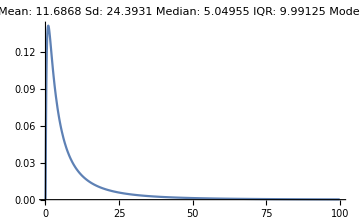
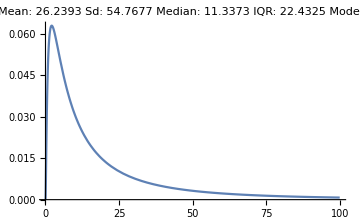

```mathematica
f[#]&/@{LogNormalDistribution[1.6193,1.2955],LogNormalDistribution[1.6193+0.8088,1.2955]}
```

## For co-variables with more than 4 categories

### Sampling

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
LogNormalDistribution[]{Histogram[#],DistributionFitTest[#],Mean[#],MeanCI[#],Quantile[#,{0.025,0.97}]}&/@Transpose[%38]
```

```mathematica
{μ,σ}={1.6193,1.2955};
```

```mathematica
sample=Table[RandomVariate[LogNormalDistribution[μ,σ],10^4],10000];
```

```mathematica
{Mean[#], StandardDeviation[#],Variance[#],Median[#],InterquartileRange[#],Skewness[#]}&/@sample;
```

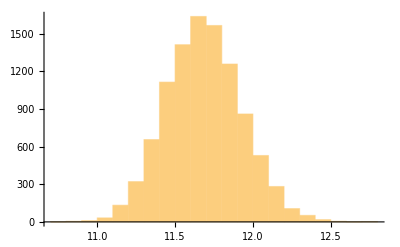
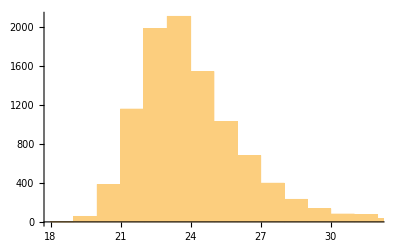
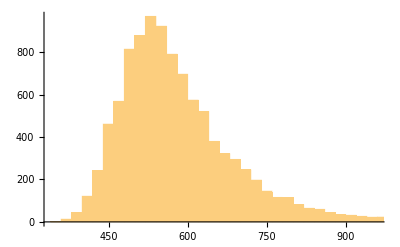
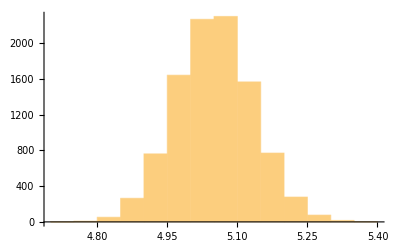
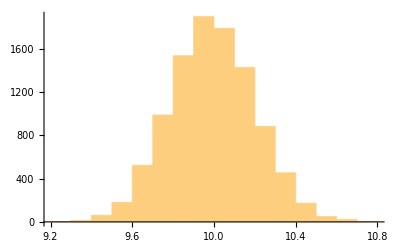
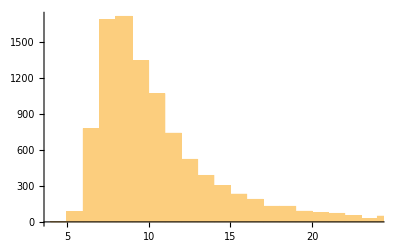
{{-Graphics-,0.0000898081,11.6849,{11.6801,11.6896},{11.2311,12.1498}},{-Graphics-,0,24.1707,{24.1152,24.2262},{20.7177,30.0225}},{-Graphics-,0,592.238,{588.676,595.8},{429.225,901.353}},{-Graphics-,0.107537,5.05074,{5.04911,5.05236},{4.88976,5.20882}},{-Graphics-,0.0763776,9.99235,{9.9883,9.9964},{9.59618,10.3834}},{-Graphics-,0,11.288,{11.1672,11.4088},{6.39727,26.4555}}}

```mathematica
{Histogram[#],DistributionFitTest[#],Mean[#],MeanCI[#],Quantile[#,{0.025,0.97}]}&/@Transpose[%38]
```

```mathematica
Show[Histogram[sample,Automatic,"PDF"],Plot[PDF[LogNormalDistribution[μ,σ],x],{x,0,40},PlotStyle->Thick]]
```

```mathematica
meanSDparaSetsProteinMean
```

```mathematica
disParameters[μ_,σ_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[LogNormalDistribution[μ,σ],samplingSize],samplingN];
{Mean[#],MeanCI[#],Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}](* asi es: 0.05-0.95*)}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
disParameters[2.72116,1.22546,10^4,10^4]
```

```mathematica
{{32.19745192376149,{32.18meanSDparaSetsProteinMean57,32.209192071999105},{31.04399260023794,33.41919406872133},{31.04399260023794,33.07634457581818}},{59.85373506662102,{59.74079599335037,59.96667413989167},{52.25323540036967,73.15467714987471},{52.25323540036967,67.51609891755105}},{3615.66238531063,{3600.0987962003114,3631.225974420948},{2730.400609806446,5351.606788902401},{2730.400609806446,4558.423613044538}},{15.196691552376826,{15.192130785412596,15.201252319341057},{14.745172822152755,15.653927366571335},{14.745172822152755,15.533447267187219}},{28.082252898611873,{28.071557951249208,28.09294784597454},{27.013081070311575,29.153673646203025},{27.013081070311575,28.867296942815166}},{9.824395222308578,{9.72355021782956,9.925240226787595},{5.728897519627604,23.354828255224067},{5.728897519627604,15.930165321572701}}}
```

```mathematica
hRDPeaksValleys1={{2.72116,1.22546},{2.72116+0.10025,1.22546},{2.72116+0.23457,1.22546},{2.72116-0.21456,1.22546},{2.72116-2.39822,1.22546},{2.72116-0.14855,1.22546},{2.72116-0.48414,1.22546},{2.72116-0.36257,1.22546},{2.72116-0.02292,1.22546},{2.72116-0.39599,1.22546},{2.72116-1.17189,1.22546}}(*w1-11*);
```

```mathematica
hICUfPeaksValleys1= {{2.03217,0.96038},{2.03217+0.43093,0.96038},{2.03217+0.01899,0.96038},{2.03217-0.23709,0.96038},{2.03217-0.19294,0.96038},{2.03217-0.20972,0.96038},{2.03217-0.29289,0.96038},{2.03217-0.63277,0.96038},{2.03217-0.62895,0.96038},{2.03217-0.56535,0.96038},{2.03217-0.73223,0.96038}};
```

```mathematica
icufRDPeaksValleys1= {{2.49855,1.13066},{2.49855-0.00948,1.13066},{2.49855-0.06642,1.13066},{2.49855-0.52393,1.13066},{2.49855-0.74051,1.13066},{2.49855-0.03574,1.13066},{2.49855-0.22240,1.13066},{2.49855-0.21912,1.13066},{2.49855-0.1828,1.13066},{2.49855-0.23224,1.13066},{2.49855-0.72220,1.13066}};
```

```mathematica
b3PeaksValleys1= {{3.20873,0.74938},{3.20873+0.20593,0.74938},{3.20873-0.04181,0.74938},{3.20873-0.36312,0.74938},{3.20873-0.46214,0.74938},{3.20873-0.11173,0.74938},{3.20873-0.24296,0.74938},{3.20873-0.37187,0.74938},{3.20873-0.33111,0.74938},{3.20873-0.34937,0.74938},{3.20873-0.81659,0.74938}};
```

```mathematica
icuRDPeaksValleys1={{1.94747,1.19230},{1.94747-0.13429,1.19230},{1.94747+0.30080,1.19230},{1.94747+0.41102,1.19230},{1.94747-1.58377,1.19230},{1.94747+0.44315,1.19230},{1.94747+0.43875,1.19230},{1.94747+0.35617,1.19230},{1.94747+0.49362,1.19230},{1.94747+0.42016,1.19230},{1.94747-0.23442,1.19230}};
```

```mathematica
icuHfPeaksValleys1={{2.8993,1.2805},{2.8993-0.0975,1.2805},{2.8993-1.1958,1.2805},{2.8993-0.8599,1.2805},{2.8993-0.8908,1.2805},{2.8993-0.5424,1.2805},{2.8993-0.4423,1.2805},{2.8993-0.5216,1.2805},{2.8993-0.4006,1.2805},{2.8993-0.5104,1.2805},{2.8993-1.0030,1.2805}};
```

```mathematica
hfRDPeaksValleys1={{1.99037,1.30036},{1.99037-0.70559,1.30036},{1.99037+0.54390,1.30036},{1.99037-0.67199,1.30036},{1.99037-0.66712,1.30036},{1.99037+0.00470,1.30036},{1.99037-0.27526,1.30036},{1.99037-0.73596,1.30036},{1.99037-0.92885,1.30036},{1.99037-0.20823,1.30036},{1.99037-1.09446,1.30036}}:
```

```mathematica
bp4PeaksValleys1={{3.5141,0.9615},{3.5141-0.3274,0.9615},{3.5141-0.3066,0.9615},{3.5141-0.9083,0.9615},{3.5141-0.9323,0.9615},{3.5141-0.4179,0.9615},{3.5141-0.4491,0.9615},{3.5141-0.5982,0.9615},{3.5141-0.2254,0.9615},{3.5141-0.2705,0.9615},{3.5141-1.1756,0.9615}};
```

```mathematica
hRDDeparment={{1.555855,1.613640},{1.555855+0.036706,1.613640},{1.555855-0.047319,1.613640},{1.555855+0.361602,1.613640},{1.555855+0.271798,1.613640},{1.555855+0.453010,1.613640},{1.555855+0.517694,1.613640},{1.555855+0.085876,1.613640},{1.555855-0.004816,1.613640},{1.555855+0.358779,1.613640},{1.555855-0.127776,1.613640},{1.555855+0.588434,1.613640},{1.555855+0.312406,1.613640},{1.555855+0.612047,1.613640},{1.555855+0.705407,1.613640},{1.555855+0.367834,1.613640},{1.555855+0.551575,1.613640},{1.555855-0.748105,1.613640},{1.555855+0.477216,1.613640},{1.555855-0.451714,1.613640},{1.555855-0.055780,1.613640},{1.555855+0.598353,1.613640},{1.555855-0.203502,1.613640},{1.555855+0.551172,1.613640},{1.555855+0.210961,1.613640},{1.555855+1.149278,1.613640},{1.555855-0.338393,1.613640},{1.5558550+.042507,1.613640},{1.555855+0.452726,1.613640},{1.555855+0.334803,1.613640},{1.5558550+0.383321,1.613640},{1.555855+0.508053,1.613640},{1.555855+0.261172,1.613640},{1.555855+0.250029,1.613640},{1.555855-0.042506,1.613640},{1.555855+0.160563,1.613640}};
```

```mathematica
icuRDDeparment//Length
```

36

```mathematica
icuRDDeparment={{2.126368,1.390318},{2.126368-0.521379,1.390318},{2.126368-0.800959,1.390318},{2.126368-0.441619,1.390318},{2.126368-0.404505,1.390318},{2.126368+0.115869,1.390318},{2.126368-0.458808,1.390318},{2.126368-0.330332,1.390318},{2.126368-0.464363,1.390318},{2.126368-0.676498,1.390318},{2.126368-0.684106,1.390318},{2.126368-0.313282,1.390318},{2.126368-0.00453,1.390318},{2.126368-0.433572,1.390318},{2.126368-0.034747,1.390318},{2.126368-0.625346,1.390318},{2.126368-0.576928,1.390318},{2.126368-1.341478,1.390318},{2.126368-0.633889,1.390318},{2.126368-1.309755,1.390318},{2.126368-0.500689,1.390318},{2.126368-0.614682,1.390318},{2.126368-1.006438,1.390318},{2.126368-0.235501,1.390318},{2.126368-0.258461,1.390318},{2.1263680+0.059071,1.390318},{2.126368-1.172896,1.390318},{2.126368-0.521892,1.390318},{2.126368-0.595064,1.390318},{2.126368-0.610119,1.390318},{2.126368-0.455846,1.390318},{2.126368-0.868064,1.390318},{2.126368-0.594899,1.390318},{2.126368-0.334328,1.390318},{2.126368-1.331521,1.390318},{2.126368-0.417546,1.390318}};
```

### Clustering

```mathematica
{uno,dos,tres,cuatro,cinco,seis,siete,ocho,nueve,diez}=Table[Import["/home/lina/Documents/UnCover/datos_INS/"<>i<>".csv"]//ToExpression,{i,{"uno","dos","tres","cuatro","cinco","seis","siete","ocho","nueve","diez"}}];
```

```mathematica
estimados={uno,dos,tres,cuatro,cinco,seis,siete,ocho,nueve,diez}[[All,All,All,1]];(*del 1-8 son picos y valles, 9-10 son departamentos H y ICU *)
```

```mathematica
estimados//{Dimensions[#],Length[#],Depth[#]}&
```

{{10},10,4}

```mathematica
(*{mean,sd,varince, median, iqr,skewness}*)
```

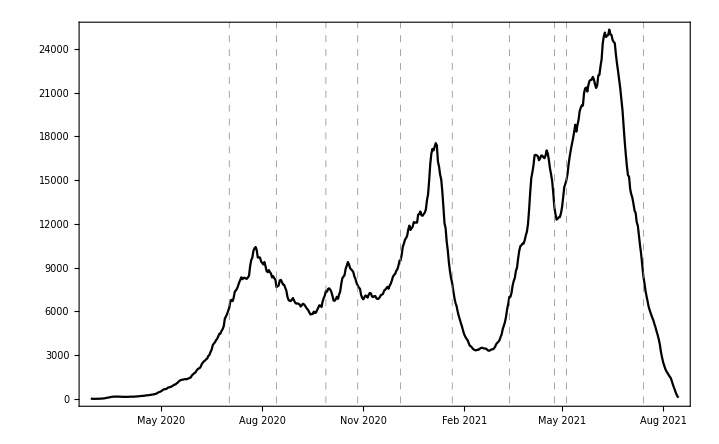

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","ICURD","ICUH-","-HRD","ICUHRD"}->Table[FindClusters[Thread[estimados[[i]]->{"w1","w2","w3","w4","w5","w6","w7","w8","w9","w10","w11"}]],{i,1,8}]]
```

{HRD→{{w1,w2,w4,w6,w8,w9},{w3},{w5},{w7,w10,w11}},HICU-→{{w1,w4,w6},{w2},{w3,w5,w7},{w8},{w9,w10,w11}},-ICURD→{{w1,w3,w6},{w2},{w4},{w5,w11},{w7,w8,w9,w10}},HICURD→{{w1,w3,w4,w5,w6,w7,w8,w9,w10},{w2},{w11}},ICURD→{{w1,w2,w11},{w3,w4,w6,w7,w8,w9,w10},{w5}},ICUH-→{{w1,w2},{w3,w5,w11},{w4},{w6,w7,w8,w9,w10}},-HRD→{{w1,w6,w7,w10},{w2,w4,w5,w8,w9,w11},{w3}},ICUHRD→{{w1},{w2,w3,w9},{w4,w5,w11},{w6,w7,w8,w10}}}

```mathematica
rTimesHw=Thread[{"w1","w2","w3","w4","w5","w6","w7","w8","w9","w10","w11"}->estimados[[1,All,4]]]//Sort(* mediana en H*)
```

{w1→15.1998,w10→10.2295,w11→4.70709,w2→16.8022,w3→19.22,w4→12.2661,w5→1.38125,w6→13.0996,w7→9.36718,w8→10.5806,w9→14.8563}

```mathematica
hGw=FindClusters[Thread[estimados[[1,All,4]]->{"w1","w2","w3","w4","w5","w6","w7","w8","w9","w10","w11"}],2,Method->"KMeans"]
```

{{w1,w2,w3,w4,w6,w9},{w5,w7,w8,w10,w11}}

```mathematica
hGw/.rTimesHw
```

{{15.1998,16.8022,19.22,14.8563},{12.2661,13.0996,9.36718,10.5806,10.2295},{1.38125,4.70709}}

```mathematica
ruleHG=Map[Thread,Thread[Flatten[hG,1]->{"4-5","6-7","7.1-9","2-3","15"}]]//Flatten
```

{AMAZONAS→4-5,ANTIOQUIA→4-5,ARAUCA→4-5,BOYACA→4-5,CALDAS→4-5,CARTAGENA→4-5,HUILA→4-5,META→4-5,RISARALDA→4-5,VAUPES→4-5,ATLANTICO→6-7,BARRANQUILLA→6-7,CAQUETA→6-7,CAUCA→6-7,CORDOBA→6-7,NORTE SANTANDER→6-7,SANTANDER→6-7,STA MARTA→6-7,TOLIMA→6-7,VALLE→6-7,VICHADA→6-7,BOGOTA→7.1-9,BOLIVAR→7.1-9,CASANARE→7.1-9,CESAR→7.1-9,CHOCO→7.1-9,CUNDINAMARCA→7.1-9,GUAJIRA→7.1-9,MAGDALENA→7.1-9,NARIÑO→7.1-9,SAN ANDRES→7.1-9,SUCRE→7.1-9,GUAINIA→2-3,GUAVIARE→2-3,QUINDIO→2-3,PUTUMAYO→15}

```mathematica
(************************************************************************************************************)
```

Clustering departments by median

```mathematica
d={"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"};
```

```mathematica
Thread[{"HRD","ICURD"}->Table[FindClusters[Thread[estimados[[i]]->{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}]],{i,{-2,-1}}]]
```

{HRD→{{AMAZONAS,ANTIOQUIA,ARAUCA,ATLANTICO,BARRANQUILLA,BOGOTA,BOLIVAR,BOYACA,CALDAS,CAQUETA,CARTAGENA,CASANARE,CAUCA,CESAR,CHOCO,CORDOBA,CUNDINAMARCA,GUAINIA,GUAJIRA,GUAVIARE,HUILA,MAGDALENA,META,NARIÑO,NORTE SANTANDER,PUTUMAYO,QUINDIO,RISARALDA,SAN ANDRES,SANTANDER,STA MARTA,SUCRE,TOLIMA,VALLE,VAUPES,VICHADA}},ICURD→{{AMAZONAS,BOGOTA,CAUCA,CHOCO,PUTUMAYO},{ANTIOQUIA,ARAUCA,ATLANTICO,BARRANQUILLA,BOLIVAR,BOYACA,CALDAS,CAQUETA,CARTAGENA,CASANARE,CESAR,CORDOBA,CUNDINAMARCA,GUAJIRA,HUILA,MAGDALENA,NARIÑO,NORTE SANTANDER,RISARALDA,SAN ANDRES,SANTANDER,STA MARTA,SUCRE,TOLIMA,VALLE,VICHADA},{GUAINIA,GUAVIARE,META,QUINDIO,VAUPES}}}

```mathematica
rTimesH=Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->estimados[[-2,All,4]]]//Sort(* mediana en H*)
```

{AMAZONAS→4.74018,ANTIOQUIA→4.91504,ARAUCA→4.52192,ATLANTICO→6.8018,BARRANQUILLA→6.22107,BOGOTA→7.45557,BOLIVAR→7.95623,BOYACA→5.16351,CALDAS→4.71857,CAQUETA→6.78706,CARTAGENA→4.17195,CASANARE→8.53752,CAUCA→6.47663,CESAR→8.7384,CHOCO→9.60169,CORDOBA→6.84828,CUNDINAMARCA→8.23151,GUAINIA→2.24334,GUAJIRA→7.63943,GUAVIARE→3.01586,HUILA→4.48396,MAGDALENA→8.62169,META→3.86701,NARIÑO→8.22295,NORTE SANTANDER→5.85148,PUTUMAYO→14.9611,QUINDIO→3.37934,RISARALDA→4.94624,SAN ANDRES→7.45334,SANTANDER→6.62561,STA MARTA→6.95265,SUCRE→7.8792,TOLIMA→6.15802,VALLE→6.08844,VAUPES→4.5427,VICHADA→5.56433}

```mathematica
hG=Table[FindClusters[Thread[estimados[[i,All,4]]->{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}],5,Method->"KMeans"],{i,{-2}}]
```

{{{AMAZONAS,ANTIOQUIA,ARAUCA,BOYACA,CALDAS,CARTAGENA,HUILA,META,RISARALDA,VAUPES},{ATLANTICO,BARRANQUILLA,CAQUETA,CAUCA,CORDOBA,NORTE SANTANDER,SANTANDER,STA MARTA,TOLIMA,VALLE,VICHADA},{BOGOTA,BOLIVAR,CASANARE,CESAR,CHOCO,CUNDINAMARCA,GUAJIRA,MAGDALENA,NARIÑO,SAN ANDRES,SUCRE},{GUAINIA,GUAVIARE,QUINDIO},{PUTUMAYO}}}

```mathematica
hG/.rTimesH
```

{{{4.74018,4.91504,4.52192,5.16351,4.71857,4.17195,4.48396,3.86701,4.94624,4.5427},{6.8018,6.22107,6.78706,6.47663,6.84828,5.85148,6.62561,6.95265,6.15802,6.08844,5.56433},{7.45557,7.95623,8.53752,8.7384,9.60169,8.23151,7.63943,8.62169,8.22295,7.45334,7.8792},{2.24334,3.01586,3.37934},{14.9611}}}

```mathematica
ruleHG=Map[Thread,Thread[Flatten[hG,1]->{"4-5","6-7","7.1-9","2-3","15"}]]//Flatten
```

{AMAZONAS→4-5,ANTIOQUIA→4-5,ARAUCA→4-5,BOYACA→4-5,CALDAS→4-5,CARTAGENA→4-5,HUILA→4-5,META→4-5,RISARALDA→4-5,VAUPES→4-5,ATLANTICO→6-7,BARRANQUILLA→6-7,CAQUETA→6-7,CAUCA→6-7,CORDOBA→6-7,NORTE SANTANDER→6-7,SANTANDER→6-7,STA MARTA→6-7,TOLIMA→6-7,VALLE→6-7,VICHADA→6-7,BOGOTA→7.1-9,BOLIVAR→7.1-9,CASANARE→7.1-9,CESAR→7.1-9,CHOCO→7.1-9,CUNDINAMARCA→7.1-9,GUAJIRA→7.1-9,MAGDALENA→7.1-9,NARIÑO→7.1-9,SAN ANDRES→7.1-9,SUCRE→7.1-9,GUAINIA→2-3,GUAVIARE→2-3,QUINDIO→2-3,PUTUMAYO→15}

```mathematica
(****************************************************)
```

```mathematica
rTimesUCI=Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->estimados[[-1,All,4]]]//Sort(* mediana en ICU *)
```

{AMAZONAS→8.38514,ANTIOQUIA→4.97836,ARAUCA→3.76486,ATLANTICO→5.392,BARRANQUILLA→5.59599,BOGOTA→9.41789,BOLIVAR→5.30001,BOYACA→6.02576,CALDAS→5.27005,CAQUETA→4.26321,CARTAGENA→4.23152,CASANARE→6.13094,CAUCA→8.3462,CESAR→5.43458,CHOCO→8.09866,CORDOBA→4.48754,CUNDINAMARCA→4.70985,GUAINIA→2.19205,GUAJIRA→4.44914,GUAVIARE→2.26305,HUILA→5.08246,MAGDALENA→4.53624,META→3.06508,NARIÑO→6.62748,NORTE SANTANDER→6.47698,PUTUMAYO→8.89634,QUINDIO→2.59565,RISARALDA→4.97482,SAN ANDRES→4.62416,SANTANDER→4.55547,STA MARTA→5.31703,SUCRE→3.51912,TOLIMA→4.62693,VALLE→6.00358,VAUPES→2.21405,VICHADA→5.52187}

```mathematica
uciG=Table[FindClusters[Thread[estimados[[i,All,4]]->{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}],5,Method->"KMeans"],{i,{-1}}]
```

{{{AMAZONAS,BOGOTA,CAUCA,CHOCO,PUTUMAYO},{ANTIOQUIA,CAQUETA,CARTAGENA,CORDOBA,CUNDINAMARCA,GUAJIRA,HUILA,MAGDALENA,RISARALDA,SAN ANDRES,SANTANDER,TOLIMA},{ARAUCA,META,SUCRE},{ATLANTICO,BARRANQUILLA,BOLIVAR,BOYACA,CALDAS,CASANARE,CESAR,NARIÑO,NORTE SANTANDER,STA MARTA,VALLE,VICHADA},{GUAINIA,GUAVIARE,QUINDIO,VAUPES}}}

```mathematica
uciG/.rTimesUCI
```

{{{8.38514,9.41789,8.3462,8.09866,8.89634},{4.97836,4.26321,4.23152,4.48754,4.70985,4.44914,5.08246,4.53624,4.97482,4.62416,4.55547,4.62693},{3.76486,3.06508,3.51912},{5.392,5.59599,5.30001,6.02576,5.27005,6.13094,5.43458,6.62748,6.47698,5.31703,6.00358,5.52187},{2.19205,2.26305,2.59565,2.21405}}}

```mathematica
ruleUCIG=Map[Thread,Thread[Flatten[uciG,1]->{"8-9","4-5","2-3","5.1-7","2-3"}]]//Flatten
```

{AMAZONAS→8-9,BOGOTA→8-9,CAUCA→8-9,CHOCO→8-9,PUTUMAYO→8-9,ANTIOQUIA→4-5,CAQUETA→4-5,CARTAGENA→4-5,CORDOBA→4-5,CUNDINAMARCA→4-5,GUAJIRA→4-5,HUILA→4-5,MAGDALENA→4-5,RISARALDA→4-5,SAN ANDRES→4-5,SANTANDER→4-5,TOLIMA→4-5,ARAUCA→2-3,META→2-3,SUCRE→2-3,ATLANTICO→5.1-7,BARRANQUILLA→5.1-7,BOLIVAR→5.1-7,BOYACA→5.1-7,CALDAS→5.1-7,CASANARE→5.1-7,CESAR→5.1-7,NARIÑO→5.1-7,NORTE SANTANDER→5.1-7,STA MARTA→5.1-7,VALLE→5.1-7,VICHADA→5.1-7,GUAINIA→2-3,GUAVIARE→2-3,QUINDIO→2-3,VAUPES→2-3}

```mathematica
(*******************************************************************0)
```

```mathematica
code=ToString/@{"05","08",11,13,15,17,18,19,20,23,25,27,41,44,47,50,52,54,63,66,68,70,73,76,81,85,86,88,91,94,95,97,99};
dep={"ANTIOQUIA","ATLANTICO","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CAUCA","CESAR","CORDOBA","CUNDINAMARCA","CHOCO","HUILA","GUAJIRA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","QUINDIO","RISARALDA","SANTANDER","SUCRE","TOLIMA","VALLE","ARAUCA","CASANARE","PUTUMAYO","SAN ANDRES","AMAZONAS","GUAINIA","GUAVIARE","VAUPES","VICHADA"};
```

```mathematica
hGcol=dep/.ruleHG
```

{4-5,6-7,7.1-9,7.1-9,4-5,4-5,6-7,6-7,7.1-9,6-7,7.1-9,7.1-9,4-5,7.1-9,7.1-9,4-5,7.1-9,6-7,2-3,4-5,6-7,7.1-9,6-7,6-7,4-5,7.1-9,15,7.1-9,4-5,2-3,2-3,4-5,6-7}

```mathematica
uciGcol=dep/.ruleUCIG
```

{4-5,5.1-7,8-9,5.1-7,5.1-7,5.1-7,4-5,8-9,5.1-7,4-5,4-5,8-9,4-5,4-5,4-5,2-3,5.1-7,5.1-7,2-3,4-5,4-5,2-3,4-5,5.1-7,2-3,5.1-7,8-9,4-5,8-9,2-3,2-3,2-3,5.1-7}

```mathematica
hTimes=dep/.rTimesH
```

{4.91504,6.8018,7.45557,7.95623,5.16351,4.71857,6.78706,6.47663,8.7384,6.84828,8.23151,9.60169,4.48396,7.63943,8.62169,3.86701,8.22295,5.85148,3.37934,4.94624,6.62561,7.8792,6.15802,6.08844,4.52192,8.53752,14.9611,7.45334,4.74018,2.24334,3.01586,4.5427,5.56433}

```mathematica
uciTimes=dep/.rTimesUCI
```

{4.97836,5.392,9.41789,5.30001,6.02576,5.27005,4.26321,8.3462,5.43458,4.48754,4.70985,8.09866,5.08246,4.44914,4.53624,3.06508,6.62748,6.47698,2.59565,4.97482,4.55547,3.51912,4.62693,6.00358,3.76486,6.13094,8.89634,4.62416,8.38514,2.19205,2.26305,2.21405,5.52187}

```mathematica
data={{"DPTO","Deparment","Hospital LoS DPTO","Hospital LoS DPTO-clusters","ICU LoS DPTO","ICU LoS DPTO-clusters"},Sequence@@Transpose[{code,dep,hTimes,hGcol,uciTimes,uciGcol}]}
```

{{DPTO,Deparment,Hospital LoS DPTO,Hospital LoS DPTO-clusters,ICU LoS DPTO,ICU LoS DPTO-clusters},{05,ANTIOQUIA,4.91504,4-5,4.97836,4-5},{08,ATLANTICO,6.8018,6-7,5.392,5.1-7},{11,BOGOTA,7.45557,7.1-9,9.41789,8-9},{13,BOLIVAR,7.95623,7.1-9,5.30001,5.1-7},{15,BOYACA,5.16351,4-5,6.02576,5.1-7},{17,CALDAS,4.71857,4-5,5.27005,5.1-7},{18,CAQUETA,6.78706,6-7,4.26321,4-5},{19,CAUCA,6.47663,6-7,8.3462,8-9},{20,CESAR,8.7384,7.1-9,5.43458,5.1-7},{23,CORDOBA,6.84828,6-7,4.48754,4-5},{25,CUNDINAMARCA,8.23151,7.1-9,4.70985,4-5},{27,CHOCO,9.60169,7.1-9,8.09866,8-9},{41,HUILA,4.48396,4-5,5.08246,4-5},{44,GUAJIRA,7.63943,7.1-9,4.44914,4-5},{47,MAGDALENA,8.62169,7.1-9,4.53624,4-5},{50,META,3.86701,4-5,3.06508,2-3},{52,NARIÑO,8.22295,7.1-9,6.62748,5.1-7},{54,NORTE SANTANDER,5.85148,6-7,6.47698,5.1-7},{63,QUINDIO,3.37934,2-3,2.59565,2-3},{66,RISARALDA,4.94624,4-5,4.97482,4-5},{68,SANTANDER,6.62561,6-7,4.55547,4-5},{70,SUCRE,7.8792,7.1-9,3.51912,2-3},{73,TOLIMA,6.15802,6-7,4.62693,4-5},{76,VALLE,6.08844,6-7,6.00358,5.1-7},{81,ARAUCA,4.52192,4-5,3.76486,2-3},{85,CASANARE,8.53752,7.1-9,6.13094,5.1-7},{86,PUTUMAYO,14.9611,15,8.89634,8-9},{88,SAN ANDRES,7.45334,7.1-9,4.62416,4-5},{91,AMAZONAS,4.74018,4-5,8.38514,8-9},{94,GUAINIA,2.24334,2-3,2.19205,2-3},{95,GUAVIARE,3.01586,2-3,2.26305,2-3},{97,VAUPES,4.5427,4-5,2.21405,2-3},{99,VICHADA,5.56433,6-7,5.52187,5.1-7}}

```mathematica
Export["/home/lina/Documents/UnCover/uncoverP1LoS/uncoverP1LoS_AFTf/depClusters.csv",data]
```

/home/lina/Documents/UnCover/uncoverP1LoS/uncoverP1LoS_AFTf/depClusters.csv

```mathematica
(*NOTE:
cómo hacer los mapas de calor 
cómo hacer para quitar los missing
cómo ponerle los nombres
cómo ordenar las categoiras-mapa Hospital*)
```

Sera que en vez de agrupar por la mediana agrupo por las similitudes en la curva y esta la caracterizo con los momentos crudos?????

## Sampling tableS2

### Sampling no adjusted

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
timesByBedBP={LogNormalDistribution[1.86949,1.62872],GammaDistribution[1.270,1/0.132],GammaDistribution[1.03102,1/0.05843],LogNormalDistribution[3.02375,0.77873],LogNormalDistribution[1.9121,1.0631],LogNormalDistribution[1.9071,1.2672],LogNormalDistribution[1.7567,1.3689],LogNormalDistribution[3.4189,0.7284],LogNormalDistribution[1.90150,1.42683],LogNormalDistribution[2.3690,1.3125],LogNormalDistribution[1.5933,1.3777],GammaDistribution[1.35165,1/0.03842],LogNormalDistribution[1.8667,1.0800],LogNormalDistribution[0.9847,0.9033],LogNormalDistribution[1.8516,1.2405],LogNormalDistribution[3.0828,0.7255]};
```

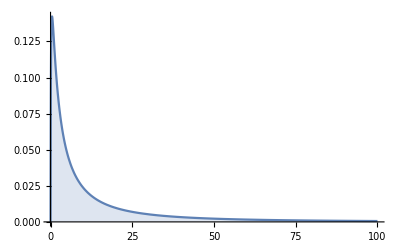
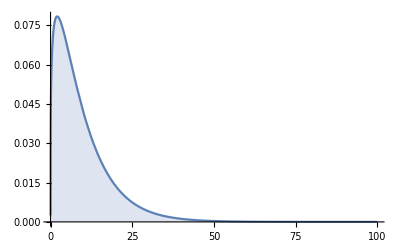
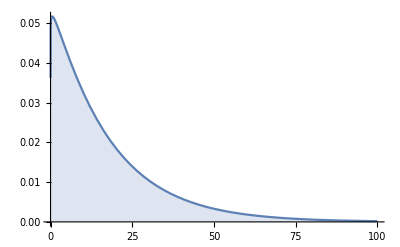
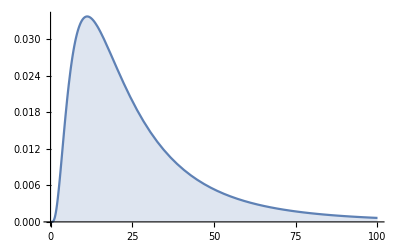
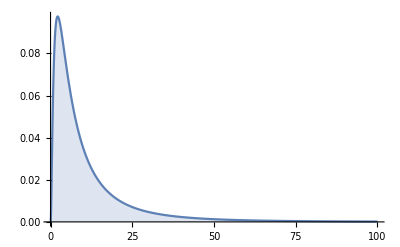
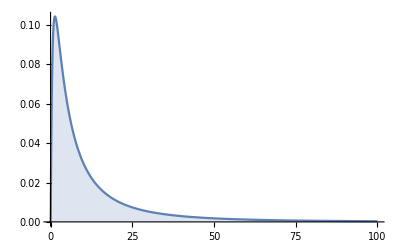
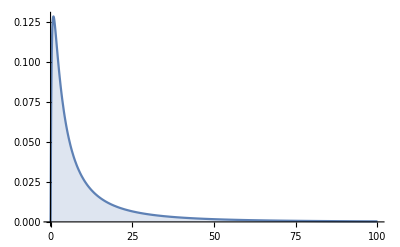
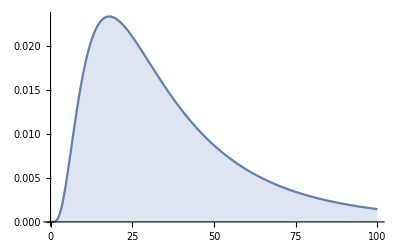

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@timesByBedBP
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
disParameters[GammaDistribution[1.270,1/0.132],10^4,10^4]
```

{{9.6223,{9.62062,9.62398},{9.45367,9.79004},{9.45367,9.74386}},{8.53729,{8.5351,8.53948},{8.32292,8.76298},{8.32292,8.70074}},{72.8978,{72.8604,72.9352},{69.2711,76.7898},{69.2711,75.7029}},{7.24786,{7.24608,7.24963},{7.07062,7.42521},{7.07062,7.37935}},{9.83412,{9.83135,9.83689},{9.56196,10.1075},{9.56196,10.0394}},{1.77215,{1.77074,1.77355},{1.64641,1.92763},{1.64641,1.87821}}}

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,timesByBedBP,Method->"CoarsestGrained"]
```

#### results2

```mathematica
parametrosDis={{{24.425840330835637,{22.838564936597315,26.294150872294896},{22.838564936597315,25.740038220218825}},{85.71131972767083,{63.059799683489494,140.10608145294046},{63.059799683489494,111.3671968590239}},{8027.2234795326385,{3976.5383361218214,19629.714060097987},{3976.5383361218214,12402.652536236583}},{6.487892144538044,{6.23385207480556,6.74754336969161},{6.23385207480556,6.678054236757557}},{2.162101320099746,{2.069331904602092,2.2559432628521567},{2.069331904602092,2.231323634287272}},{19.448247528498772,{18.596521711579094,20.318503226272515},{18.596521711579094,20.079600964718402}},{17.29050954744146,{16.474992999658596,18.12921846262325},{16.474992999658596,17.906676440774035}},{20.717954990740527,{9.640118785887564,56.54671197552292},{9.640118785887564,39.65057685506594}}},{{9.622482523440741,{9.454384068477019,9.790995129357674},{9.454384068477019,9.743739430690875}},{8.539138028933234,{8.325272327166235,8.756278840051548},{8.325272327166235,8.698954734318141}},{72.92914876483009,{69.31015932147992,76.67241912473447},{69.31015932147992,75.671813469716}},{7.247691144014227,{7.073268020622379,7.427638029106452},{7.073268020622379,7.377685755510327}},{3.4366045812725874,{3.325552162610066,3.5491369517669775},{3.325552162610066,3.5196550461568124}},{13.270508499059675,{12.98896718135539,13.56203689945174},{12.98896718135539,13.479732434524973}},{9.834918518855314,{9.565992669896552,10.11220855791451},{9.565992669896552,10.035475127765782}},{1.773869388321192,{1.6435174954378502,1.9258605253685546},{1.6435174954378502,1.88343422652116}}},{{17.646305718559184,{17.298789565194905,17.983977197612727},{17.298789565194905,17.89759394933083}},{17.376874070797772,{16.899210299330317,17.855977627258216},{16.899210299330317,17.728031877146254}},{302.0154737093285,{285.5833087409918,318.83593702514594},{285.5833087409918,314.28311423711375}},{12.379239556360226,{12.033302129616093,12.7237785650555},{12.033302129616093,12.62839018478956}},{5.234404683754916,{5.034731976480368,5.436970473133114},{5.034731976480368,5.382612387823446}},{24.455104673442197,{23.858802008568393,25.04916042382037},{23.858802008568393,24.884543487692536}},{19.22299441807965,{18.667726198449238,19.783338635369756},{18.667726198449238,19.62929621615531}},{1.96760109852811,{1.8207806524334997,2.14603275406602},{1.8207806524334997,2.090604602279393}}},{{27.851121144479567,{27.353350165973218,28.344066188191437},{27.353350165973218,28.211884261306462}},{25.41806641069132,{24.165725060797108,26.86969400037769},{24.165725060797108,26.409224593602616}},{646.5484718251548,{583.9822677140373,721.980455673933},{583.9822677140373,697.4471436353452}},{20.570630456905295,{20.186835245437504,20.968168645538967},{20.186835245437504,20.86219602170558}},{12.165579079469165,{11.914742226063971,12.426918526423979},{11.914742226063971,12.355422714161302}},{34.77372365020708,{34.05314963242902,35.491866969805166},{34.05314963242902,35.31013799032834}},{22.610867842920396,{21.93925071856933,23.310219086075897},{21.93925071856933,23.11280832151069}},{3.4577416140063937,{2.777653067534918,4.914389229163398},{2.777653067534918,4.234903207444404}}},{{11.907627821504335,{11.57708883155251,12.252495096038917},{11.57708883155251,12.159535062215772}},{17.20768794531996,{15.64822528792983,19.60237209689028},{15.64822528792983,18.67088604486888}},{297.1891374063071,{244.8669546618066,384.2529918249426},{244.8669546618066,348.6019857004795}},{6.768201500293022,{6.591605565085172,6.950259200729712},{6.591605565085172,6.903495729951975}},{3.303364726897214,{3.2090235146620913,3.3990821623794285},{3.2090235146620913,3.372396347745046}},{13.861860106673124,{13.47522611358112,14.25421245888052},{13.47522611358112,14.153226223373109}},{10.560221485155498,{10.19157468992946,10.934756851017983},{10.19157468992946,10.834973407653465}},{6.794327196905782,{4.500130828414972,13.913788436882218},{4.500130828414972,9.8701059072214}}},{{15.031783968101204,{14.475531405255158,15.635392138258272},{14.475531405255158,15.460889870688174}},{29.827090979203827,{25.795185403758268,37.31376241646187},{25.795185403758268,33.89309774846481}},{900.2427701505379,{665.3915900142637,1392.3168656721625},{665.3915900142637,1148.7420749869905}},{6.733605016982349,{6.526895255632374,6.942921914412214},{6.526895255632374,6.888625566056673}},{2.864678442033845,{2.7690091256412743,2.9632581437389294},{2.7690091256412743,2.9370322931677615}},{15.824282915498712,{15.302164190135658,16.36365307123273},{15.302164190135658,16.22155268203166}},{12.962157989661785,{12.464571477712937,13.473072684322734},{12.464571477712937,13.343567681364899}},{10.757906243239402,{6.1575525245161735,26.342104870913175},{6.1575525245161735,17.52901435235284}}},{{14.783365393583267,{14.131115932984889,15.499490715204638},{14.131115932984889,15.287602063256251}},{34.359364936319054,{28.619304255348155,46.46168457599537},{28.619304255348155,40.4126812280937}},{1217.781537687903,{819.0645760601891,2158.688133639286},{819.0645760601891,1633.184804043517}},{5.796224012359805,{5.601604180435631,5.997148486445285},{5.601604180435631,5.943994132471432}},{2.3013408376114555,{2.219786163734416,2.3869966626586843},{2.219786163734416,2.3637139872913875}},{14.584437165558576,{14.071618755749915,15.121906013714144},{14.071618755749915,14.973109791514865}},{12.28570238083439,{11.791013867319014,12.798436240944124},{11.791013867319014,12.661855123628944}},{13.202448062717636,{7.014176425672163,35.375674919717845},{7.014176425672163,22.539873561463583}}},{{39.811127607069444,{39.15065691731341,40.46411607789953},{39.15065691731341,40.28694208180361}},{33.30313083785816,{31.857450155865827,35.01136862132952},{31.857450155865827,34.47854288536121}},{1109.7556295692784,{1014.8971304334756,1225.7959327386172},{1014.8971304334756,1188.7699194976922}},{30.53377310700981,{29.980977720673337,31.096576807690397},{29.980977720673337,30.939814732615485}},{18.681760646638118,{18.319379455881432,19.047995427169162},{18.319379455881432,18.94558505846094}},{49.90674739755633,{48.946965713835404,50.89203018746315},{48.946965713835404,50.62733363745466}},{31.22852416315945,{30.32439728784275,32.154690841030515},{30.32439728784275,31.907838861247953}},{3.0798087352815355,{2.521699781687589,4.215503370815439},{2.521699781687589,3.684340038243077}}},{{18.522297099308666,{17.639254586643464,19.4925025107238},{17.639254586643464,19.217120724255178}},{46.98575577760121,{38.17142968184688,65.75149249444657},{38.17142968184688,56.65497980810344}},{2270.0745966745094,{1457.058043956181,4323.258765247263},{1457.058043956181,3209.7867370566087}},{6.695490070691946,{6.4618928911755535,6.931462071142669},{6.4618928911755535,6.869405243702651}},{2.5571159770806573,{2.4588098078408827,2.6563612996594705},{2.4588098078408827,2.628502201079452}},{17.528534569690166,{16.873194027847727,18.215912663099424},{16.873194027847727,18.025445288264237}},{14.974754934097561,{14.34345357346993,15.635442406273933},{14.34345357346993,15.452016808344565}},{14.646952897798684,{7.471832430378684,39.14107165208256},{7.471832430378684,26.40042331250931}}},{{25.29347157454789,{24.276920643014886,26.373147382999015},{24.276920643014886,26.08276584670473}},{53.85551423052894,{45.73639630667152,69.61042342961278},{45.73639630667152,62.207853202815016}},{2952.389521531336,{2091.8179471209164,4845.611050049984},{2091.8179471209164,3869.8170001029825}},{10.69063082575249,{10.34998481667768,11.039251699810993},{10.34998481667768,10.945727835459426}},{4.4092372775792885,{4.252799118890721,4.565229427915542},{4.252799118890721,4.5225488387777855}},{25.8983454510842,{25.015149781458433,26.82548174975487},{25.015149781458433,26.569775004373565}},{21.493633595224704,{20.649653557239134,22.37785226190989},{20.649653557239134,22.136894256249498}},{11.828710614829424,{6.452732264389786,30.493550030828214},{6.452732264389786,19.853134419700936}}},{{12.711075930480348,{12.141835572093587,13.315578242567321},{12.141835572093587,13.14716401832978}},{29.965444694285374,{24.89659272597443,40.41960219450245},{24.89659272597443,35.56590765549214}},{918.3716101470983,{619.8403293630428,1633.7442415618277},{619.8403293630428,1264.9337873589943}},{4.9221262476431935,{4.757544928910847,5.094079300942983},{4.757544928910847,5.046184559693804}},{1.9433188236595924,{1.8721035626044908,2.01696434391202},{1.8721035626044908,1.9971626308824322}},{12.462493731047967,{12.01421899471897,12.92242599958789},{12.01421899471897,12.795636361205451}},{10.521437083845948,{10.096752243443156,10.96295747268761},{10.096752243443156,10.842365053016444}},{13.488369728522922,{7.118040603104666,35.71662887256081},{7.118040603104666,23.706177879150378}}},{{35.18065417446625,{34.57493899244864,35.78066098909837},{34.57493899244864,35.622301538448546}},{30.25777424782309,{29.501066734333886,31.01064073778583},{29.501066734333886,30.815468404054183}},{915.6819050345946,{870.3129384636213,961.6598389680221},{870.3129384636213,949.5930929612616}},{26.98305678064605,{26.347323369790637,27.62150481350793},{26.347323369790637,27.455709672806353}},{13.19076682868611,{12.783418745666593,13.613839119186787},{12.783418745666593,13.499353069479278}},{48.40553911640486,{47.399873252726636,49.42752993280334},{47.399873252726636,49.16177247099183}},{35.21837430833453,{34.25643157490978,36.198543213935466},{34.25643157490978,35.92771226642919}},{1.7178240494107266,{1.5924478583137476,1.8648945637085466},{1.5924478583137476,1.8203238879466062}}},{{11.587592958059844,{11.256737976091896,11.928213502513323},{11.256737976091896,11.836001135106889}},{17.195077111807258,{15.576665266712778,19.758578629995117},{15.576665266712778,18.762643046643287}},{296.8589066548711,{242.63250083121628,390.4014294776997},{242.63250083121628,352.03677409575175}},{6.467447700399551,{6.298047353129455,6.642386406615877},{6.298047353129455,6.594863951752867}},{3.1211269647086985,{3.0343888999669146,3.210255900437107},{3.0343888999669146,3.1866603248511916}},{13.395890911729623,{13.008650352919254,13.785800949557482},{13.008650352919254,13.681178506078199}},{10.276538523903968,{9.907892450087825,10.647654035463853},{9.907892450087825,10.546928814407675}},{7.076167417775557,{4.625023624787388,15.235144597890141},{4.625023624787388,10.43732945003297}}},{{4.025550615091443,{3.9375930575731704,4.1123214590937165},{3.9375930575731704,4.090273067913845}},{4.520116111986328,{4.229949073565658,4.904516730409202},{4.229949073565658,4.767879804967146}},{20.46131321573031,{17.892469164958968,24.054284358863768},{17.892469164958968,22.732677834613547}},{2.677081675847124,{2.6186170577625436,2.7353078555594985},{2.6186170577625436,2.7202738756116442}},{1.4554355574894886,{1.4194622512250077,1.4903331319002298},{1.4194622512250077,1.481442244892993}},{4.922705054483265,{4.8064762589417755,5.042982008678975},{4.8064762589417755,5.010135163221228}},{3.467760710110894,{3.3573754642136584,3.5828172167068644},{3.3573754642136584,3.5510269333021176}},{4.6724252098601795,{3.4785914268579314,7.791062295930576},{3.4785914268579314,6.129195465266315}}},{{13.748577429860246,{13.253908157087162,14.276982954883355},{13.253908157087162,14.1337028631441}},{26.136845995361103,{22.751637635334028,32.17815412635666},{22.751637635334028,29.612845986006494}},{690.0559629235777,{517.6370150895477,1035.4336029795643},{517.6370150895477,876.9206473909409}},{6.369259748440768,{6.178482497964987,6.568766394420479},{6.178482497964987,6.511661228525421}},{2.7595229265217864,{2.668263753801187,2.8505202826750926},{2.668263753801187,2.8272797529903784}},{14.704714075083576,{14.229825258990115,15.193634126802918},{14.229825258990115,15.059409070894043}},{11.947491780562665,{11.497448072339708,12.411384245333839},{11.497448072339708,12.289341051025321}},{10.070673484259533,{5.8583668899226025,24.023882487560194},{5.8583668899226025,16.48769669565442}}},{{28.38878317548241,{27.926566869697343,28.862326885139094},{27.926566869697343,28.729132815708457}},{23.620244561618986,{22.59949618292933,24.785089863480195},{22.59949618292933,24.43543212384314}},{558.2294942775317,{510.73722772223726,614.3006795407888},{510.73722772223726,597.0903430789452}},{21.820278966397435,{21.43905969785643,22.21679368975032},{21.43905969785643,22.103053275146195}},{13.376924118279911,{13.118589523486376,13.636300580583177},{13.118589523486376,13.564091659579038}},{35.58892073431945,{34.90935330753944,36.28088261186716},{34.90935330753944,36.09907173420293}},{22.21453188869448,{21.5747871959744,22.877038370420266},{21.5747871959744,22.695518953173433}},{3.0450127073171536,{2.5124313272237804,4.088410407272592},{2.5124313272237804,3.625162611602643}}}};
```

#### results1

```mathematica
parametrosDis={{{24.426309186331572,{24.409021812083537,24.44359656057963},{22.848737641229462,26.306582914279733},{22.848737641229462,25.731279561884662}},{85.10914677010393,{84.66234563990596,85.5559479003019},{63.30850388837396,138.44407223749695},{63.30850388837396,110.98912191094517}},{7763.0647261714685,{7608.1506140546335,7917.978838288305},{4007.966664584261,19166.761137701276},{4007.966664584261,12318.58518256265}},{6.48582949511106,{6.48323108849427,6.488427901727851},{6.2313335017325375,6.750656016467817},{6.2313335017325375,6.679076159500671}},{17.29003054379169,{17.28182097515543,17.29824011242795},{16.476981475568746,18.11547202906354},{16.476981475568746,17.89670047836581}},{20.437993084971293,{20.20509730149319,20.67088886844939},{9.590082713811777,55.86524690910656},{9.590082713811777,38.51052828110514}}},{{9.62151121240095,{9.61983794123047,9.623184483571423},{9.452706633248441,9.789206273286467},{9.452706633248441,9.743521911024128}},{8.538412727462852,{8.53623850546627,8.540586949459437},{8.320180515263242,8.759450336963495},{8.320180515263242,8.697054659992743}},{72.91679354437474,{72.87965653700313,72.95393055174638},{69.2254038065661,76.72797020572987},{69.2254038065661,75.63875975890149}},{7.245930032695218,{7.2441665939766295,7.2476934714138075},{7.07035756989765,7.427059696461351},{7.07035756989765,7.3757560131483}},{9.834764867888817,{9.832038598931454,9.83749113684619},{9.564033439314073,10.110215424785197},{9.564033439314073,10.034581268127624}},{1.773054351691773,{1.771631821218115,1.77447688216543},{1.643527603548073,1.927677653286896},{1.643527603548073,1.8819528603041293}}},{{17.645941959168862,{17.64257648915651,17.64930742918122},{17.31139283780298,17.984197224115558},{17.31139283780298,17.893746694102568}},{17.37454324517582,{17.36974632755036,17.379340162801263},{16.893256204430045,17.861655390286312},{16.893256204430045,17.728303649254087}},{301.9346326983672,{301.7678792258386,302.10138617089575},{285.38210518851423,319.03873328134404},{285.38210518851423,314.2927502801558}},{12.378259922544574,{12.374837929504071,12.381681915585077},{12.03701031030688,12.722307778107695},{12.03701031030688,12.630857800099491}},{19.221942792277986,{19.21641133345413,19.227474251101835},{18.674597036215417,19.774389934239988},{18.674597036215417,19.62867195259307}},{1.965686336351491,{1.9640602469774828,1.967312425725499},{1.8188161465151569,2.142777707406532},{1.8188161465151569,2.0888879136463427}}},{{27.856147296692967,{27.851101400908203,27.861193192477717},{27.360168445157196,28.367155043941278},{27.360168445157196,28.229088705888717}},{25.43393444415495,{25.42024454388251,25.447624344427403},{24.186387313308447,26.883890472678726},{24.186387313308447,26.44463969543306}},{647.3727247368664,{646.6707375177195,648.074711956014},{584.9813312693678,722.743566946986},{584.9813312693678,699.318968621274}},{20.57057746259135,{20.566605775486167,20.574549149696537},{20.175294156575855,20.968078541693263},{20.175294156575855,20.86198737133457}},{22.615526945438,{22.608655801323795,22.62239808955219},{21.92488269801542,23.309972438476365},{21.92488269801542,23.119289191245244}},{3.469183915431856,{3.4554961234783663,3.482871707385346},{2.7891467780154113,5.016024790923912},{2.7891467780154113,4.239810580921187}}},{{11.908765311832648,{11.905371638062007,11.912158985603291},{11.576670655860207,12.253298730946454},{11.576670655860207,12.16223740291218}},{17.215207588555216,{17.194068591166456,17.236346585943977},{15.677850112365078,19.581457887769485},{15.677850112365078,18.605846290653435}},{297.5262231517517,{296.7336465785653,298.3187997249381},{245.79498414578572,383.4334930104897},{245.79498414578572,346.1775161914222}},{6.767320153665831,{6.765546764262584,6.769093543069083},{6.591657530957523,6.949216185707263},{6.591657530957523,6.896407980030885}},{10.559779877582649,{10.556034857866821,10.563524897298484},{10.19246924276188,10.9446146136956},{10.19246924276188,10.834753433266815}},{6.8160471596107,{6.7555294901132825,6.876564829108121},{4.5251083185736976,13.772347485420426},{4.5251083185736976,9.84428018913729}}},{{15.023009264552767,{15.017093628200517,15.028924900905018},{14.44781413533169,15.630128303252793},{14.44781413533169,15.46039715341407}},{29.715801087597292,{29.65534328973029,29.77625888546431},{25.637215782633433,37.090396408100595},{25.637215782633433,33.96561867463108}},{892.5405724545944,{888.4175495422797,896.6635953669087},{657.2668330853088,1375.6975057100415},{657.2668330853088,1153.6632519504476}},{6.73265528777134,{6.730585351468891,6.73472522407379},{6.529866107750088,6.940915892225499},{6.529866107750088,6.885730722904531}},{12.961260976175604,{12.956177729413923,12.966344222937284},{12.455636152062517,13.474474400459837},{12.455636152062517,13.337545917348287}},{10.597685368092025,{10.488899111936984,10.706471624247058},{6.055723202336238,25.61923299785045},{6.055723202336238,17.674348757538553}}},{{14.78464244927071,{14.777919715429467,14.791365183111948},{14.128942421424057,15.484021561845442},{14.128942421424057,15.285461361950258}},{34.29344207651571,{34.19567832973004,34.391205823301405},{28.578364375334914,45.57854031258353},{28.578364375334914,40.451848413961336}},{1200.9121811796265,{1191.3228455729154,1210.5015167863376},{816.7229103694117,2077.4033370258016},{816.7229103694117,1636.3520401061062}},{5.793841654003714,{5.791892167127013,5.795791140880418},{5.604103388782459,5.9922441304750755},{5.604103388782459,5.937191785184183}},{12.285836126224936,{12.280679558876411,12.290992693573457},{11.776061223556361,12.82004498704675},{11.776061223556361,12.669798285476036}},{13.100746878345138,{12.95438706987074,13.247106686819542},{7.014350726906642,34.564773353636596},{7.014350726906642,22.634510610304297}}},{{39.81500787853367,{39.80848270370973,39.821533053357584},{39.17600154538908,40.49045703150846},{39.17600154538908,40.29786035333502}},{33.29878050608255,{33.28316308779239,33.31439792437271},{31.875235776549687,34.98912398183403},{31.875235776549687,34.4640929106169}},{1109.4434908287408,{1108.3979467305928,1110.4890349268892},{1016.0306558106331,1224.238797016153},{1016.0306558106331,1187.7737001516339}},{30.536317545244767,{30.530897376421972,30.541737714067562},{29.99949332080864,31.08303867397165},{29.99949332080864,30.93919880072857}},{31.225792295654486,{31.21650402057962,31.235080570729338},{30.293559946254383,32.153814026838205},{30.293559946254383,31.907376096639823}},{3.0651690757136865,{3.055749129108782,3.07458902231859},{2.531615151030049,4.174269299385344},{2.531615151030049,3.6367863742324285}}},{{18.53421251971166,{18.524873704046414,18.543551335376904},{17.65474719095229,19.516347584960524},{17.65474719095229,19.23773286329608}},{47.070217934461716,{46.91405815790265,47.226377711020795},{38.39231657268644,65.15170267016268},{38.39231657268644,56.602178722043405}},{2279.0644708196064,{2257.66962683566,2300.459314803551},{1473.969971817374,4244.7443608212825},{1473.969971817374,3203.8066360821435}},{6.69769375658729,{6.695340246744196,6.700047266430386},{6.465496290464127,6.940053356400808},{6.465496290464127,6.868738551438595}},{14.974304829517521,{14.967909208092427,14.980700450942622},{14.345707309294728,15.62496460050572},{14.345707309294728,15.4504629017966}},{14.625012325980014,{14.45794178336871,14.792082868591304},{7.527313503630476,39.17013720734534},{7.527313503630476,25.831876642418553}}},{{25.279722549129918,{25.26909102396314,25.29035407429671},{24.252173895245267,26.378081627207074},{24.252173895245267,26.07183997286617}},{53.705973636383334,{53.56604263997768,53.84590463278896},{45.5883204425039,69.71924256932496},{45.5883204425039,62.18147267939001}},{2935.2861684828886,{2913.3548063610197,2957.2175306047584},{2078.294960768419,4860.772784440374},{2078.294960768419,3866.5355445777263}},{10.684154999932902,{10.680716496820171,10.687593503045644},{10.34360724915312,11.027757169255505},{10.34360724915312,10.940532825079986}},{21.49523913587705,{21.48658976631544,21.503888505438667},{20.63236361191025,22.367411770106457},{20.63236361191025,22.123851419949553}},{11.686535665918944,{11.555830690499802,11.817240641338083},{6.434008197780116,29.676976353741953},{6.434008197780116,19.958730558796105}}},{{12.713205006071572,{12.707211426075387,12.719198586067753},{12.137565959726526,13.340397402074531},{12.137565959726526,13.166977002556948}},{29.9262731125939,{29.84032374812941,30.01222247705839},{24.7678337571225,40.25573636107606},{24.7678337571225,35.6534277972114}},{914.8056816654816,{908.1085005018889,921.5028628290739},{613.4455890204569,1620.5243099724614},{613.4455890204569,1271.1669136909663}},{4.9211186674565255,{4.9194492078617005,4.9227881270513505},{4.756278064056437,5.088619473042618},{4.756278064056437,5.0447447791602835}},{10.5215909820897,{10.51715382223433,10.52602814194507},{10.079755247397117,10.969225292973283},{10.079755247397117,10.851110485478657}},{13.406227741514973,{13.25523668294557,13.55721880008438},{7.040095557081614,34.874663685706146},{7.040095557081614,23.613875807234447}}},{{35.18282720774601,{35.17692275266712,35.18873166282487},{34.59664495380901,35.780107537321534},{34.59664495380901,35.62207971748305}},{30.26199754314539,{30.25443883274645,30.269556253544316},{29.52255265834053,31.015919009906085},{29.52255265834053,30.82216466329129}},{915.9371746505011,{915.4795823659381,916.3947669350641},{871.5811154644896,961.9872320290538},{871.5811154644896,950.0058345310423}},{26.985020239694382,{26.978708898744408,26.991331580644356},{26.357269235279496,27.623662569648943},{26.357269235279496,27.45122010012215}},{35.21216471536234,{35.2026538998798,35.221675530844884},{34.29643066769904,36.17048459968624},{34.29643066769904,35.91669840941519}},{1.7184024084347227,{1.717042589567187,1.7197622273022584},{1.5919210828377655,1.8654747302242551},{1.5919210828377655,1.8201019158746503}}},{{11.587156818875448,{11.583769403218886,11.590544234532016},{11.253354527366952,11.927234392738363},{11.253354527366952,11.83859897504746}},{17.202815915290667,{17.18086573854357,17.224766092037765},{15.58262137470252,19.68543754651585},{15.58262137470252,18.698167067058822}},{297.19068412388623,{296.3669654403878,298.01440280738456},{242.81808890733583,387.516451397776},{242.81808890733583,349.6214516676431}},{6.466838808024509,{6.465135378929356,6.468542237119659},{6.298853186253659,6.639024333039564},{6.298853186253659,6.594819661197699}},{10.27848510932963,{10.274839924357405,10.282130294301858},{9.913409374192106,10.646529706613547},{9.913409374192106,10.54761588691288}},{7.0844323009614865,{7.021235968154937,7.147628633768033},{4.6334976772789,14.799157311838211},{4.6334976772789,10.333173850057046}}},{{4.02533218755068,{4.024443839095925,4.026220536005432},{3.9384293463219633,4.115077998404362},{3.9384293463219633,4.091314170562027}},{4.515961709389041,{4.512648840823159,4.519274577954922},{4.235613377581015,4.894065553909675},{4.235613377581015,4.7591043846547665}},{20.42247051893056,{20.39204821238305,20.452892825478084},{17.94042068434326,23.95187764596521},{17.94042068434326,22.64907454404022}},{2.6774091396337645,{2.6768155979157533,2.6780026813517765},{2.6176772441622194,2.737615766893403},{2.6176772441622194,2.7214983688536494}},{3.4672616607003577,{3.4661337124000786,3.4683896090006368},{3.3557331165175976,3.579020197430474},{3.3557331165175976,3.550285100770375}},{4.647600011509715,{4.6218583337207795,4.6733416892986535},{3.475897193355422,7.743270398410173},{3.475897193355422,6.05715474373845}}},{{13.7501568881065,{13.74494974759392,13.755364028619082},{13.245201299729898,14.280359634040384},{13.245201299729898,14.132604267823877}},{26.183651790183724,{26.122343271239064,26.24496030912837},{22.760028821271618,32.19031452349865},{22.760028821271618,29.59382715404413}},{695.3649280317526,{687.8365751530449,702.8932809104605},{518.0189119451147,1036.2163491217682},{518.0189119451147,875.7946056234398}},{6.370405201753657,{6.368473230553385,6.372337172953926},{6.17674301178411,6.566048243142837},{6.17674301178411,6.512001683351659}},{11.947704322791392,{11.943072227580638,11.95233641800215},{11.490181388380748,12.420968270330885},{11.490181388380748,12.291539812661338}},{10.136084390794615,{10.025877658189692,10.24629112339954},{5.881962049148956,24.55938693371992},{5.881962049148956,16.231801822524524}}},{{28.38953695899336,{28.384916160698605,28.394157757288124},{27.930337691703578,28.851051514648937},{27.930337691703578,28.73210667263764}},{23.620802231574523,{23.60984398204262,23.631760481106426},{22.581140711505444,24.780588237376353},{22.581140711505444,24.447270358897775}},{558.2547891323077,{557.7351890187902,558.7743892458254},{509.90791583280856,614.0775533903953},{509.90791583280856,597.6690280010417}},{21.82358654926726,{21.819692283717885,21.82748081481664},{21.44196871859306,22.208351048914313},{21.44196871859306,22.10920258412579}},{22.21682799445996,{22.210306624148824,22.223349364771085},{21.563950636410212,22.869463775681837},{21.563950636410212,22.697718840645614}},{3.048503880784953,{3.0395030055692724,3.057504756000634},{2.5148089074323234,4.085519642190851},{2.5148089074323234,3.6293429292542165}}}};
```

#### median

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,4,{1,3}]]]
```

{HRD→{6.48583,{6.23133,6.75066}},HICU-→{7.24593,{7.07036,7.42706}},-ICURD→{12.3783,{12.037,12.7223}},HICURD→{20.5706,{20.1753,20.9681}},HICU-→{6.76732,{6.59166,6.94922}},-ICUH-→{6.73266,{6.52987,6.94092}},-HRD→{5.79384,{5.6041,5.99224}},HICUHRD→{30.5363,{29.9995,31.083}},ICURD→{6.69769,{6.4655,6.94005}},ICUH-→{10.6842,{10.3436,11.0278}},-HRD→{4.92112,{4.75628,5.08862}},ICUHRD→{26.985,{26.3573,27.6237}},ICUH-→{6.46684,{6.29885,6.63902}},HICU→{2.67741,{2.61768,2.73762}},ICURD→{6.37041,{6.17674,6.56605}},ICUHICURD→{21.8236,{21.442,22.2084}}}

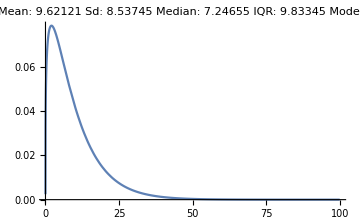

```mathematica
f[GammaDistribution[1.270,1/0.132]]
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### IQR

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,5]]]
```

{HRD→{2.1621,{2.06933,2.25594},{2.06933,2.23132}},HICU-→{3.4366,{3.32555,3.54914},{3.32555,3.51966}},-ICURD→{5.2344,{5.03473,5.43697},{5.03473,5.38261}},HICURD→{12.1656,{11.9147,12.4269},{11.9147,12.3554}},HICU-→{3.30336,{3.20902,3.39908},{3.20902,3.3724}},-ICUH-→{2.86468,{2.76901,2.96326},{2.76901,2.93703}},-HRD→{2.30134,{2.21979,2.387},{2.21979,2.36371}},HICUHRD→{18.6818,{18.3194,19.048},{18.3194,18.9456}},ICURD→{2.55712,{2.45881,2.65636},{2.45881,2.6285}},ICUH-→{4.40924,{4.2528,4.56523},{4.2528,4.52255}},-HRD→{1.94332,{1.8721,2.01696},{1.8721,1.99716}},ICUHRD→{13.1908,{12.7834,13.6138},{12.7834,13.4994}},ICUH-→{3.12113,{3.03439,3.21026},{3.03439,3.18666}},HICU→{1.45544,{1.41946,1.49033},{1.41946,1.48144}},ICURD→{2.75952,{2.66826,2.85052},{2.66826,2.82728}},ICUHICURD→{13.3769,{13.1186,13.6363},{13.1186,13.5641}}}

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,6]]]
```

{HRD→{19.4482,{18.5965,20.3185},{18.5965,20.0796}},HICU-→{13.2705,{12.989,13.562},{12.989,13.4797}},-ICURD→{24.4551,{23.8588,25.0492},{23.8588,24.8845}},HICURD→{34.7737,{34.0531,35.4919},{34.0531,35.3101}},HICU-→{13.8619,{13.4752,14.2542},{13.4752,14.1532}},-ICUH-→{15.8243,{15.3022,16.3637},{15.3022,16.2216}},-HRD→{14.5844,{14.0716,15.1219},{14.0716,14.9731}},HICUHRD→{49.9067,{48.947,50.892},{48.947,50.6273}},ICURD→{17.5285,{16.8732,18.2159},{16.8732,18.0254}},ICUH-→{25.8983,{25.0151,26.8255},{25.0151,26.5698}},-HRD→{12.4625,{12.0142,12.9224},{12.0142,12.7956}},ICUHRD→{48.4055,{47.3999,49.4275},{47.3999,49.1618}},ICUH-→{13.3959,{13.0087,13.7858},{13.0087,13.6812}},HICU→{4.92271,{4.80648,5.04298},{4.80648,5.01014}},ICURD→{14.7047,{14.2298,15.1936},{14.2298,15.0594}},ICUHICURD→{35.5889,{34.9094,36.2809},{34.9094,36.0991}}}

### Sampling adjusted by age

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[1.27392,1.59883],
LogNormalDistribution[1.27392+0.36661,1.59883],
LogNormalDistribution[1.27392+0.88679,1.59883],LogNormalDistribution[1.27392+0.61797,1.59883],LogNormalDistribution[0.91454,1.39385],
LogNormalDistribution[0.91454+0.82730,1.39385],
LogNormalDistribution[0.91454+1.20481,1.39385],LogNormalDistribution[0.91454+0.80441,1.39385]};
```

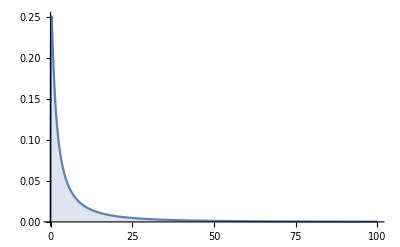
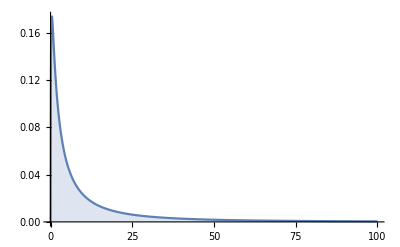
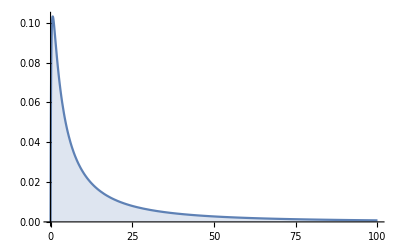
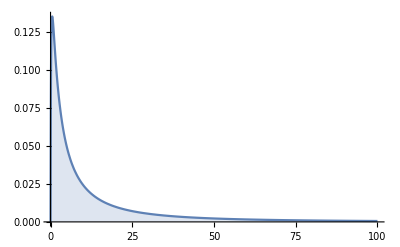
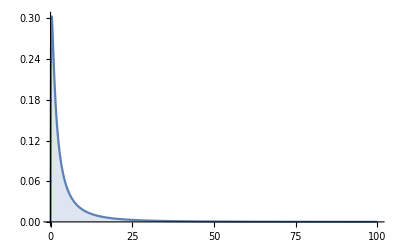
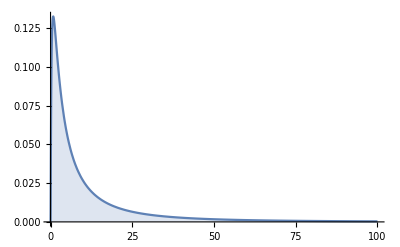
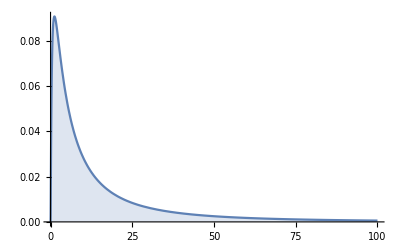
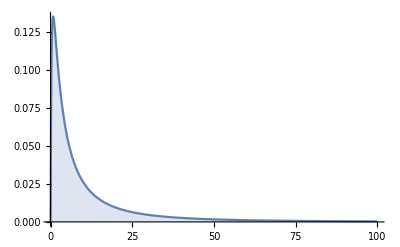

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

#### results1

```mathematica
parametrosDis={{{12.832938299088672,{12.035318873877229,13.78652538789736},{12.035318873877229,13.47766979608534}},{42.814382948195224,{32.26231397809515,68.49761693711157},{32.26231397809515,55.32081535865783}},{1974.0379413158764,{1040.8569032211938,4691.923526063275},{1040.8569032211938,3060.3926119467123}},{3.574292456610502,{3.439089491741692,3.716292869344022},{3.439089491741692,3.6790781216530677}},{1.2159375445084462,{1.1654742756698337,1.2679173000845148},{1.1654742756698337,1.2535194081803525}},{10.502980936012738,{10.071531104130528,10.940000437584716},{10.071531104130528,10.8282556770827}},{9.289408897656834,{8.873441027941912,9.712211102181953},{8.873441027941912,9.60592474613887}},{19.623145339857473,{9.213877880988369,54.674907112377234},{9.213877880988369,36.39064463395044}}},{{18.53229146553374,{17.37730999726347,19.88199128090594},{17.37730999726347,19.468683218144125}},{62.07220484116876,{46.53280726755465,99.75476243131257},{46.53280726755465,79.93686149794586}},{4138.754690911903,{2165.302152199387,9951.01262772761},{2165.302152199387,6389.90182614178}},{5.157654521426901,{4.959935179724798,5.361237009326153},{4.959935179724798,5.305120586573509}},{1.7541332663206246,{1.6796337058480724,1.8307239172706666},{1.6796337058480724,1.8099882958256046}},{15.16523433249708,{14.537923748640338,15.819581117519663},{14.537923748640338,15.639008777426225}},{13.414457653339865,{12.80323544168768,14.048578847707237},{12.80323544168768,13.871643597729012}},{19.814938059166717,{9.373629564005263,54.671514676607764},{9.373629564005263,37.32149935519072}}},{{31.155743952600485,{29.18803917793137,33.385224786102},{29.18803917793137,32.74239242330112}},{104.38148613943666,{78.11182652992707,167.8337290966354},{78.11182652992707,135.26215744060556}},{11753.57344582868,{6101.457443841418,28168.160622482807},{6101.457443841418,18295.851235487167}},{8.675875920708794,{8.334394958077914,9.016204124909265},{8.334394958077914,8.93075433261455}},{2.94992823400033,{2.8249818228159786,3.0794673183727723},{2.8249818228159786,3.0433791202257563}},{25.504224396429326,{24.417865355117808,26.598143419533212},{24.417865355117808,26.308274736449107}},{22.559956545433728,{21.515345318193937,23.62864431198871},{21.515345318193937,23.343843009026582}},{19.87928146186507,{9.349592155887708,55.02822147753518},{9.349592155887708,37.923391772528696}}},{{23.80604766601957,{22.3644136684325,25.564517690672105},{22.3644136684325,25.0060046484195}},{79.49773450450758,{59.755502231487014,126.81711560893156},{59.755502231487014,102.15436710980909}},{6888.471583288989,{3570.7200469372497,16082.580811369111},{3570.7200469372497,10435.514719605644}},{6.6324277022576865,{6.3735222790363775,6.894768475380182},{6.3735222790363775,6.824845753453463}},{2.2561888292527694,{2.1625179145873132,2.353776611949677},{2.1625179145873132,2.3272950510857857}},{19.492235600997248,{18.687533753283624,20.324586325781585},{18.687533753283624,20.10272523153836}},{17.240459256621303,{16.464534998764105,18.036896285085117},{16.464534998764105,17.832066472016418}},{19.643812554919045,{9.283805905900003,55.146641511485406},{9.283805905900003,36.86831763884439}}},{{6.591442252994928,{6.288325405758763,6.919182202638113},{6.288325405758763,6.82805970281091}},{15.885924048914111,{13.113669079242019,21.518800554773577},{13.113669079242019,18.901290596533173}},{258.4923538375736,{171.9683167198682,463.0587773161236},{171.9683167198682,357.25878621459333}},{2.496262651015134,{2.4112668294403132,2.5823228489317174},{2.4112668294403132,2.5593007484177503}},{0.9746269796302309,{0.9388082157652723,1.0117960311275815},{0.9388082157652723,1.0017713179391465}},{6.389440847006726,{6.154169005879072,6.631801940048401},{6.154169005879072,6.564299026385711}},{5.41600606494986,{5.189704864352474,5.650482237920779},{5.189704864352474,5.584755434496966}},{13.769242984195577,{7.2304794829712025,36.95152895877886},{7.2304794829712025,24.222055798227824}}},{{15.077636836581764,{14.384634807790269,15.836280558734584},{14.384634807790269,15.62166793893933}},{36.43737340312309,{30.012083578999732,49.81439675380806},{30.012083578999732,43.16350873365408}},{1367.9487954967267,{900.7251607528655,2481.474123945803},{900.7251607528655,1863.0884862002322}},{5.709108085633917,{5.513317640912642,5.905378391298289},{5.513317640912642,5.854803715035411}},{2.2287057716503567,{2.1461608891561217,2.3154430150167578},{2.1461608891561217,2.2908518399861384}},{14.611529399108656,{14.08340812408363,15.157855184267136},{14.08340812408363,15.006520681199941}},{12.385601123254535,{11.878440266949541,12.903329577822698},{11.878440266949541,12.7679340689401}},{13.832761819376145,{7.204106584045677,37.19963640650778},{7.204106584045677,24.234508874879282}}},{{21.991351732440588,{20.985236786922307,23.112509085930657},{20.985236786922307,22.78550277594575}},{53.175755647698416,{43.7943006456536,72.71182246824432},{43.7943006456536,63.63926248213886}},{2903.3917449177193,{1917.9407690418955,5287.00912665348},{1917.9407690418955,4049.955729270567}},{8.327583771132945,{8.049191381966573,8.617341366605379},{8.049191381966573,8.537875209846478}},{3.2522292862875735,{3.13523556292008,3.3718746005740665},{3.13523556292008,3.3415147277481885}},{21.315660475257715,{20.546077319929726,22.112481785621878},{20.546077319929726,21.89213634557405}},{18.067312214338827,{17.326126701151868,18.83471890232599},{17.326126701151868,18.62281584848528}},{13.924438178852192,{7.2315644876630865,38.30063623690144},{7.2315644876630865,24.590496721913976}}},{{14.737084010672474,{14.063032028733625,15.456359891648805},{14.063032028733625,15.267516814648}},{35.559787712895115,{29.310100561221873,48.51303474212967},{29.310100561221873,42.32983399137745}},{1295.7432299085829,{859.0819949089387,2353.5145398910804},{859.0819949089387,1791.814845737574}},{5.579889806837863,{5.392692674902731,5.77582721832561},{5.392692674902731,5.721325879507818}},{2.179126880330512,{2.0994229321306124,2.2608587530734456},{2.0994229321306124,2.2396226104438677}},{14.28322367689141,{13.762150828091677,14.820397268163724},{13.762150828091677,14.678359045781821}},{12.106761999907159,{11.604782298439696,12.62246635101806},{11.604782298439696,12.484964032294316}},{13.78727739409759,{7.253957373995186,36.92425916686482},{7.253957373995186,24.015618166362046}}}};
```

#### median

```mathematica
Thread[{"HRDG1","HRDG2","HRDG3","HRDG4","ICURDG1","ICURDG2","ICURDG3","ICURDG4"}->parametrosDis[[All,4,{1,3}]]]
```

{HRDG1→{3.57429,{3.43909,3.67908}},HRDG2→{5.15765,{4.95994,5.30512}},HRDG3→{8.67588,{8.33439,8.93075}},HRDG4→{6.63243,{6.37352,6.82485}},ICURDG1→{2.49626,{2.41127,2.5593}},ICURDG2→{5.70911,{5.51332,5.8548}},ICURDG3→{8.32758,{8.04919,8.53788}},ICURDG4→{5.57989,{5.39269,5.72133}}}

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### IQR

```mathematica
Thread[{"HRDG1","HRDG2","HRDG3","HRDG4","ICURDG1","ICURDG2","ICURDG3","ICURDG4"}->parametrosDis[[All,5]]]
```

{HRDG1→{1.21594,{1.16547,1.26792},{1.16547,1.25352}},HRDG2→{1.75413,{1.67963,1.83072},{1.67963,1.80999}},HRDG3→{2.94993,{2.82498,3.07947},{2.82498,3.04338}},HRDG4→{2.25619,{2.16252,2.35378},{2.16252,2.3273}},ICURDG1→{0.974627,{0.938808,1.0118},{0.938808,1.00177}},ICURDG2→{2.22871,{2.14616,2.31544},{2.14616,2.29085}},ICURDG3→{3.25223,{3.13524,3.37187},{3.13524,3.34151}},ICURDG4→{2.17913,{2.09942,2.26086},{2.09942,2.23962}}}

```mathematica
Thread[{"HRDG1","HRDG2","HRDG3","HRDG4","ICURDG1","ICURDG2","ICURDG3","ICURDG4"}->parametrosDis[[All,6]]]
```

{HRDG1→{10.503,{10.0715,10.94},{10.0715,10.8283}},HRDG2→{15.1652,{14.5379,15.8196},{14.5379,15.639}},HRDG3→{25.5042,{24.4179,26.5981},{24.4179,26.3083}},HRDG4→{19.4922,{18.6875,20.3246},{18.6875,20.1027}},ICURDG1→{6.38944,{6.15417,6.6318},{6.15417,6.5643}},ICURDG2→{14.6115,{14.0834,15.1579},{14.0834,15.0065}},ICURDG3→{21.3157,{20.5461,22.1125},{20.5461,21.8921}},ICURDG4→{14.2832,{13.7622,14.8204},{13.7622,14.6784}}}

### Sampling adjusted by BP

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[1.86949,1.60508],
LogNormalDistribution[1.86949-0.05217,1.60508],
LogNormalDistribution[1.86949-0.27617,1.60508],
LogNormalDistribution[1.90150,1.37159],
LogNormalDistribution[1.90150+0.41109,1.37159],
LogNormalDistribution[1.90150+0.46753,1.37159]};
```

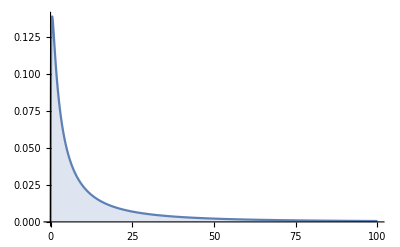
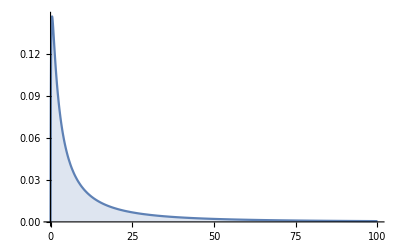
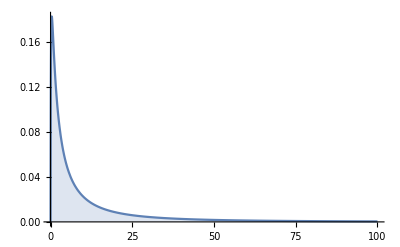
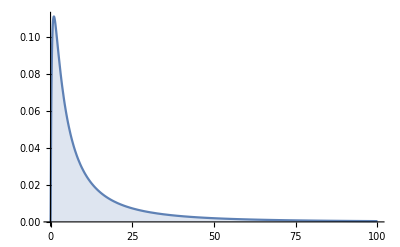
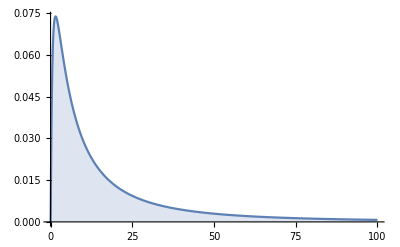
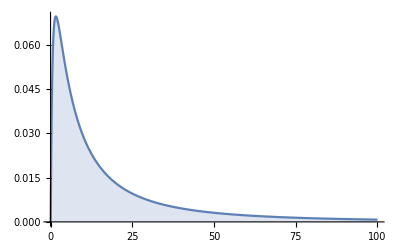

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

```mathematica
Length[parametrosDis]
```

6

#### results1

```mathematica
parametrosDis={{{23.531429653000313,{22.056795133859506,25.272498781993082},{22.056795133859506,24.739094270675253}},{79.44141075170577,{59.42769897493198,128.74613418925532},{59.42769897493198,103.72351201142166}},{6772.944376481785,{3531.651405455131,16575.567068677738},{3531.651405455131,10758.566943983533}},{6.487006335808145,{6.232940003699856,6.744991312370297},{6.232940003699856,6.676664852050845}},{2.1969583006915934,{2.1059984756508303,2.294763130433727},{2.1059984756508303,2.2669048644253182}},{19.146743488746342,{18.332152106375073,19.996185868204417},{18.332152106375073,19.757159990462075}},{16.95413490430748,{16.164973235555646,17.780930958864815},{16.164973235555646,17.544164446489255}},{19.942239364515913,{9.268707825370651,55.54670422310464},{9.268707825370651,37.85159589693093}}},{{22.319166700342286,{20.91032905746352,23.980038381495252},{20.91032905746352,23.460618947595155}},{75.02065096637516,{56.138689612370555,120.83974521965102},{56.138689612370555,97.61628398062736}},{6044.886792292798,{3151.5524713940817,14602.244024750173},{3151.5524713940817,9528.938898186485}},{6.158142866742239,{5.920011122390541,6.407388205753251},{5.920011122390541,6.338925791024881}},{2.085068050247712,{1.9966900438609652,2.176075053229822},{1.9966900438609652,2.1519436792407234}},{18.17654590855156,{17.406662930852168,18.978609635858785},{17.406662930852168,18.76368044130547}},{16.095574196722726,{15.35068440774966,16.87526975425428},{15.35068440774966,16.663374252890502}},{19.78652138472856,{9.283048485494636,54.453085564629255},{9.283048485494636,37.7053377210844}}},{{17.83595180849955,{16.720566834840884,19.1449281240504},{16.720566834840884,18.73210223928502}},{59.84737306827868,{45.14253013840942,94.68054190164975},{45.14253013840942,76.96203337131766}},{3797.129929977244,{2037.8480272972029,8964.405014790053},{2037.8480272972029,5923.1545806478125}},{4.9203789301519665,{4.731563503950801,5.116969326690098},{4.731563503950801,5.064493394724476}},{1.6661610506529967,{1.595141650186501,1.7384405323481236},{1.595141650186501,1.7186503781848488}},{14.524996862044057,{13.91447671590748,15.149140663808717},{13.91447671590748,14.98339602487914}},{12.862038011310036,{12.275786130491845,13.465163699677808},{12.275786130491845,13.307774654356988}},{19.75995754721978,{9.343914198979695,53.378982242453546},{9.343914198979695,37.626457088028076}}},{{17.148439857660346,{16.39028324707885,17.958783326263948},{16.39028324707885,17.731974589259107}},{39.97938279256406,{33.18186962827052,53.74579022551213},{33.18186962827052,47.254955246082076}},{1634.829696505631,{1101.0364720275415,2888.609966964755},{1101.0364720275415,2233.03079530922}},{6.698577785964209,{6.476866178222137,6.927697638790623},{6.476866178222137,6.866392166682196}},{2.6551609947986208,{2.5580560357394644,2.7535895621824946},{2.5580560357394644,2.728395745995142}},{16.888491222737294,{16.273525486783367,17.52084100631901},{16.273525486783367,17.349026239711673}},{14.236406887644913,{13.656128919209888,14.842933964334758},{13.656128919209888,14.679273386142842}},{13.258557561518845,{6.957537417518883,34.48933674245419},{6.957537417518883,23.30963942550098}}},{{25.87043469922903,{24.756762147644245,27.105957529576333},{24.756762147644245,26.76502221696056}},{60.32469765421492,{50.10756274518244,80.86444067121239},{50.10756274518244,71.2479944990106}},{3717.1605584358126,{2510.767844262395,6539.057765068028},{2510.767844262395,5076.276720131045}},{10.102254005382699,{9.779014601459792,10.442940448736358},{9.779014601459792,10.347484013040365}},{4.005492434203008,{3.8601794503451154,4.152343652056918},{3.8601794503451154,4.113394246682495}},{25.473667508445715,{24.557868571708386,26.4141671344227},{24.557868571708386,26.16788608917588}},{21.472768573726448,{20.59253167998841,22.375874765772252},{20.59253167998841,22.136086681780718}},{13.269573462825736,{7.019197898980622,34.625312494190425},{7.019197898980622,23.401444619593978}}},{{27.384990361505672,{26.15601848464583,28.697608699285645},{26.15601848464583,28.328333080656886}},{63.999682951665925,{53.07809327715747,85.97462568197967},{53.07809327715747,75.38589008915443}},{4194.49467809834,{2817.283985938629,7391.636261156519},{2817.283985938629,5683.032424534073}},{10.689574823675233,{10.32597945636881,11.05150078400458},{10.32597945636881,10.955602892506183}},{4.237671118373861,{4.082755187494127,4.39713592651072},{4.082755187494127,4.354361091283745}},{26.950449942006536,{25.962853672450578,27.94701477759957},{25.962853672450578,27.68881854463451}},{22.71755754795121,{21.773671764706492,23.66820696023126},{21.773671764706492,23.415417675799684}},{13.340328434786882,{7.0358687562832065,35.336870051905876},{7.0358687562832065,23.337192839021043}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"HRD1","HRD2","HRD3","ICURD1","ICURD2","ICURD3"}->parametrosDis[[All,4,{1,2}]]]
```

{HRD1→{6.48701,{6.23294,6.74499}},HRD2→{6.15814,{5.92001,6.40739}},HRD3→{4.92038,{4.73156,5.11697}},ICURD1→{6.69858,{6.47687,6.9277}},ICURD2→{10.1023,{9.77901,10.4429}},ICURD3→{10.6896,{10.326,11.0515}}}

#### IQR

```mathematica
Thread[{"HRD1","HRD2","HRD3","ICURD1","ICURD2","ICURD3"}->parametrosDis[[All,5,{1,2}]]]
```

{HRD1→{2.19696,{2.106,2.29476}},HRD2→{2.08507,{1.99669,2.17608}},HRD3→{1.66616,{1.59514,1.73844}},ICURD1→{2.65516,{2.55806,2.75359}},ICURD2→{4.00549,{3.86018,4.15234}},ICURD3→{4.23767,{4.08276,4.39714}}}

```mathematica
Thread[{"HRD1","HRD2","HRD3","ICURD1","ICURD2","ICURD3"}->parametrosDis[[All,6,{1,2}]]]
```

{HRD1→{19.1467,{18.3322,19.9962}},HRD2→{18.1765,{17.4067,18.9786}},HRD3→{14.525,{13.9145,15.1491}},ICURD1→{16.8885,{16.2735,17.5208}},ICURD2→{25.4737,{24.5579,26.4142}},ICURD3→{26.9504,{25.9629,27.947}}}

### Sampling adjusted by Gender

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[1.81207,1.62787],
LogNormalDistribution[1.81207+0.10568,1.62787],
LogNormalDistribution[1.78364,1.42357],
LogNormalDistribution[1.78364+0.19668,1.42357]};
```

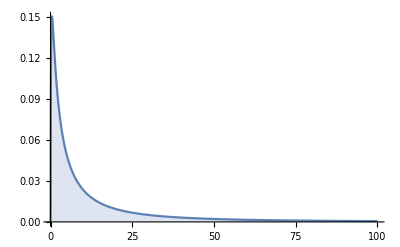
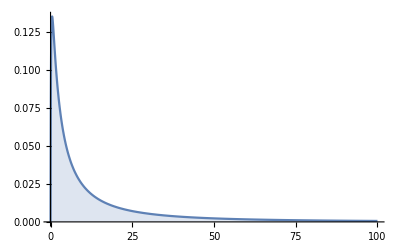
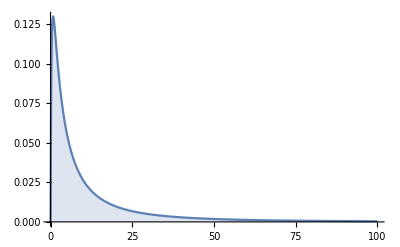
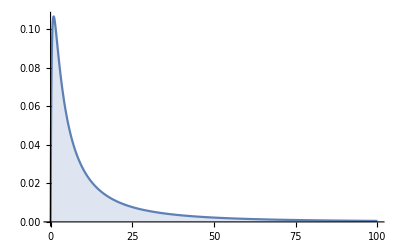

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

```mathematica
Length[parametrosDis]
```

6

#### results1

```mathematica
parametrosDis={{{23.056127727202185,{21.56847942129442,24.81005111551457},{21.56847942129442,24.262605756354095}},{80.71775112885786,{59.75497582690618,131.25957152209813},{59.75497582690618,105.3559792136569}},{7187.5472324267075,{3570.6571360741423,17229.075116164793},{3570.6571360741423,11099.882356068503}},{6.124609026413998,{5.88574495975014,6.3722098619192185},{5.88574495975014,6.30567797242046}},{2.043212437102323,{1.95656259691298,2.1328789080434225},{1.95656259691298,2.1081785855959856}},{18.357626797006564,{17.574527047890744,19.18585859200468},{17.574527047890744,18.94459394742799}},{16.31864421746102,{15.555016612928878,17.118960623276344},{15.555016612928878,16.891450212356663}},{20.545871065772307,{9.58318249384221,55.55390750335967},{9.58318249384221,38.573044072024615}}},{{25.60904247232641,{23.962066893739312,27.587654896026482},{23.962066893739312,26.9686597370487}},{89.48631495788634,{66.46838726146198,147.61898274590177},{66.46838726146198,117.54871242025392}},{8600.566366934556,{4418.046505139682,21791.36406693485},{4418.046505139682,13817.699791659557}},{6.807455644187602,{6.538690729587363,7.090072485290619},{6.538690729587363,7.009534117016532}},{2.269717463053827,{2.1737607636036684,2.370991498443383},{2.1737607636036684,2.342420674957427}},{20.411259930104034,{19.53866871158166,21.298730581015235},{19.53866871158166,21.061993746920717}},{18.146147394443584,{17.30773280814846,19.00722131319422},{17.30773280814846,18.775667135537873}},{20.672663237134874,{9.599294511562904,56.377238335336614},{9.599294511562904,40.01740011627376}}},{{16.388325146854083,{15.599704686159928,17.24549931400914},{15.599704686159928,17.007742560685287}},{41.43201713660074,{33.732418698972054,57.36096199440216},{33.732418698972054,49.8447315053184}},{1765.0045079982083,{1137.8760712827593,3290.279960923249},{1137.8760712827593,2484.4972588372807}},{5.950892808339179,{5.744539087937121,6.1597260961222915},{5.744539087937121,6.100551886499333}},{2.2776545358055205,{2.1932037799790964,2.3657957076151845},{2.1932037799790964,2.3413820842977526}},{15.543249495686975,{14.945694390470381,16.15305533393211},{14.945694390470381,15.981192279482178}},{13.268627597993769,{12.690813258849355,13.854087913826104},{12.690813258849355,13.691095295659093}},{14.617128309653438,{7.500137064781938,39.15982936550728},{7.500137064781938,25.950438627045713}}},{{19.964937038505425,{19.00488379740676,21.024500412648926},{19.00488379740676,20.716145331015714}},{50.65658505853491,{41.14723778727104,71.01316118490685},{41.14723778727104,61.23582595354}},{2655.864516082237,{1693.0951775222259,5042.869061473561},{1693.0951775222259,3749.8263802122433}},{7.2453517445601365,{6.993619543649487,7.503978923536759},{6.993619543649487,7.431432262975722}},{2.774056489693343,{2.668705132783485,2.8817988410414372},{2.668705132783485,2.8515321092986454}},{18.924357759409467,{18.224565937605657,19.667580134963163},{18.224565937605657,19.461957390165878}},{16.153933239258528,{15.478436110184942,16.86304246821964},{15.478436110184942,16.675309100025885}},{14.7640039794348,{7.509355376693853,40.479643657563535},{7.509355376693853,26.408906877460495}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"HRDF","HRDM","ICURDF","ICURDM"}->parametrosDis[[All,4,{1,2}]]]
```

{HRDF→{6.12461,{5.88574,6.37221}},HRDM→{6.80746,{6.53869,7.09007}},ICURDF→{5.95089,{5.74454,6.15973}},ICURDM→{7.24535,{6.99362,7.50398}}}

#### IQR

```mathematica
Thread[{"HRDF","HRDM","ICURDF","ICURDM"}->parametrosDis[[All,5,{1,2}]]]
```

{HRDF→{2.04321,{1.95656,2.13288}},HRDM→{2.26972,{2.17376,2.37099}},ICURDF→{2.27765,{2.1932,2.3658}},ICURDM→{2.77406,{2.66871,2.8818}}}

```mathematica
Thread[{"HRDF","HRDM","ICURDF","ICURDM"}->parametrosDis[[All,6,{1,2}]]]
```

{HRDF→{18.3576,{17.5745,19.1859}},HRDM→{20.4113,{19.5387,21.2987}},ICURDF→{15.5432,{14.9457,16.1531}},ICURDM→{18.9244,{18.2246,19.6676}}}

### Sampling adjusted by Waves

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[2.49148,1.31086],
LogNormalDistribution[2.49148-1.73053,1.31086],
LogNormalDistribution[2.49148-0.48366,1.31086],
LogNormalDistribution[2.49148-0.77377,1.31086],
LogNormalDistribution[2.49148-0.20892,1.31086],
LogNormalDistribution[1.74268,1.22305],
LogNormalDistribution[1.74268-1.04610,1.22305],
LogNormalDistribution[1.74268+0.32234,1.22305],
LogNormalDistribution[1.74268+0.06115,1.22305],
LogNormalDistribution[1.74268+0.56132,1.22305]};
```

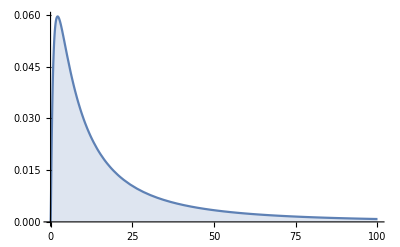
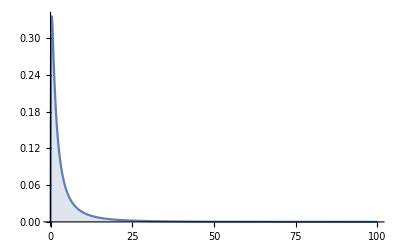
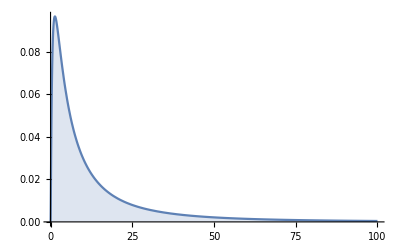
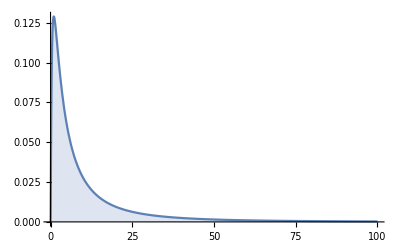
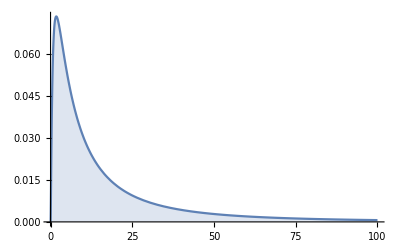
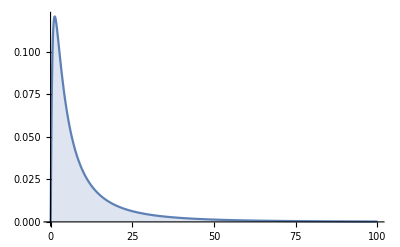
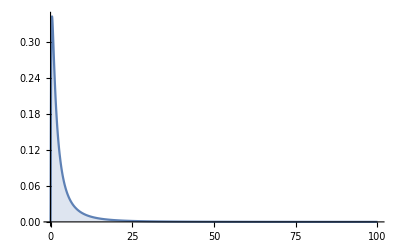
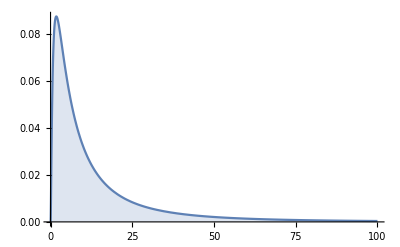

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

```mathematica
Length[parametrosDis]
```

6

#### results1

```mathematica
parametrosDis={{{28.518085539133953,{27.35600607037152,29.736725603113456},{27.35600607037152,29.399032388712996}},{60.49082333773409,{51.323656791150384,77.2726440594583},{51.323656791150384,69.8457058815075}},{3720.439310645581,{2634.1177464157972,5971.061519939736},{2634.1177464157972,4878.422630086051}},{12.077393768760812,{11.695211279251254,12.471899786155971},{11.695211279251254,12.363136012967487}},{4.988268533011079,{4.816390236726899,5.168308948203122},{4.816390236726899,5.117309849992228}},{29.240533181431307,{28.20291009790425,30.277004280842817},{28.20291009790425,30.005412924787557}},{24.257266447132714,{23.266561473812708,25.241193800275255},{23.266561473812708,24.989424142284097}},{11.718168223348384,{6.495092874547247,29.340528141601386},{6.495092874547247,19.94797344330334}}},{{5.052448962882701,{4.848092014680854,5.272296870290326},{4.848092014680854,5.209550648656605}},{10.72901011896947,{9.090595954907833,13.754830453805145},{9.090595954907833,12.39039676664246}},{117.22648694055812,{82.63893481538666,189.19536081292546},{82.63893481538666,153.52193203482395}},{2.140179385112952,{2.0732673337109455,2.209401685403412},{2.0732673337109455,2.1909611692580544}},{0.884048117778372,{0.853035084206564,0.9155007641561026},{0.853035084206564,0.9070269705432501}},{5.1797909510648665,{4.997111837601831,5.366740875356677},{4.997111837601831,5.311875312551374}},{4.296644358207367,{4.1227864663140075,4.474464975511481},{4.1227864663140075,4.424129980114478}},{11.775783614037712,{6.461458147892304,29.589715790463515},{6.461458147892304,19.656301828675485}}},{{17.584790734102725,{16.86316800539464,18.33517135913698},{16.86316800539464,18.12781444025232}},{37.31845819790736,{31.813463165964667,47.85818915188429},{31.813463165964667,43.067684376740544}},{1415.218263674834,{1012.0964386121906,2290.406268897535},{1012.0964386121906,1854.8254375745419}},{7.447279157756265,{7.202657458900539,7.686114467609665},{7.202657458900539,7.622155136931749}},{3.0759424374274547,{2.971177924088894,3.184161094496778},{2.971177924088894,3.153937831644949}},{18.027287095751902,{17.393967483261655,18.662899111034502},{17.393967483261655,18.494650896829715}},{14.9544036708972,{14.351563749818848,15.564617935310189},{14.351563749818848,15.40669247240557}},{11.725980886025733,{6.508346251875871,29.714266880929674},{6.508346251875871,19.73575418322457}}},{{13.147927095584286,{12.605318569345847,13.713262504078576},{12.605318569345847,13.560334762359375}},{27.879290364164383,{23.65174069123848,36.080127829696984},{23.65174069123848,32.24236324940807}},{789.3238461842635,{559.4048377255862,1301.7756242072749},{559.4048377255862,1039.5699879067802}},{5.5714598209904,{5.388654232608952,5.751325764511019},{5.388654232608952,5.702349178538947}},{2.301374544348857,{2.221723807816091,2.3829460591152674},{2.221723807816091,2.360452445935313}},{13.482657764910295,{13.021207676361119,13.955320109972682},{13.021207676361119,13.829970545737718}},{11.183569396888606,{10.748740512053233,11.638334291074848},{10.748740512053233,11.519743249110329}},{11.74029792642136,{6.476354720312248,30.51420245958459},{6.476354720312248,19.973884718816024}}},{{23.142232492234804,{22.213513047768508,24.183827549015753},{22.213513047768508,23.86872145811479}},{49.08076245489589,{41.787318922614546,63.214948130901284},{41.787318922614546,56.845615921410015}},{2444.7222703524353,{1746.1800227402998,3996.12966719254},{1746.1800227402998,3231.424049484464}},{9.804345160776235,{9.494953328941367,10.124568409445132},{9.494953328941367,10.039680231633554}},{4.048443793315977,{3.90872909793693,4.195746698421412},{3.90872909793693,4.152216243974809}},{23.73013706765779,{22.915271578674815,24.568216904410196},{22.915271578674815,24.337027767693797}},{19.685716803599494,{18.901628364702237,20.485568714997186},{18.901628364702237,20.27555428589173}},{11.74895750496846,{6.484872233063681,30.043434638275986},{6.484872233063681,20.036621099329576}}},{{12.070013135038836,{11.642866520542887,12.523081414241366},{11.642866520542887,12.391987516141876}},{22.355991912786052,{19.511779205451326,27.410941729254446},{19.511779205451326,25.112558333343657}},{504.2018197002165,{380.7095277622828,751.3597264845828},{380.7095277622828,630.640586045588}},{5.711946844579642,{5.5426997645917,5.8844481260417165},{5.5426997645917,5.838259827651887}},{2.5031423205978647,{2.4232349226515146,2.584427352480541},{2.4232349226515146,2.5627019979355716}},{13.030781658388374,{12.603899471496142,13.470950843620662},{12.603899471496142,13.348472065245875}},{10.529618183658844,{10.127020714298004,10.951013339792258},{10.127020714298004,10.83302686713661}},{9.741284387889973,{5.728864390713631,23.21883944689201},{5.728864390713631,15.561553626993033}}},{{4.240983519412226,{4.091690790021481,4.40124951819883},{4.091690790021481,4.356356145125545}},{7.845894427047813,{6.857803070518648,9.50262948343725},{6.857803070518648,8.809216680978116}},{62.100617682647965,{47.029462954014996,90.2999670994909},{47.029462954014996,77.6022985324231}},{2.00758597085989,{1.9487598431702153,2.069549533038366},{1.9487598431702153,2.052221449313377}},{0.8796378258710389,{0.8518348192749303,0.9091435865433339},{0.8518348192749303,0.9009914521449393}},{4.5803741102494735,{4.433695175443128,4.730157610556586},{4.433695175443128,4.6909213329602855}},{3.7014460584098647,{3.5608406211840036,3.8439541595545084},{3.5608406211840036,3.8072736582319373}},{9.678618308676393,{5.692945041026559,22.535278804687685},{5.692945041026559,15.308877240268869}}},{{16.655812017123232,{16.04515358317447,17.286289282825315},{16.04515358317447,17.10826036084808}},{30.847895514059083,{26.95811320896064,37.93390294800476},{26.95811320896064,34.73052383480297}},{961.9109468343962,{726.7398677871381,1438.9809928686439},{726.7398677871381,1206.2092858398173}},{7.886498840834737,{7.65009053230011,8.127879089092465},{7.65009053230011,8.06221045426335}},{3.4563953847464313,{3.347167916810753,3.5700827647778195},{3.347167916810753,3.5396404876014587}},{17.990206404121675,{17.402692268912773,18.585908986384137},{17.402692268912773,18.42270451848957}},{14.536688559449406,{13.980949214866145,15.10804819880904},{13.980949214866145,14.953512266125777}},{9.753209700102726,{5.732873946485538,23.442144260331407},{5.732873946485538,15.523104320705578}}},{{12.833421718696746,{12.379328273129895,13.304376012582251},{12.379328273129895,13.173568046010065}},{23.78138609369099,{20.780415232390045,29.13230955799222},{20.780415232390045,26.780668267148545}},{571.0395268813678,{431.82565723054825,848.6914601826849},{431.82565723054825,717.2041928350571}},{6.075745678846104,{5.895744776118921,6.260480337855602},{5.895744776118921,6.211047478718866}},{2.6630998743159964,{2.5780489622727836,2.751623874699662},{2.5780489622727836,2.7277273395096757}},{13.85849858897361,{13.413962165494004,14.314506686414488},{13.413962165494004,14.193087480189842}},{11.197579917358116,{10.773537255665293,11.631525396441543},{10.773537255665293,11.515705784512786}},{9.791952585473771,{5.739927225180658,23.84930758909954},{5.739927225180658,15.774327971418375}}},{{21.15432602498033,{20.39618841319308,21.950289308382047},{20.39618841319308,21.722553304141822}},{39.16230558253863,{34.23126800703327,47.684585511162865},{34.23126800703327,44.06887834817774}},{1547.365362883443,{1171.7797093693396,2273.8196953714037},{1171.7797093693396,1942.0660388664887}},{10.01479029665393,{9.713175831755478,10.319063369128372},{9.713175831755478,10.239142441314968}},{4.3889522717627445,{4.246148156990685,4.534611026414366},{4.246148156990685,4.493946665247189}},{22.843910490205257,{22.107330698891808,23.601411285225574},{22.107330698891808,23.397342119042086}},{18.45856925716935,{17.756905682697333,19.182723361082694},{17.756905682697333,18.983284507223587}},{9.73272228997154,{5.728655228360488,23.073335139729554},{5.728655228360488,15.779057332705701}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"HRDW1","HRDW2","HRDW3","HRDW4","HRDW5","ICURDW1","ICURDW2","ICURDW3","ICURDW4","ICURDW5"}->parametrosDis[[All,4,{1,2}]]]
```

{HRDW1→{12.0774,{11.6952,12.4719}},HRDW2→{2.14018,{2.07327,2.2094}},HRDW3→{7.44728,{7.20266,7.68611}},HRDW4→{5.57146,{5.38865,5.75133}},HRDW5→{9.80435,{9.49495,10.1246}},ICURDW1→{5.71195,{5.5427,5.88445}},ICURDW2→{2.00759,{1.94876,2.06955}},ICURDW3→{7.8865,{7.65009,8.12788}},ICURDW4→{6.07575,{5.89574,6.26048}},ICURDW5→{10.0148,{9.71318,10.3191}}}

#### IQR

```mathematica
Thread[{"HRDW1","HRDW2","HRDW3","HRDW4","HRDW5","ICURDW1","ICURDW2","ICURDW3","ICURDW4","ICURDW5"}->parametrosDis[[All,5,{1,2}]]]
```

{HRDW1→{4.98827,{4.81639,5.16831}},HRDW2→{0.884048,{0.853035,0.915501}},HRDW3→{3.07594,{2.97118,3.18416}},HRDW4→{2.30137,{2.22172,2.38295}},HRDW5→{4.04844,{3.90873,4.19575}},ICURDW1→{2.50314,{2.42323,2.58443}},ICURDW2→{0.879638,{0.851835,0.909144}},ICURDW3→{3.4564,{3.34717,3.57008}},ICURDW4→{2.6631,{2.57805,2.75162}},ICURDW5→{4.38895,{4.24615,4.53461}}}

```mathematica
Thread[{"HRDW1","HRDW2","HRDW3","HRDW4","HRDW5","ICURDW1","ICURDW2","ICURDW3","ICURDW4","ICURDW5"}->parametrosDis[[All,6,{1,2}]]]
```

{HRDW1→{29.2405,{28.2029,30.277}},HRDW2→{5.17979,{4.99711,5.36674}},HRDW3→{18.0273,{17.394,18.6629}},HRDW4→{13.4827,{13.0212,13.9553}},HRDW5→{23.7301,{22.9153,24.5682}},ICURDW1→{13.0308,{12.6039,13.471}},ICURDW2→{4.58037,{4.4337,4.73016}},ICURDW3→{17.9902,{17.4027,18.5859}},ICURDW4→{13.8585,{13.414,14.3145}},ICURDW5→{22.8439,{22.1073,23.6014}}}

### Sampling adjusted by Peak/Valleys

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[1.64387,1.06233],
LogNormalDistribution[1.64387-1.00838,1.06233],
LogNormalDistribution[1.83096,1.11931],
LogNormalDistribution[1.83096-0.97629,1.11931]};
```

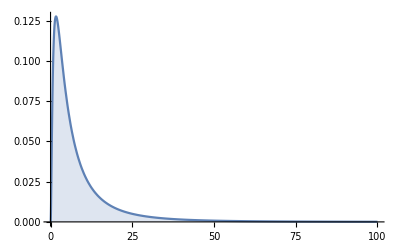
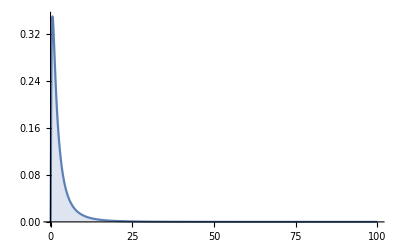
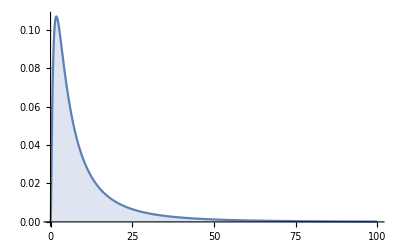
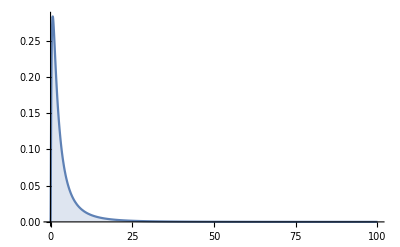

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

```mathematica
Length[parametrosDis]
```

6

#### results1

```mathematica
parametrosDis={{{9.099043132672634,{8.842791603438581,9.361570672362848},{8.842791603438581,9.288107763251238}},{13.145996306774771,{11.941022311440992,15.063369232050103},{11.941022311440992,14.218851028416564}},{173.5267903195511,{142.58801384233158,226.90509262107372},{142.58801384233158,202.17572456830277}},{5.17535642322863,{5.042825322325842,5.311002405315123},{5.042825322325842,5.275056459360577}},{2.527485446162765,{2.456832049794072,2.6009571490420678},{2.456832049794072,2.5813553222466763}},{10.592496775812172,{10.30113065975585,10.893433404028174},{10.30113065975585,10.809643355713854}},{8.066340521926838,{7.789638106215958,8.350784652402034},{7.789638106215958,8.27333626143038}},{6.82765783596915,{4.495556784464249,14.365476306050406},{4.495556784464249,9.835524912700123}}},{{3.318622006847654,{3.2262334032147453,3.4127668133249185},{3.2262334032147453,3.388000875243107}},{4.788054551541934,{4.355373845785514,5.44435806508821},{4.355373845785514,5.186382565682498}},{23.0090702121231,{18.9692813365525,29.641034740891033},{18.9692813365525,26.898564117615372}},{1.8881144049720813,{1.839857956725241,1.9382336018349564},{1.839857956725241,1.9246806485870307}},{0.9219935615382303,{0.896150850313192,0.9482695449772359},{0.896150850313192,0.9411925923341626}},{3.8648402349978497,{3.757579294508564,3.9743309281953705},{3.757579294508564,3.945620000412392}},{2.9433383022778044,{2.841895608409204,3.048998180812084},{2.841895608409204,3.0201725052648323}},{6.77478826160873,{4.482967931734344,13.633433267076445},{4.482967931734344,9.803689927895297}}},{{11.673987906758486,{11.327498513589433,12.046822243062241},{11.327498513589433,11.943411819278573}},{18.39050975091801,{16.54773207949213,21.34284310621734},{16.54773207949213,20.167824976201732}},{339.79876446909685,{273.82743697465287,455.516951856609},{273.82743697465287,406.74116427070635}},{6.2412969220307835,{6.069745540319685,6.419175759332697},{6.069745540319685,6.368211483323272}},{2.933198489526648,{2.8468318179656857,3.0224773779113336},{2.8468318179656857,2.997448611198315}},{13.275520794095687,{12.880381968743794,13.670670085348847},{12.880381968743794,13.563593294671909}},{10.344136030112216,{9.97409287881445,10.722657471753694},{9.97409287881445,10.621155743709048}},{7.665702613428301,{4.933386554958031,16.303987176685848},{4.933386554958031,11.491213798788632}}},{{4.397909673322861,{4.264992938663045,4.5380181910326325},{4.264992938663045,4.49821217485703}},{6.938784113632486,{6.244807836153069,8.049979250894356},{6.244807836153069,7.602169621575945}},{48.39235566968413,{38.997624910478784,64.80216593982968},{38.997624910478784,57.79298295521215}},{2.3504354856682705,{2.2857789170502123,2.4167868981017073},{2.2857789170502123,2.3976152493500815}},{1.1046198238159393,{1.072240484742944,1.1378692313723553},{1.072240484742944,1.1290522452972946}},{5.000234640382336,{4.850615614514983,5.151871619692734},{4.850615614514983,5.112721699188451}},{3.896297300247218,{3.7540579904636866,4.041600030762954},{3.7540579904636866,4.002459146525326}},{7.7368173578429325,{4.926309472978344,16.26540520285791},{4.926309472978344,11.553256324345112}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"HRDP","HRDV","ICURDP","ICURDV"}->parametrosDis[[All,4,{1,2}]]]
```

{HRDP→{5.17536,{5.04283,5.311}},HRDV→{1.88811,{1.83986,1.93823}},ICURDP→{6.2413,{6.06975,6.41918}},ICURDV→{2.35044,{2.28578,2.41679}}}

#### IQR

```mathematica
Thread[{"HRDP","HRDV","ICURDP","ICURDV"}->parametrosDis[[All,5,{1,2}]]]
```

{HRDP→{2.52749,{2.45683,2.60096}},HRDV→{0.921994,{0.896151,0.94827}},ICURDP→{2.9332,{2.84683,3.02248}},ICURDV→{1.10462,{1.07224,1.13787}}}

```mathematica
Thread[{"HRDP","HRDV","ICURDP","ICURDV"}->parametrosDis[[All,6,{1,2}]]]
```

{HRDP→{10.5925,{10.3011,10.8934}},HRDV→{3.86484,{3.75758,3.97433}},ICURDP→{13.2755,{12.8804,13.6707}},ICURDV→{5.00023,{4.85062,5.15187}}}

### Sampling adjusted by R/D

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[1.32391,1.60889],
LogNormalDistribution[1.32391+0.66325,1.60889],
LogNormalDistribution[1.64698,1.40984],
LogNormalDistribution[1.64698+0.44388,1.40984]};
```

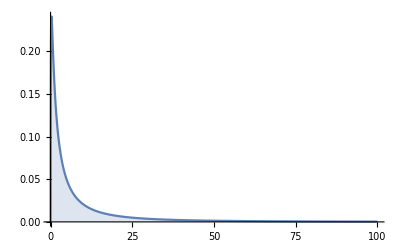
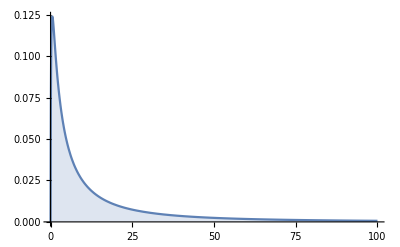
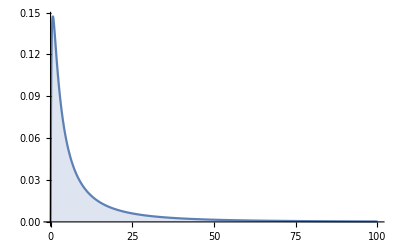
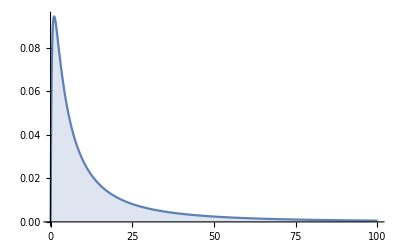

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

```mathematica
Length[parametrosDis]
```

6

#### results1

```mathematica
parametrosDis={{{13.70873564575828,{12.858053964575355,14.694129273723723},{12.858053964575355,14.389770389770757}},{46.2593758481492,{34.784489176692226,73.0733197700082},{34.784489176692226,59.658767509923784}},{2281.2530539828754,{1209.9606872834188,5339.7100622098715},{1209.9606872834188,3559.168540803138}},{3.7593011943045176,{3.612057032608867,3.9124543690568294},{3.612057032608867,3.8702626615705027}},{1.2698756855058144,{1.2155608645776044,1.3256120502638282},{1.2155608645776044,1.3104451806946058}},{11.124628320121529,{10.647402324349507,11.618525252225464},{10.647402324349507,11.479630333174265}},{9.857255793973277,{9.397661776431464,10.344166316429593},{9.397661776431464,10.202815425341397}},{19.8141193808045,{9.346537970624636,54.87369328428075},{9.346537970624636,37.201050406804676}}},{{26.62239043581072,{24.966930058805016,28.551843341888745},{24.966930058805016,27.98418611658075}},{90.38363740978241,{67.57848875614144,146.6995669440563},{67.57848875614144,117.04697766115004}},{8823.094871542075,{4566.852142563936,21520.762941573656},{4566.852142563936,13699.994979609757}},{7.299017086089997,{7.017037783433116,7.5833784466697445},{7.017037783433116,7.510562813206548}},{2.465178319695452,{2.3632558401966413,2.573696093033321},{2.3632558401966413,2.542690999157587}},{21.59270559402649,{20.695789154171134,22.51529854513788},{20.695789154171134,22.282524723641444}},{19.132443695789316,{18.262304295782435,20.021392715142106},{18.262304295782435,19.798432751010928}},{20.06941525515685,{9.341694823057747,55.41286346199391},{9.341694823057747,37.836410751283445}}},{{14.02324529124269,{13.368128201717793,14.74005153754087},{13.368128201717793,14.529694053534485}},{34.64648973497398,{28.42633397142881,47.16290569400712},{28.42633397142881,41.2659109453814}},{1230.0335926935747,{808.0564630552077,2224.3396735018096},{808.0564630552077,1702.8754061521481}},{5.192809849261222,{5.01482014775674,5.3716398878624005},{5.01482014775674,5.324913249185795}},{2.006213762864157,{1.9312026911069395,2.08175149298979},{1.9312026911069395,2.0616603574956986}},{13.436522712464273,{12.931508456959978,13.950948075313745},{12.931508456959978,13.81170811044371}},{11.432829683127647,{10.947910297471617,11.93035301565725},{10.947910297471617,11.792470891391831}},{14.2120838098567,{7.3895796226144155,37.07696982229618},{7.3895796226144155,24.884472721035134}}},{{21.85715767323416,{20.832747975638817,22.99378316833205},{20.832747975638817,22.652774209386557}},{54.039639472065225,{44.371101430237395,74.049951705269},{44.371101430237395,64.56808272696871}},{2999.0253889124488,{1968.7946421324152,5483.39534755267},{1968.7946421324152,4169.037307036675}},{8.091871896105774,{7.814361899059071,8.371373324892978},{7.814361899059071,8.298094405976638}},{3.1268272513697353,{3.0125232093538954,3.242143928498967},{3.0125232093538954,3.21336701539853}},{20.938509342384975,{20.16752635919438,21.743470061036533},{20.16752635919438,21.516717022922013}},{17.815576216339082,{17.0778256755532,18.59922267434461},{17.0778256755532,18.3766489674597}},{14.145889293299179,{7.44203557743566,37.10149042080285},{7.44203557743566,24.665623486590714}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"HRDD","HRDR","ICURDD","ICURR"}->parametrosDis[[All,4,{1,2}]]]
```

{HRDD→{3.7593,{3.61206,3.91245}},HRDR→{7.29902,{7.01704,7.58338}},ICURDD→{5.19281,{5.01482,5.37164}},ICURR→{8.09187,{7.81436,8.37137}}}

#### IQR

```mathematica
Thread[{"HRDD","HRDR","ICURDD","ICURR"}->parametrosDis[[All,5,{1,2}]]]
```

{HRDD→{1.26988,{1.21556,1.32561}},HRDR→{2.46518,{2.36326,2.5737}},ICURDD→{2.00621,{1.9312,2.08175}},ICURR→{3.12683,{3.01252,3.24214}}}

```mathematica
Thread[{"HRDD","HRDR","ICURDD","ICURR"}->parametrosDis[[All,6,{1,2}]]]
```

{HRDD→{11.1246,{10.6474,11.6185}},HRDR→{21.5927,{20.6958,22.5153}},ICURDD→{13.4365,{12.9315,13.9509}},ICURR→{20.9385,{20.1675,21.7435}}}

### Sampling adjusted by Vaccination Yes/No

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
times={LogNormalDistribution[1.73900,1.61020],LogNormalDistribution[1.73900+0.59026,1.61020],LogNormalDistribution[1.54585,1.37390],LogNormalDistribution[1.54585+0.77244,1.37390]};
```

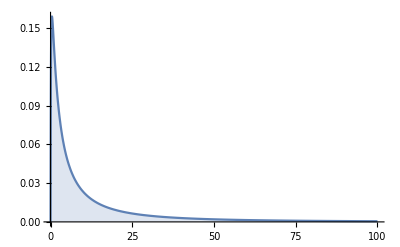
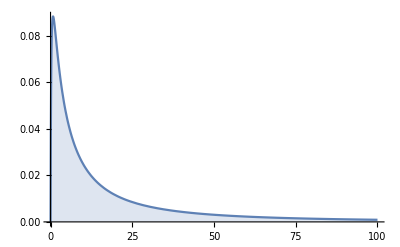
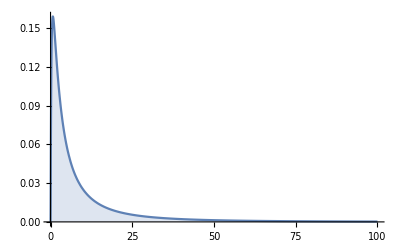
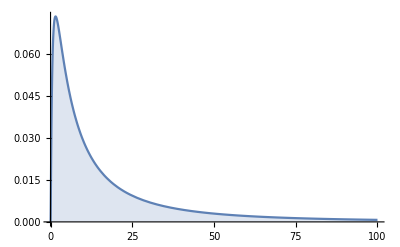

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@times
```

```mathematica
disParameters2[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,times,Method->"CoarsestGrained"]
```

```mathematica
Length[parametrosDis]
```

6

#### results1

```mathematica
parametrosDis={{{20.80370400799932,{19.518938279218233,22.3161877945701},{19.518938279218233,21.886870382497033}},{70.41974348015584,{52.714597768739964,113.13312225903223},{52.714597768739964,91.53530738454111}},{5262.563802501796,{2778.8288179200445,12799.103352077136},{2778.8288179200445,8378.712497982426}},{5.69220579886457,{5.469791506504676,5.922997825251205},{5.469791506504676,5.858940851275431}},{1.9211571607933038,{1.8382045794020394,2.0047419607163692},{1.8382045794020394,1.982857038170892}},{16.85992461239363,{16.1501524081214,17.603410563346994},{16.1501524081214,17.39745024527592}},{14.942619935056793,{14.259247050520937,15.66695899411305},{14.259247050520937,15.466791533795659}},{19.933086526457906,{9.32956512820551,55.140183893908784},{9.32956512820551,37.74816378717999}}},{{37.55403916870442,{35.16520942746635,40.40812697835418},{35.16520942746635,39.46584292283798}},{127.62579487560491,{95.29148297193238,204.4486428998326},{95.29148297193238,164.90915994393455}},{17612.26347384798,{9080.46672699008,41799.247583583274},{9080.46672699008,27195.031033414187}},{10.273163303809001,{9.873738146696725,10.684773559709097},{9.873738146696725,10.57355380121502}},{3.466624929754121,{3.321244392329728,3.618665385333407},{3.321244392329728,3.577476294378969}},{30.423776055601554,{29.153174356268334,31.76433949777364},{29.153174356268334,31.41539714973237}},{26.96403436451793,{25.740216520837265,28.275717114468904},{25.740216520837265,27.92279970505244}},{19.95576680008106,{9.354631169739767,55.36087154190404},{9.354631169739767,37.27278323411345}}},{{12.056948481564064,{11.516642235735242,12.652994426411277},{11.516642235735242,12.481254530939253}},{28.217228022218613,{23.47300504889147,37.56118210677027},{23.47300504889147,33.281816604727894}},{814.5030985203659,{550.9819660252844,1410.842401257959},{550.9819660252844,1107.6793165107413}},{4.6928826048796255,{4.539195385450752,4.849359561224114},{4.539195385450752,4.809044962018246}},{1.8572787854131734,{1.7900197455414062,1.9254545996320627},{1.7900197455414062,1.9078163015872753}},{11.851845721711172,{11.432017703604409,12.292430247159137},{11.432017703604409,12.17115844520182}},{9.996750606411666,{9.585551000911767,10.4173294856162},{9.585551000911767,10.306427560281815}},{13.32250078468525,{7.059549876079596,34.52564415155373},{7.059549876079596,23.287616868702976}}},{{26.10109565110288,{24.940073007527122,27.36405388402906},{24.940073007527122,26.98833354444467}},{61.05528635348539,{50.716436318753814,82.34148200498187},{50.716436318753814,72.24968337347025}},{3808.90212095388,{2572.1569128742112,6780.119658776754},{2572.1569128742112,5220.016747566702}},{10.159629350915065,{9.816721455457852,10.513573484849413},{9.816721455457852,10.416280880987976}},{4.020649313890501,{3.876900946793905,4.170878173515936},{3.876900946793905,4.127953078956128}},{25.658301894803582,{24.735995164260157,26.621048598950754},{24.735995164260157,26.362878532856325}},{21.642407313296314,{20.763124456669992,22.556728878280435},{20.763124456669992,22.322109218083646}},{13.267469374077328,{7.030692493407851,36.08287756026788},{7.030692493407851,22.97490783248771}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"HRDNo","HRDYes","ICURDNo","ICURYes"}->parametrosDis[[All,4,{1,2}]]]
```

{HRDNo→{5.69221,{5.46979,5.923}},HRDYes→{10.2732,{9.87374,10.6848}},ICURDNo→{4.69288,{4.5392,4.84936}},ICURYes→{10.1596,{9.81672,10.5136}}}

#### IQR

```mathematica
Thread[{"HRDNo","HRDYes","ICURDNo","ICURYes"}->parametrosDis[[All,5,{1,2}]]]
```

{HRDNo→{1.92116,{1.8382,2.00474}},HRDYes→{3.46662,{3.32124,3.61867}},ICURDNo→{1.85728,{1.79002,1.92545}},ICURYes→{4.02065,{3.8769,4.17088}}}

```mathematica
Thread[{"HRDNo","HRDYes","ICURDNo","ICURYes"}->parametrosDis[[All,6,{1,2}]]]
```

{HRDNo→{16.8599,{16.1502,17.6034}},HRDYes→{30.4238,{29.1532,31.7643}},ICURDNo→{11.8518,{11.432,12.2924}},ICURYes→{25.6583,{24.736,26.621}}}

### Sampling adjusted by departments

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
hRDDeparment={{1.555855,1.613640},{1.555855+0.036706,1.613640},{1.555855-0.047319,1.613640},{1.555855+0.361602,1.613640},{1.555855+0.271798,1.613640},{1.555855+0.453010,1.613640},{1.555855+0.517694,1.613640},{1.555855+0.085876,1.613640},{1.555855-0.004816,1.613640},{1.555855+0.358779,1.613640},{1.555855-0.127776,1.613640},{1.555855+0.588434,1.613640},{1.555855+0.312406,1.613640},{1.555855+0.612047,1.613640},{1.555855+0.705407,1.613640},{1.555855+0.367834,1.613640},{1.555855+0.551575,1.613640},{1.555855-0.748105,1.613640},{1.555855+0.477216,1.613640},{1.555855-0.451714,1.613640},{1.555855-0.055780,1.613640},{1.555855+0.598353,1.613640},{1.555855-0.203502,1.613640},{1.555855+0.551172,1.613640},{1.555855+0.210961,1.613640},{1.555855+1.149278,1.613640},{1.555855-0.338393,1.613640},{1.5558550+.042507,1.613640},{1.555855+0.452726,1.613640},{1.555855+0.334803,1.613640},{1.5558550+0.383321,1.613640},{1.555855+0.508053,1.613640},{1.555855+0.261172,1.613640},{1.555855+0.250029,1.613640},{1.555855-0.042506,1.613640},{1.555855+0.160563,1.613640}};
```

```mathematica
icuRDDeparment={{2.126368,1.390318},{2.126368-0.521379,1.390318},{2.126368-0.800959,1.390318},{2.126368-0.441619,1.390318},{2.126368-0.404505,1.390318},{2.126368+0.115869,1.390318},{2.126368-0.458808,1.390318},{2.126368-0.330332,1.390318},{2.126368-0.464363,1.390318},{2.126368-0.676498,1.390318},{2.126368-0.684106,1.390318},{2.126368-0.313282,1.390318},{2.126368-0.00453,1.390318},{2.126368-0.433572,1.390318},{2.126368-0.034747,1.390318},{2.126368-0.625346,1.390318},{2.126368-0.576928,1.390318},{2.126368-1.341478,1.390318},{2.126368-0.633889,1.390318},{2.126368-1.309755,1.390318},{2.126368-0.500689,1.390318},{2.126368-0.614682,1.390318},{2.126368-1.006438,1.390318},{2.126368-0.235501,1.390318},{2.126368-0.258461,1.390318},{2.1263680+0.059071,1.390318},{2.126368-1.172896,1.390318},{2.126368-0.521892,1.390318},{2.126368-0.595064,1.390318},{2.126368-0.610119,1.390318},{2.126368-0.455846,1.390318},{2.126368-0.868064,1.390318},{2.126368-0.594899,1.390318},{2.126368-0.334328,1.390318},{2.126368-1.331521,1.390318},{2.126368-0.417546,1.390318}};
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[LogNormalDistribution[#[[1]],#[[2]]],10^4,10^4]&,hRDDeparment,Method->"CoarsestGrained"];
```

#### results1

```mathematica
parametrosDisH={{{17.42598505317008,{16.334184476430384,18.702108302404213},{16.334184476430384,18.30809769027542}},{59.302858122837684,{44.42553255106118,94.85407527455664},{44.42553255106118,76.68882698977923}},{3766.467950662139,{1973.6279424453965,8997.295596191256},{1973.6279424453965,5881.1761850682915}},{4.741642235589184,{4.559881063538395,4.930715329047818},{4.559881063538395,4.88098266760176}},{1.5963094091204126,{1.5283767326159206,1.6652418645938762},{1.5283767326159206,1.6468364946744771}},{14.078470093951584,{13.478390508104168,14.696056974747552},{13.478390508104168,14.532893576277488}},{12.485342768840756,{11.90535887399524,13.08031460354618},{11.90535887399524,12.924361324188325}},{20.063801062767713,{9.4060587299425,54.41459427893553},{9.4060587299425,38.151524275346866}}},{{18.07410428197133,{16.93523169855855,19.414151271615744},{16.93523169855855,19.00398779974941}},{61.54192435909654,{46.12997108715136,98.86080004638511},{46.12997108715136,79.69528931631686}},{4085.7724376628607,{2127.9742325014204,9773.457785811339},{2127.9742325014204,6351.339139211449}},{4.918563964391288,{4.72462040969428,5.117350355290586},{4.72462040969428,5.062916811878955}},{1.6557831940286978,{1.5849251861650333,1.7294826818176117},{1.5849251861650333,1.708765017657899}},{14.60264739370423,{13.980829342992983,15.244531208698215},{13.980829342992983,15.06971174604227}},{12.950208795303988,{12.348322580520795,13.57511175141017},{12.348322580520795,13.39649980520139}},{19.975190591294695,{9.38156120787387,54.89225019866084},{9.38156120787387,37.901947303461945}}},{{16.62256395794758,{15.576062421960934,17.859496015297115},{15.576062421960934,17.486323526113523}},{56.77002427778616,{42.529950323209434,93.02875917074971},{42.529950323209434,74.40956619510177}},{3437.3215361911484,{1808.7966744946625,8654.350032849348},{1808.7966744946625,5536.783541343233}},{4.521807914206574,{4.346341404176291,4.699634063321273},{4.346341404176291,4.655202826188279}},{1.5221644384389208,{1.4574217360994006,1.5891744941727044},{1.4574217360994006,1.570995575908895}},{13.427361539290747,{12.852437439323158,14.020719458912643},{12.852437439323158,13.856225363495856}},{11.90816611187896,{11.352699780209562,12.479847978039308},{11.352699780209562,12.321262458971058}},{20.233318036898446,{9.4622726168061,57.78186003017538},{9.4622726168061,39.09503424875347}}},{{24.99126819140148,{23.3983596793119,26.786904628994513},{23.3983596793119,26.263608718868003}},{84.76893389959305,{63.46227997699394,135.91351195121192},{63.46227997699394,110.28727960057758}},{7619.0358937508,{4027.460979878366,18472.482730912227},{4027.460979878366,12163.284041695975}},{6.804878788306492,{6.5404414580862635,7.079933474481148},{6.5404414580862635,7.004733166846478}},{2.291163260593435,{2.1940738797624073,2.3897055353254117},{2.1940738797624073,2.3638284466899053}},{20.198228761991007,{19.333021383894785,21.07733451613446},{19.333021383894785,20.84862046188999}},{17.911630218160386,{17.076954045332943,18.75394072268511},{17.076954045332943,18.54184688213804}},{19.99205758138002,{9.348342085452577,55.08052514765527},{9.348342085452577,37.735714757638384}}},{{22.87217148823182,{21.401931550122377,24.58019800838918},{21.401931550122377,24.058843171267142}},{78.19127426681057,{58.07537818964737,127.3155517535938},{58.07537818964737,102.13555287581582}},{6560.87771026492,{3372.749551870569,16209.249718322018},{3372.749551870569,10431.671161248569}},{6.22109577691939,{5.981620512177008,6.471358180785566},{5.981620512177008,6.404262990570731}},{2.0946648006223367,{2.0069587103522046,2.18618717092352},{2.0069587103522046,2.161155568542171}},{18.469956197968603,{17.705109278864242,19.27522028008887},{17.705109278864242,19.062228359709202}},{16.37946714396373,{15.645280619587382,17.159347456490618},{15.645280619587382,16.951055914241284}},{20.214638622528597,{9.389497972439038,56.13665083851463},{9.389497972439038,38.96904754049145}}},{{27.393233587596146,{25.67647373791553,29.42468832991243},{25.67647373791553,28.79225629888887}},{93.34044061480054,{69.92573303157481,151.29650491087054},{69.92573303157481,121.55047046541044}},{9334.46523716586,{4889.608140003073,22890.63239824507},{4889.608140003073,14774.516870362617}},{7.456567599394027,{7.167843893060303,7.74961606636821},{7.167843893060303,7.676166197328294}},{2.510783998799191,{2.404520005872947,2.6205738255302116},{2.404520005872947,2.5906381498878273}},{22.133008473880114,{21.196404765110685,23.087990713914984},{21.196404765110685,22.84394544163876}},{19.62729099274936,{18.715719940234617,20.560999770461066},{18.715719940234617,20.316212896874063}},{20.13334650751815,{9.406917210350198,56.053683212173326},{9.406917210350198,38.01087980049688}}},{{29.243211979963036,{27.424219322290256,31.41761611359931},{27.424219322290256,30.74336025752426}},{99.83434348883603,{74.42441538672679,161.24325496792403},{74.42441538672679,131.02257755406447}},{10622.473960219959,{5538.9936056560555,25999.387272650958},{5538.9936056560555,17166.91582891084}},{7.953556514138367,{7.646151853797699,8.271004456489067},{7.646151853797699,8.185718599642936}},{2.6786400840033857,{2.566393791667547,2.7953870326693084},{2.566393791667547,2.7654717787024548}},{23.61161026157603,{22.59483527911195,24.650433672054206},{22.59483527911195,24.36653413929063}},{20.938252065555382,{19.94930203142376,21.94853136523225},{19.94930203142376,21.669159235983965}},{20.2097700526483,{9.41590493630725,56.074496987550845},{9.41590493630725,38.892101427285276}}},{{18.985205904588064,{17.768809733179026,20.39518043280474},{17.768809733179026,19.959910658053357}},{64.81241813975412,{48.377900571884986,105.77376658571995},{48.377900571884986,84.57237983978362}},{4531.601992135286,{2340.4212637431897,11188.089697730367},{2340.4212637431897,7152.487431764638}},{5.164365446747986,{4.961932981099546,5.377573447646529},{4.961932981099546,5.316536085264373}},{1.7387810202519158,{1.6649296440201808,1.8144347117980932},{1.6649296440201808,1.7948325494732909}},{15.33328640109417,{14.693196755999177,16.018024620931204},{14.693196755999177,15.830623528219867}},{13.597959997292413,{12.969411072448207,14.270347575951503},{12.969411072448207,14.077030692138864}},{20.065404454283204,{9.37390209916321,56.6136596847969},{9.37390209916321,37.920694412423444}}},{{17.330922316698395,{16.21244656749317,18.587905217297703},{16.21244656749317,18.22002058907359}},{58.79715859665029,{44.12134830840485,93.44526177237331},{44.12134830840485,76.18681881602883}},{3664.6334335483134,{1946.6933765515796,8732.016947707372},{1946.6933765515796,5804.431361306405}},{4.717299291510813,{4.529903304504247,4.908054500481162},{4.529903304504247,4.855820975733864}},{1.5889135396647027,{1.521977638059337,1.6595674116968357},{1.521977638059337,1.63992036718929}},{14.003655232279556,{13.413061516846497,14.622103517284273},{13.413061516846497,14.447536066801026}},{12.417911942142807,{11.840472734562251,13.014374749807251},{11.840472734562251,12.852245701539633}},{19.888399936820758,{9.455456936544303,54.02380280885612},{9.455456936544303,36.84605485510314}}},{{24.93728711418776,{23.324445062935695,26.769741130295955},{23.324445062935695,26.212745906507177}},{84.96851078063341,{63.3275689369397,138.45743203401318},{63.3275689369397,110.22113024081813}},{7678.484713654234,{4010.3809874628496,19170.460485453383},{4010.3809874628496,12148.697551563393}},{6.786088023236313,{6.526595181781011,7.056918942542676},{6.526595181781011,6.98268949270015}},{2.284641507258402,{2.188032381956137,2.382462619959613},{2.188032381956137,2.3558731832679243}},{20.14672517662577,{19.292607597692363,21.038230053262346},{19.292607597692363,20.788256500737177}},{17.866625386123438,{17.038603054242046,18.737185013335242},{17.038603054242046,18.492984532758882}},{20.18578050172254,{9.364885688430181,56.820253671406384},{9.364885688430181,38.75678282452708}}},{{15.327478050695756,{14.356101027471636,16.43502879366606},{14.356101027471636,16.111773508394528}},{52.20496281891148,{39.04509652150476,84.88499864837732},{39.04509652150476,67.85588392852507}},{2936.900875746765,{1524.5195623736233,7205.462995535019},{1524.5195623736233,4604.420983721468}},{4.171857251394028,{4.009309861714161,4.339049348612464},{4.009309861714161,4.294957972539636}},{1.4044041080746084,{1.3443996899513515,1.4671034640410692},{1.3443996899513515,1.449388323761071}},{12.385616706710126,{11.859758012734632,12.936469307704272},{11.859758012734632,12.78443052997252}},{10.98400458415399,{10.48020072022539,11.516366048505699},{10.48020072022539,11.366176334967523}},{19.964444912616614,{9.359226659808082,56.084656428987344},{9.359226659808082,37.51659655142863}}},{{31.38062510462274,{29.36286762907367,33.7395772148896},{29.36286762907367,33.02745705127738}},{107.07716155966688,{79.66323862669933,175.526806158093},{79.66323862669933,139.5272323010785}},{12283.407789768356,{6346.231588494439,30809.659680060755},{6346.231588494439,19467.848553599124}},{8.539932599062633,{8.208654784754607,8.8779675169017},{8.208654784754607,8.791577802048955}},{2.874825078684551,{2.75301861818664,2.9990759817149137},{2.75301861818664,2.965918329729844}},{25.348045125858963,{24.28844952931617,26.43812861498482},{24.28844952931617,26.162105570418305}},{22.478972103052318,{21.461144498427693,23.537325328668306},{21.461144498427693,23.269699055282658}},{20.081650711200048,{9.423908878324623,55.579748518398965},{9.423908878324623,38.158505317929475}}},{{23.807902100318383,{22.331967947150556,25.570111622445065},{22.331967947150556,25.027819954536245}},{81.14631358847116,{60.80621301008729,130.72366682334993},{60.80621301008729,105.27903697520578}},{7026.339171651828,{3697.3955406281093,17088.6770677422},{3697.3955406281093,11083.675626426748}},{6.478297477461074,{6.225348390043387,6.735462988636497},{6.225348390043387,6.665607071077429}},{2.180746678122466,{2.0888583848492477,2.274276019487322},{2.0888583848492477,2.250668278948171}},{19.226665262798452,{18.41201205086859,20.07910780352123},{18.41201205086859,19.84868305490405}},{17.05017977497131,{16.266255559537605,17.874488983130973},{16.266255559537605,17.651858626337415}},{20.068015990226186,{9.460932858149036,55.41978445503006},{9.460932858149036,37.62051975439597}}},{{32.12831115145787,{30.119093414245377,34.49803861520908},{30.119093414245377,33.777375223142315}},{109.64653740564408,{81.880534234203,176.7887563602623},{81.880534234203,142.11243071488312}},{12900.805160011683,{6704.42188647849,31254.264375408187},{6704.42188647849,20195.942963692454}},{8.742196003165713,{8.407337114677343,9.091482309610857},{8.407337114677343,8.999650349203353}},{2.9432152125701534,{2.8177538628036514,3.0701543072671824},{2.8177538628036514,3.035947879125167}},{25.950942172759998,{24.85558363284662,27.076785892823015},{24.85558363284662,26.790079097610413}},{23.013575804322198,{21.951733258561354,24.107839099493347},{21.951733258561354,23.826138230032214}},{20.08312434068008,{9.42631053544993,55.91464928898744},{9.42631053544993,37.49801979602592}}},{{35.290904554478736,{33.00141640691545,37.99416728424514},{33.00141640691545,37.15941410775924}},{120.79085950497412,{89.4376017136863,195.84044237592695},{89.4376017136863,156.31328919067965}},{15682.305844830924,{7999.084600295984,38353.47886999876},{7999.084600295984,24433.844377609046}},{9.597786768890415,{9.220311255345893,9.972475177238898},{9.220311255345893,9.878728672737253}},{3.231692292028539,{3.095153326649557,3.3698692167402178},{3.095153326649557,3.334305808268396}},{28.49241227680142,{27.28869555446327,29.75207365175112},{27.28869555446327,29.416664030359875}},{25.267129592843173,{24.10145318410489,26.482135034476624},{24.10145318410489,26.156200924037357}},{20.225788529576587,{9.420524623565376,55.46840659254091},{9.420524623565376,38.52514332749641}}},{{25.16656542606808,{23.542474536455014,27.028228341931065},{23.542474536455014,26.472583371882774}},{86.26426328122719,{63.98933454381141,140.4246818686288},{63.98933454381141,112.96915925415281}},{8059.136145466432,{4094.6349353598157,19719.0912779056},{4094.6349353598157,12762.03094259014}},{6.848019875853358,{6.582714758851008,7.125870441003655},{6.582714758851008,7.052407595996797}},{2.305170618177345,{2.2068677436019546,2.406984352681158},{2.2068677436019546,2.3785860702497508}},{20.328077278138423,{19.476055749123613,21.23016781863558},{19.476055749123613,20.987199242742992}},{18.02744922756059,{17.199264872735412,18.910079151275973},{17.199264872735412,18.66873381269355}},{20.29633887208826,{9.339575845267165,57.257211833638756},{9.339575845267165,38.99390316783498}}},{{30.227914297758282,{28.296300732383113,32.45886206470234},{28.296300732383113,31.79126641676504}},{103.09341117451646,{77.1038784007846,166.7680363508713},{77.1038784007846,134.83328622495617}},{11369.270231399223,{5945.008064442976,27811.577948325532},{5945.008064442976,18180.01507422095}},{8.227630757580748,{7.9033480309045006,8.563947626804806},{7.9033480309045006,8.471498579281274}},{2.769907368922799,{2.651080528384165,2.8919929946812415},{2.651080528384165,2.858918880813911}},{24.42611366250964,{23.401818598861624,25.519961128977965},{23.401818598861624,25.210190726456684}},{21.66170546932223,{20.66994565472226,22.715698506058697},{20.66994565472226,22.423435511133697}},{20.147806315955513,{9.519510579904951,56.144810495129505},{9.519510579904951,38.590242890601374}}},{{8.244184727063109,{7.727502382942847,8.851649705027981},{7.727502382942847,8.66538833654449}},{28.2885739577892,{20.961751574387,46.695833157091826},{20.961751574387,36.83329477270545}},{887.9610540620868,{439.3950290663159,2180.5008342349565},{439.3950290663159,1356.6916038130107}},{2.2425539677993607,{2.155881709230135,2.333293555094083},{2.155881709230135,2.3093063155235622}},{0.7553042060193673,{0.7228456459522936,0.7878243015895618},{0.7228456459522936,0.7795051422611055}},{6.657161876803494,{6.372119603085053,6.946540011347782},{6.372119603085053,6.866759884579961}},{5.903358463557757,{5.626193737219874,6.180037566230528},{5.626193737219874,6.10622780279665}},{20.39830379962972,{9.4317586401655,58.36537240043291},{9.4317586401655,39.194667061115254}}},{{28.08176762149082,{26.318281735144964,30.132462889725925},{26.318281735144964,29.521619814160314}},{95.61788249932577,{71.73380655830026,154.2407751965146},{71.73380655830026,124.51454471936303}},{9838.307453515563,{5145.73900334364,23790.216733221754},{5145.73900334364,15503.871846670258}},{7.641096303833014,{7.340931294428435,7.948608620069583},{7.340931294428435,7.865595399662196}},{2.5725392293263414,{2.4636608418038564,2.6837405080177885},{2.4636608418038564,2.6529081718266982}},{22.68247175296917,{21.72150803900098,23.668630973106847},{21.72150803900098,23.409670620239456}},{20.115153412756392,{19.17863459410586,21.070918770602315},{19.17863459410586,20.824861161114427}},{19.970500666106084,{9.431351895052664,54.69696535065507},{9.431351895052664,37.52166820215225}}},{{11.088093395031677,{10.391622027138812,11.902506641515208},{10.391622027138812,11.656531390830592}},{37.6489973919857,{28.292371804285743,59.489089610735334},{28.292371804285743,48.47439436015823}},{1509.5444527020347,{800.4583023119428,3538.951782714099},{800.4583023119428,2349.76690858414}},{3.0171836638709952,{2.8977572092312824,3.142416639547447},{2.8977572092312824,3.107498661122853}},{1.0157983947839169,{0.9723069743082982,1.0612659093636678},{0.9723069743082982,1.0487393528051538}},{8.956993569646581,{8.57938506720514,9.338817698060264},{8.57938506720514,9.241813208769756}},{7.943236448233944,{7.579577307951322,8.311832107392545},{7.579577307951322,8.219966556824392}},{19.920868212470342,{9.396857872655275,52.64786106965204},{9.396857872655275,36.895388127018315}}},{{16.482933447048232,{15.435319185290517,17.747423102419127},{15.435319185290517,17.339070299071846}},{56.30250217908924,{42.043517242306905,91.75347468745478},{42.043517242306905,73.17193518528049}},{3414.4844904131187,{1767.657342104158,8418.700117221406},{1767.657342104158,5354.132098758889}},{4.483588451683322,{4.307665220855391,4.659584272906523},{4.307665220855391,4.612823471203879}},{1.5094994383131446,{1.4440377176289652,1.5752973750814752},{1.4440377176289652,1.5566092652144525}},{13.304148290127097,{12.740666288982219,13.88446982160044},{12.740666288982219,13.721898210843364}},{11.797643206251497,{11.25134079083517,12.354786234112154},{11.25134079083517,12.20300343809653}},{20.09546305910587,{9.467146827788467,55.428098688260334},{9.467146827788467,37.91520878266126}}},{{31.697977317467377,{29.6915776814927,34.0973694584155},{29.6915776814927,33.3507052592691}},{108.19811818142222,{80.91491974143045,175.12242772635204},{80.91491974143045,141.40469177549917}},{12512.0533424917,{6547.224236762131,30667.8646927714},{6547.224236762131,19995.286856123927}},{8.620218683567183,{8.288195760254238,8.967001082975973},{8.288195760254238,8.87217721078878}},{2.9022434605776093,{2.779330185765838,3.0294786788359707},{2.779330185765838,2.9945673660261254}},{25.595621131764236,{24.501949755659098,26.69625443344584},{24.501949755659098,26.40479367390984}},{22.699103943683017,{21.64287924719712,23.761009897503445},{21.64287924719712,23.479715227509}},{20.203026872498043,{9.450302766483805,56.476010307897866},{9.450302766483805,38.298760623619856}}},{{14.217038725894454,{13.319721003761206,15.277829808891303},{13.319721003761206,14.949315630161827}},{48.62928914269781,{36.205707572786956,78.14437737654615},{36.205707572786956,63.91026300417673}},{2554.7241300616683,{1310.8532608461628,6106.5437155680565},{1310.8532608461628,4084.5217172630405}},{3.866483748383168,{3.715264781579363,4.027896962526778},{3.715264781579363,3.9817020053663095}},{1.3020619225510335,{1.2461369454823246,1.3595205898446834},{1.2461369454823246,1.3437246213800225}},{11.477055607362676,{10.990191002591349,11.967462686283772},{10.990191002591349,11.844014648328427}},{10.17757423245694,{9.709554225243808,10.655702940082534},{9.709554225243808,10.529212758008155}},{20.20986793495548,{9.450638740466955,56.373602876770306},{9.450638740466955,38.88792821558202}}},{{30.237659193234343,{28.33895914215428,32.41126669973286},{28.33895914215428,31.783804087490473}},{103.19473400569092,{77.01054284580907,164.2582969694115},{77.01054284580907,134.01580621406015}},{11381.392321959604,{5930.623709406194,26980.78812329138},{5930.623709406194,17960.23631520452}},{8.227199097434871,{7.899725269807463,8.564071827690675},{7.899725269807463,8.47288086036176}},{2.7696177428533715,{2.654794264762701,2.894588645919072},{2.654794264762701,2.859070247909366}},{24.423357317044644,{23.402658261687364,25.526474213104166},{23.402658261687364,25.20654423690963}},{21.65921411547152,{20.66386553907488,22.734457893549997},{20.66386553907488,22.41566425966578}},{20.17288904210452,{9.44537603946954,55.5365637427836},{9.44537603946954,38.207056503559706}}},{{21.514967420381318,{20.146138463811692,23.1225740226335},{20.146138463811692,22.6098424012206}},{73.60899448051482,{54.763043933766625,119.44858730327915},{54.763043933766625,96.10585195216211}},{5896.542316314469,{2998.990980891653,14267.965008749103},{2998.990980891653,9236.3347794509}},{5.855289682899085,{5.632574549622483,6.088604081445223},{5.632574549622483,6.027663733522957}},{1.9719283167243757,{1.8876660090617396,2.056030335829585},{1.8876660090617396,2.0343349753705557}},{17.38001506394091,{16.63011272744883,18.145253325664644},{16.63011272744883,17.936940650579302}},{15.412014124060402,{14.69238910776409,16.148842641563867},{14.69238910776409,15.956863603648262}},{20.14739739877824,{9.43220957389712,56.9176519668816},{9.43220957389712,38.40116564078035}}},{{54.97117871073872,{51.46971297235454,59.0355786067612},{51.46971297235454,57.76210410397523}},{187.36833295451225,{139.67301928145696,307.9325385124138},{139.67301928145696,242.14805130304725}},{38336.98388187244,{19508.55231519825,94822.44827469921},{19508.55231519825,58635.67874986321}},{14.959719744983648,{14.366392466506012,15.57134758642215},{14.366392466506012,15.40191256989388}},{5.037277520315102,{4.823029316981207,5.255757760428497},{4.823029316981207,5.197056245573779}},{44.40567703651119,{42.525540681525136,46.34696567455871},{42.525540681525136,45.808939131778175}},{39.3784498958842,{37.56283742541682,41.25908165617117},{37.56283742541682,40.734692756172365}},{19.973242359034668,{9.403321340125245,55.96143306042477},{9.403321340125245,37.70644513374389}}},{{12.415679554840548,{11.63644021502278,13.359835182399713},{11.63644021502278,13.066294538070892}},{42.37024869922453,{31.63198816042126,68.72254833585073},{31.63198816042126,55.425682406497245}},{1921.324108985474,{1000.5826749810306,4722.78864977334},{1000.5826749810306,3072.006270225898}},{3.3789985635009434,{3.248407176058585,3.5138777681327484},{3.248407176058585,3.4774487960846505}},{1.1377135565935044,{1.0900041059469228,1.188785420254347},{1.0900041059469228,1.174372272259959}},{10.03117175579837,{9.604951318809892,10.471047144987903},{9.604951318809892,10.351291246866616}},{8.89578887136274,{8.486302949767351,9.326007288314518},{8.486302949767351,9.205532792649876}},{20.152328815869424,{9.352768030839329,56.867077911255414},{9.352768030839329,37.534079339564165}}},{{18.172622801660918,{17.03123456433227,19.49698192978884},{17.03123456433227,19.10229162486388}},{61.99932201087157,{46.31779629742109,101.55419772399138},{46.31779629742109,80.4171586489472}},{4142.639271006779,{2145.3382538493947,10313.255075363537},{2145.3382538493947,6466.919405169943}},{4.945785453041244,{4.750905877939838,5.147642023983352},{4.750905877939838,5.091405785296594}},{1.6653706694674248,{1.5945969052231852,1.739097501442844},{1.5945969052231852,1.7191713638516986}},{14.676980545032427,{14.032951420578842,15.330679759750325},{14.032951420578842,15.152975455993978}},{13.014919718705837,{12.394794099499666,13.645349251392892},{12.394794099499666,13.471739550898715}},{20.104094767017884,{9.348445794946421,56.77386998077197},{9.348445794946421,37.64569219991281}}},{{27.401986974102417,{25.685641198717818,29.471183246238972},{25.685641198717818,28.847344416414824}},{93.29532797122688,{69.78689743334077,148.40543039554873},{69.78689743334077,120.48890537859334}},{9309.964798225301,{4870.211053371625,22024.171770888064},{4870.211053371625,14517.576319331622}},{7.454010799826647,{7.158353550625211,7.75165720064571},{7.158353550625211,7.67208572570528}},{2.5090690735279937,{2.402913276877332,2.6186299618125823},{2.402913276877332,2.5892970494562912}},{22.127029291100516,{21.21130182692628,23.121145992356794},{21.21130182692628,22.837650174547754}},{19.62300734126243,{18.738382619119445,20.58154553952032},{18.738382619119445,20.314907585311627}},{19.939693634183314,{9.356970849156106,54.199134160659575},{9.356970849156106,37.73225592903464}}},{{24.350948354744258,{22.813776783493985,26.15248162474635},{22.813776783493985,25.60885997802402}},{82.97313132957666,{62.11072653477974,133.77303696566753},{62.11072653477974,107.49472707241897}},{7370.674924705801,{3857.7423506781915,17895.22541901785},{3857.7423506781915,11555.116348373842}},{6.626184343635431,{6.373146710344978,6.8939605376911475},{6.373146710344978,6.8188804315526514}},{2.231018297840134,{2.137179159891754,2.3269282668584057},{2.137179159891754,2.302221918145475}},{19.66773222159237,{18.856822548186624,20.51699627584359},{18.856822548186624,20.29539750846981}},{17.44109807991006,{16.655073558078257,18.262305312709454},{16.655073558078257,18.050757036002214}},{20.06357460545981,{9.444939297775113,55.258048715838285},{9.444939297775113,37.813433646765894}}},{{25.558101931749995,{23.942304881950637,27.47679735622813},{23.942304881950637,26.88260864718902}},{86.9710887869547,{65.20503774514106,139.5015589056566},{65.20503774514106,112.78638676517369}},{8200.004276048689,{4251.69694734527,19460.684937108374},{4251.69694734527,12720.769039543346}},{6.9556097188150074,{6.686399853095162,7.242368338395764},{6.686399853095162,7.161711190083378}},{2.3424562976877614,{2.2420692783281106,2.4468366031233666},{2.2420692783281106,2.419163390473593}},{20.650500696575392,{19.77621123589137,21.557844806290316},{19.77621123589137,21.30893471635801}},{18.312625638242178,{17.4616130947238,19.187194577488494},{17.4616130947238,18.947351843849468}},{19.89776787827805,{9.377123102484022,54.47511785826937},{9.377123102484022,37.49226449631502}}},{{28.96871706887247,{27.148780940548924,31.093880875212037},{27.148780940548924,30.49401108547582}},{98.95752073319105,{73.6507338888904,160.47740986553805},{73.6507338888904,128.24964326516982}},{10535.447210877772,{5424.430602372149,25752.99907715189},{5424.430602372149,16447.97099764332}},{7.880707563141362,{7.572937819276962,8.19498818077772},{7.572937819276962,8.108109857573321}},{2.653772039363718,{2.542712017242957,2.768905450584097},{2.542712017242957,2.738085461335146}},{23.391894383835826,{22.423193384631062,24.398642238261026},{22.423193384631062,24.143866466560617}},{20.74327976904549,{19.798616383710105,21.721144776253375},{19.798616383710105,21.467672225129004}},{20.11635963495268,{9.336071186808205,56.92449567067807},{9.336071186808205,38.185380952116844}}},{{22.630755372982915,{21.17500074689777,24.333539830809382},{21.17500074689777,23.808487360568602}},{77.20688925209096,{57.64044716238646,126.12549260786501},{57.64044716238646,100.78250057115176}},{6365.5739137991995,{3322.421149079865,15907.639885576613},{3322.421149079865,10157.112421374204}},{6.1541719506618335,{5.918053255599502,6.400528742194535},{5.918053255599502,6.332375785615486}},{2.0724671437883013,{1.983678571942932,2.1639815347648406},{1.983678571942932,2.1393374490004105}},{18.274423952389437,{17.496664846525878,19.095110221225664},{17.496664846525878,18.87012912354783}},{16.20604089764196,{15.447048809089766,17.003377613725576},{15.447048809089766,16.781578323613857}},{20.100274916858336,{9.446138858227034,55.55248212170226},{9.446138858227034,38.01844293129575}}},{{22.381397752098106,{20.960609932072867,24.057604569938068},{20.960609932072867,23.521538257531486}},{76.21738464526629,{57.082758981591,122.1741528487837},{57.082758981591,99.16882203390131}},{6205.867476983851,{3258.4413729504076,14926.523624317964},{3258.4413729504076,9834.45526359159}},{6.085581216039792,{5.848483732239703,6.3319821238412235},{5.848483732239703,6.262221998616523}},{2.049401817056605,{1.9639697671782281,2.1402525219807416},{1.9639697671782281,2.1148231367783494}},{18.071647518070268,{17.29795694903555,18.86612867081879},{17.29795694903555,18.642815438748503}},{16.02639510684035,{15.28499080003305,16.796044746335838},{15.28499080003305,16.57821010283393}},{19.95879637167018,{9.422114031335925,55.53207266987352},{9.422114031335925,37.49071626673212}}},{{16.701734541457977,{15.627620892144716,17.947889523325763},{15.627620892144716,17.558023521486042}},{57.01000485366841,{42.59743924380702,92.0212134688704},{42.59743924380702,74.20366492644114}},{3483.641611866221,{1814.5418301298303,8467.903728283414},{1814.5418301298303,5506.18388851555}},{4.543620501287871,{4.362755885729301,4.72584569500324},{4.362755885729301,4.677431382027511}},{1.529709521513968,{1.46415975042211,1.5969706391161214},{1.46415975042211,1.5780144236267368}},{13.485550816114488,{12.922475264698218,14.08150658886831},{12.922475264698218,13.912126600906575}},{11.958870610948143,{11.416372060834961,12.532237120696022},{11.416372060834961,12.377294796301635}},{20.11632038960968,{9.487331523413474,54.59216521793079},{9.487331523413474,38.17208736274704}}},{{20.457232579265902,{19.16629416764079,21.966603688969663},{19.16629416764079,21.52112221150449}},{69.97492445367966,{52.18668533004901,114.03846194202269},{52.18668533004901,91.00289498891858}},{5305.216065100791,{2723.4501257375523,13004.770802102157},{2723.4501257375523,8281.526896364143}},{5.566302829905221,{5.35130497078886,5.784340755824546},{5.35130497078886,5.729337285252293}},{1.8739393171185765,{1.7949449324284235,1.955641792475681},{1.7949449324284235,1.934121207646021}},{16.523203769006038,{15.823911987130762,17.25163496797865},{15.823911987130762,17.050163640810414}},{14.652998468439991,{13.973968607477314,15.367484558320061},{13.973968607477314,15.164733163414674}},{20.198040757968894,{9.448799280636326,54.962552902526284},{9.448799280636326,38.69151786809527}}}};
```

```mathematica
parametrosDisICU={{{22.041028422869807,{21.0479549753112,23.150599557972335},{21.0479549753112,22.817123843421875}},{52.95081447384054,{43.819418546249025,71.86780439972921},{43.819418546249025,62.73732734901357}},{2877.74287493451,{1920.1414417313533,5164.981309237737},{1920.1414417313533,3935.9722428972855}},{8.385697894890276,{8.104335023279166,8.676073180330448},{8.104335023279166,8.59722663636669}},{3.2826542050584604,{3.1629777288601444,3.4068125306495753},{3.1629777288601444,3.371755048220082}},{21.41300001698716,{20.640706356093233,22.218417889686695},{20.640706356093233,22.004576813727486}},{18.134291190494952,{17.389419877735193,18.902533084392964},{17.389419877735193,18.705119881101595}},{13.683115606104268,{7.241787794384568,35.10931975990178},{7.241787794384568,23.830876811412807}}},{{13.084897681242767,{12.492499688917388,13.734571813842376},{12.492499688917388,13.541981568670124}},{31.432333425133507,{25.94158316510053,42.47675928020643},{25.94158316510053,37.13613652604663}},{1013.3339470526151,{672.9657371118271,1804.2750789486029},{672.9657371118271,1379.0926360811745}},{4.978789316311313,{4.810262629204588,5.149220714738266},{4.810262629204588,5.104003075126002}},{1.9486280291911156,{1.8775759492588466,2.021590181907285},{1.8775759492588466,2.002475260390673}},{12.711354095843857,{12.241878151943478,13.1886891477576},{12.241878151943478,13.057131772525562}},{10.76514784924053,{10.315221667804748,11.225555775427399},{10.315221667804748,11.098163717740123}},{13.759760135211076,{7.231363357558797,36.833954823849474},{7.231363357558797,24.024079998179044}}},{{9.894782882277639,{9.447072141379296,10.397610221910742},{9.447072141379296,10.250476225529349}},{23.81367317875102,{19.625731971013796,32.635596306578215},{19.625731971013796,28.428614526970893}},{583.8852680530698,{385.169355398073,1065.0821462859417},{385.169355398073,808.1861239231005}},{3.7642204799566943,{3.6374068021539356,3.8937503161638953},{3.6374068021539356,3.858244317342817}},{1.4736057548997368,{1.4197635789746117,1.527564187683514},{1.4197635789746117,1.5142085670005923}},{9.612563345221467,{9.261401569466594,9.980843153881377},{9.261401569466594,9.87598374180389}},{8.140736821968176,{7.800052147448954,8.492309684698757},{7.800052147448954,8.39396294834946}},{13.807914300115895,{7.219758351031653,37.12704832874578},{7.219758351031653,24.274496666653135}}},{{14.176481432537956,{13.52332973094597,14.888813342801042},{13.52332973094597,14.68625508389316}},{33.968242386953825,{28.10656708909985,45.63765142402919},{28.10656708909985,40.45813362428421}},{1177.2109480748468,{789.979113534071,2082.795227501193},{789.979113534071,1636.8605763604362}},{5.393628164684325,{5.2099021589264405,5.5837141138991715},{5.2099021589264405,5.530643972526604}},{2.110737712374247,{2.03300105448082,2.1905717515236276},{2.03300105448082,2.1688164130186567}},{13.771929970848781,{13.262952592640788,14.289474591395487},{13.262952592640788,14.145926153719577}},{11.663723266126949,{11.179359609564315,12.159203143264946},{11.179359609564315,12.025746048120912}},{13.579691578577272,{7.218869966052213,35.24639497041777},{7.218869966052213,23.54924054761243}}},{{14.705767675332893,{14.045943578714779,15.440236889186245},{14.045943578714779,15.230577367857133}},{35.25147578171615,{29.182396837874787,47.43186986557092},{29.182396837874787,41.857299300627616}},{1271.080343409371,{851.6122852032044,2249.7822789444544},{851.6122852032044,1752.0335047423214}},{5.594344294116756,{5.409107995809029,5.784249284346323},{5.409107995809029,5.735804673976763}},{2.190211875109755,{2.1111165790365076,2.272014350449244},{2.1111165790365076,2.249542698960673}},{14.28805853188173,{13.772621374989265,14.823270393405604},{13.772621374989265,14.683412956345727}},{12.100480042440811,{11.608803614486787,12.615105916954297},{11.608803614486787,12.479181885577312}},{13.64769731026926,{7.2053854511244175,35.70601703330879},{7.2053854511244175,23.688267796878172}}},{{24.73463686883024,{23.597948854565722,25.978283566319558},{23.597948854565722,25.62804062253231}},{59.30211731776795,{49.04637157983542,79.89250489163122},{49.04637157983542,70.18747378080826}},{3604.2917725908733,{2405.5465651472878,6382.812337859319},{2405.5465651472878,4926.281475731647}},{9.414635956128564,{9.093853134859014,9.739208071338476},{9.093853134859014,9.652570020442027}},{3.685413556617694,{3.5476414810051495,3.824861571806628},{3.5476414810051495,3.78911358508606}},{24.044290381214843,{23.15718770393921,24.96185865413833},{23.15718770393921,24.716961164724523}},{20.363206726275248,{19.525912581380986,21.24819445178209},{19.525912581380986,21.002222685684416}},{13.661948998875587,{7.244347833684874,36.12605089984879},{7.244347833684874,23.751312106885337}}},{{13.93255861624481,{13.29118274186166,14.604243661671173},{13.29118274186166,14.427263499177567}},{33.53742226089781,{27.66150443774823,45.3015216741741},{27.66150443774823,39.869624951346005}},{1160.715235296409,{765.1588277595652,2052.2278659956655},{765.1588277595652,1589.5869937609918}},{5.301108934799817,{5.118518743597781,5.486226892749287},{5.118518743597781,5.4365283882688615}},{2.07488453400488,{1.9976089355355064,2.152135745637563},{1.9976089355355064,2.1307729571953735}},{13.534841985594882,{13.031565146385642,14.045868027775212},{13.031565146385642,13.909589696563328}},{11.462418997869008,{10.984649549543294,11.953580181462879},{10.984649549543294,11.823327703625017}},{13.859076695734661,{7.203531353420905,36.74918020168501},{7.203531353420905,24.644414297041514}}},{{15.844218971461206,{15.121070991115278,16.64429765950736},{15.121070991115278,16.399945963885703}},{38.04381228888377,{31.474902529492574,51.87172761635566},{31.474902529492574,45.01202113916271}},{1486.113718042059,{990.669489241058,2690.6761259053947},{990.669489241058,2026.082047032431}},{6.029132471141854,{5.827723668513242,6.232827550942895},{5.827723668513242,6.179058878509673}},{2.359244070993313,{2.273747265986909,2.4464528388457256},{2.273747265986909,2.4228392862167083}},{15.39257939882389,{14.830228652297846,15.98509692864401},{14.830228652297846,15.817500082268767}},{13.036158627721449,{12.488541403401694,13.610798274057592},{12.488541403401694,13.443563279801145}},{13.670384873316507,{7.209573342817427,35.56723915721995},{7.209573342817427,23.51433955174368}}},{{13.849675639043774,{13.204861472656734,14.532509743818528},{13.204861472656734,14.34730516957006}},{33.23161272499441,{27.522421535357832,45.55252856288737},{27.522421535357832,39.33214360314494}},{1132.8007354628817,{757.4836871699287,2075.0328584726694},{757.4836871699287,1547.0175204184156}},{5.270366789514864,{5.0917306185211295,5.453244615520216},{5.0917306185211295,5.403416957780998}},{2.0629220921998916,{1.9881671499341083,2.1398383671631405},{1.9881671499341083,2.119724296138382}},{13.457372144402674,{12.956331933836157,13.953812565188462},{12.956331933836157,13.825124100526331}},{11.396921907008647,{10.914658038548794,11.874840831668102},{10.914658038548794,11.751701335677117}},{13.670664549719746,{7.204514717994305,37.200787848787705},{7.204514717994305,23.586154912521206}}},{{11.204507790866677,{10.706309484863134,11.754125803849517},{10.706309484863134,11.598452677526359}},{26.927800910735456,{22.253954351815885,36.23970393662514},{22.253954351815885,31.980595752189895}},{742.5794533828454,{495.2384842927051,1313.3161414142437},{495.2384842927051,1022.7585046649863}},{4.263289188427433,{4.118698943754659,4.4122470408066565},{4.118698943754659,4.371975453024257}},{1.6687613260214698,{1.607409543976476,1.730756011849083},{1.607409543976476,1.714003131312044}},{10.88422114240207,{10.48988237389124,11.294750686144852},{10.48988237389124,11.185400235520524}},{9.217444045692824,{8.839426278589485,9.612954370478063},{8.839426278589485,9.50625288273927}},{13.785654763965862,{7.221096004976169,36.04049024677042},{7.221096004976169,24.01666125619231}}},{{11.120975671746514,{10.614066049190221,11.671761133789868},{10.614066049190221,11.511260556011967}},{26.667439536087656,{22.05772870618163,35.91124565290983},{22.05772870618163,31.634277280523722}},{728.2163242441632,{486.54339567550915,1289.617564343635},{486.54339567550915,1000.7274990610595}},{4.230767075361359,{4.086084203552758,4.380551664184536},{4.086084203552758,4.338036066677439}},{1.6558896327277235,{1.5946871565403689,1.7177884466278632},{1.5946871565403689,1.7014876801580883}},{10.806370454844991,{10.411656817606868,11.206019425326076},{10.411656817606868,11.103083330571769}},{9.152511230136053,{8.773974422188436,9.538497842247377},{8.773974422188436,9.434538545470597}},{13.592645670033852,{7.160838893724157,35.688455095901006},{7.160838893724157,23.79208980726619}}},{{16.115497776592527,{15.390079817521567,16.934869318036288},{15.390079817521567,16.693864040847547}},{38.7339521928204,{32.024437624164065,52.86256086979961},{32.024437624164065,45.896402624237346}},{1538.2049501938152,{1025.564605143975,2794.4503417132687},{1025.564605143975,2106.4797738461007}},{6.130518076550356,{5.923613701696128,6.3396258902149984},{5.923613701696128,6.284478901177529}},{2.400447452725056,{2.3104267571247914,2.4899053469908},{2.3104267571247914,2.465103024799889}},{15.653955526099555,{15.087620119832664,16.251230049324498},{15.087620119832664,16.085061382175244}},{13.256455836678708,{12.712118410223795,13.831390718313468},{12.712118410223795,13.670117078708914}},{13.77021265758102,{7.206493689737838,36.16535396605871},{7.206493689737838,24.20616409392814}}},{{21.934281460195226,{20.949008179672905,23.02011586788099},{20.949008179672905,22.718728933893903}},{52.70494890759718,{43.554853752814324,71.83555053897938},{43.554853752814324,62.800233247768205}},{2848.5792581304177,{1897.0252854290443,5160.346321238259},{1897.0252854290443,3943.869295974091}},{8.345523522275055,{8.062603483553364,8.636936234488125},{8.062603483553364,8.555727880525767}},{3.2667078349551573,{3.146781418645024,3.3914328008845525},{3.146781418645024,3.3563161485866977}},{21.312870830017957,{20.53627150884995,22.125423780236197},{20.53627150884995,21.90425541964593}},{18.050086026445683,{17.311490031880503,18.835054187854222},{17.311490031880503,18.61955144197487}},{13.783189649894728,{7.2345489901065765,36.99216248909591},{7.2345489901065765,24.105461579212214}}},{{14.28767525680589,{13.625632306478801,15.003501767378996},{13.625632306478801,14.800430836007557}},{34.36992179150991,{28.34151204101927,47.081031573257874},{28.34151204101927,41.05387248318441}},{1211.0405941908218,{803.2413047712404,2216.623534002105},{803.2413047712404,1685.420445865566}},{5.435946409253296,{5.253360742995104,5.619909726608197},{5.253360742995104,5.57123496703338}},{2.1274975471977347,{2.047240407090578,2.2070611762565617},{2.047240407090578,2.1863915818631146}},{13.88186713604185,{13.364412791020976,14.408630474568694},{13.364412791020976,14.26417810923153}},{11.756964054796132,{11.267347278282745,12.263505583299416},{11.267347278282745,12.117196019301113}},{13.821367938606322,{7.205764598181076,37.687142753807976},{7.205764598181076,24.438213745258476}}},{{21.286514123151115,{20.32495306903597,22.344075729295756},{20.32495306903597,22.04706354384223}},{51.187070157869414,{42.29836277940625,69.95108298329939},{42.29836277940625,60.909260613547374}},{2685.180873130559,{1789.15149381826,4893.1540105364365},{1789.15149381826,3709.9380284890335}},{8.100090025857368,{7.825972592675173,8.38125109063575},{7.825972592675173,8.306681781688605}},{3.169605726050816,{3.0539682569156996,3.2868702603932447},{3.0539682569156996,3.256477422904683}},{20.68688772613639,{19.922825983643744,21.467546701434603},{19.922825983643744,21.257757680177235}},{17.5211125819888,{16.785763066898053,18.27258282789808},{16.785763066898053,18.069254225637145}},{13.875615699582923,{7.15918105763027,38.28267705047781},{7.15918105763027,24.808948690291007}}},{{11.792311217042343,{11.25774511600183,12.373753363569799},{11.25774511600183,12.211123037277776}},{28.27940050755509,{23.36813105225827,38.48220421961701},{23.36813105225827,33.54210082612911}},{820.2684286662949,{546.0695488755173,1480.8800416003091},{546.0695488755173,1125.072527830211}},{4.487040381029335,{4.338614812054606,4.645403443651004},{4.338614812054606,4.600646766816361}},{1.7562577425504642,{1.6918552525675932,1.8229066649013586},{1.6918552525675932,1.8041589802791287}},{11.458101997451722,{11.04444445194214,11.885849831070184},{11.04444445194214,11.768170031100363}},{9.703979473080848,{9.306094040763623,10.111323159293052},{9.306094040763623,10.002388046419929}},{13.616754140051722,{7.187317211442674,35.840353061243775},{7.187317211442674,23.709319532877306}}},{{12.373933859453102,{11.80734252088708,12.979914179771415},{11.80734252088708,12.810926100119445}},{29.695538890878076,{24.510051449691222,40.66975626967223},{24.510051449691222,35.164692543048325}},{914.9142974518338,{600.7426220665108,1654.0290750345437},{600.7426220665108,1236.5556016471182}},{4.710495829630923,{4.54972363971201,4.873410915302182},{4.54972363971201,4.827850551102285}},{1.843226723271633,{1.7754048104890432,1.9123443204545763},{1.7754048104890432,1.8936501069212115}},{12.027609328439558,{11.591783380428863,12.472154996741795},{11.591783380428863,12.356328499816701}},{10.186558182898347,{9.766907706796307,10.609335260932934},{9.766907706796307,10.503069960906892}},{13.68723476748564,{7.229630956093741,37.58291027838858},{7.229630956093741,24.191825025145594}}},{{5.762167896900705,{5.503607223304877,6.04894136857699},{5.503607223304877,5.965824331035393}},{13.811010268227564,{11.43971154544803,18.79180341087052},{11.43971154544803,16.347466024778658}},{195.06716890391644,{130.86700024305696,353.131875432805},{130.86700024305696,267.2396454312925}},{2.192671456556437,{2.1180709612436512,2.268574014575788},{2.1180709612436512,2.2478362592560717}},{0.8581842084674949,{0.8268697769444644,0.8907622646847659},{0.8268697769444644,0.8816927834868894}},{5.598841946885942,{5.3914029355681965,5.808838462065196},{5.3914029355681965,5.7541152980623}},{4.741700717497453,{4.5432811517687295,4.943646155539011},{4.5432811517687295,4.8909690578608735}},{13.655024545798701,{7.1741458997243095,36.270462348143575},{7.1741458997243095,23.930522371867028}}},{{11.69548594274027,{11.159894022672583,12.276744424406658},{11.159894022672583,12.111259660850113}},{28.151385272246667,{23.17098660912628,38.75725280689222},{23.17098660912628,33.543064884478355}},{811.9541407784138,{536.8946204403095,1502.1246451373547},{536.8946204403095,1125.137201844325}},{4.448869422617835,{4.29958945440362,4.59993393287969},{4.29958945440362,4.561969219352539}},{1.7417327438673267,{1.6759864800243265,1.8091282631205734},{1.6759864800243265,1.7904882186249336}},{11.362576927892023,{10.951087588562071,11.786018348884143},{10.951087588562071,11.673224285541213}},{9.622968847206211,{9.229431462850911,10.028453747046282},{9.229431462850911,9.922268425896117}},{13.854565180050248,{7.204397862485774,37.55869836245295},{7.204397862485774,24.446030283387405}}},{{5.947265346197165,{5.680436388403473,6.2409944388198175},{5.680436388403473,6.154471743912946}},{14.248743828271516,{11.830851588792415,19.119853243998566},{11.830851588792415,16.885845562196245}},{207.74258863123055,{139.96904931603203,365.5687880720425},{139.96904931603203,285.1317803503426}},{2.263315144525708,{2.186578208611923,2.3414931968817125},{2.186578208611923,2.3205424214615586}},{0.8858618671741231,{0.8526716742939252,0.9195600681534185},{0.8526716742939252,0.9105546594144492}},{5.780867308527535,{5.570379341414932,5.995456115894563},{5.570379341414932,5.935822239288565}},{4.896079258725982,{4.692085447280766,5.104917046491105},{4.692085447280766,5.04518629550044}},{13.636530285724392,{7.1986942630921344,35.50216049472786},{7.1986942630921344,24.26225178506785}}},{{13.361318283063657,{12.752971817066946,14.017430571082546},{12.752971817066946,13.828574820155504}},{32.07591468278896,{26.547046197848747,43.346428179197176},{26.547046197848747,38.17146770399157}},{1052.0998911201382,{704.7456618307157,1878.9128358942992},{704.7456618307157,1457.0609466768715}},{5.082422518355302,{4.907008269680414,5.257269292299847},{4.907008269680414,5.2096535463323645}},{1.989673115007201,{1.918380302743514,2.0623015439202197},{1.918380302743514,2.043380673465478}},{12.980352058847963,{12.515015188294724,13.469961327184427},{12.515015188294724,13.33532671004369}},{10.993064052241557,{10.543149042995882,11.462055108036374},{10.543149042995882,11.333843364606029}},{13.703605308357504,{7.206694258312324,35.470771960715695},{7.206694258312324,24.331270117180864}}},{{11.92402946951802,{11.383199229967758,12.522148892118107},{11.383199229967758,12.355128044059658}},{28.698248708116683,{23.695517484268482,38.71075981483024},{23.695517484268482,34.09377327065167}},{844.7892242047187,{561.4775488472733,1498.5229254414758},{561.4775488472733,1162.3853758306022}},{4.535695669923443,{4.38528970477365,4.6904512438035475},{4.38528970477365,4.6493313661321345}},{1.7755459074918882,{1.7105801213815426,1.8423148026034262},{1.7105801213815426,1.8243227287310175}},{11.580213705257787,{11.16046458850376,12.012830948951096},{11.16046458850376,11.895765847685343}},{9.806816860060074,{9.402892529686936,10.223005138912466},{9.402892529686936,10.112209292723925}},{13.858477312972607,{7.211891344774062,36.90961097372525},{7.211891344774062,24.72506523110874}}},{{8.055368784908277,{7.682706194680478,8.44461776591205},{7.682706194680478,8.339877512620333}},{19.358891243598098,{15.939652260866534,26.50555542709344},{15.939652260866534,23.015468188374953}},{384.42725796800244,{254.0725141973476,702.5444684987226},{254.0725141973476,529.7117759300995}},{3.065796269769067,{2.962513584519722,3.173462835254076},{2.962513584519722,3.1435620633543957}},{1.2000987705405544,{1.1556284613880343,1.2451986766109795},{1.1556284613880343,1.232575297402165}},{7.830091071745137,{7.544934931149676,8.12358347586738},{7.544934931149676,8.044776802623945}},{6.631416338611038,{6.358980021632799,6.911282009795604},{6.358980021632799,6.83826196707677}},{13.82964019562421,{7.19020141692842,38.13267316516194},{7.19020141692842,24.7150323398842}}},{{17.423127148279097,{16.636635766662202,18.31037402285791},{16.636635766662202,18.047385335460667}},{41.86642416616339,{34.67399525221548,56.50717599929199},{34.67399525221548,49.80707897480631}},{1791.389420964744,{1202.2859467506614,3193.0609394149606},{1202.2859467506614,2480.7451160025926}},{6.62754681822049,{6.398273725010735,6.858255181593284},{6.398273725010735,6.7955338241078405}},{2.5940426640870426,{2.498415347216409,2.6927696835727346},{2.498415347216409,2.665045649531127}},{16.924562765308366,{16.314554496931976,17.57686379888946},{16.314554496931976,17.395180242702004}},{14.33370635048001,{13.748622925665858,14.96158581801932},{13.748622925665858,14.784521330373154}},{13.809925852387503,{7.196469992881984,36.65678073618607},{7.196469992881984,24.32411320035408}}},{{17.014688344557385,{16.256684050455796,17.845956595396647},{16.256684050455796,17.616014371022555}},{40.83734162026881,{33.67338942756917,55.76218946890959},{33.67338942756917,48.450881715917255}},{1705.9148584980867,{1133.897155540727,3109.4217743665718},{1133.897155540727,2347.487939049805}},{6.475697139870108,{6.256345231339731,6.701942299475391},{6.256345231339731,6.638969605477202}},{2.53491918994428,{2.4420280976029085,2.6310367924825555},{2.4420280976029085,2.605182137779601}},{16.53413969494797,{15.93318750659364,17.155842633216675},{15.93318750659364,16.989788374968963}},{14.002310486127222,{13.425110927495098,14.602326227417517},{13.425110927495098,14.441291005627331}},{13.750004986647808,{7.19099567267999,37.192617295091345},{7.19099567267999,24.234533584112064}}},{{23.381574720595683,{22.314675151948165,24.52594434155884},{22.314675151948165,24.21257472772002}},{56.192801150955134,{46.307303267126244,77.42449301543527},{46.307303267126244,67.34081092691262}},{3237.176027788631,{2144.366335873601,5994.5521186971855},{2144.366335873601,4534.7848162941955}},{8.897817095253895,{8.598271886733844,9.20504127497275},{8.598271886733844,9.120444713315823}},{3.483076839079141,{3.3561646181977833,3.614424777977016},{3.3561646181977833,3.5774970486672983}},{22.71946939262569,{21.880622473644074,23.578345624429023},{21.880622473644074,23.341067501213647}},{19.24058707974378,{18.438911029658737,20.06505643096553},{18.438911029658737,19.836882839350114}},{13.842389385721681,{7.224715917729195,37.552278204025974},{7.224715917729195,24.688030056731147}}},{{6.819853601793002,{6.510046852425941,7.1505312505795215},{6.510046852425941,7.058822334628122}},{16.344256692867866,{13.491049674023772,22.123691791604053},{13.491049674023772,19.46403596697001}},{273.03735345382836,{182.00842130697694,489.4577384898885},{182.00842130697694,378.84869612350207}},{2.5952365726139317,{2.5067751668476927,2.6844910404078393},{2.5067751668476927,2.660555435533854}},{1.0157734052074128,{0.9782132535349091,1.0542217265059621},{0.9782132535349091,1.0437640002525357}},{6.627464838223006,{6.384061762072751,6.881222634364675},{6.384061762072751,6.810301336651712}},{5.612939610421935,{5.378804467799438,5.853792082171299},{5.378804467799438,5.786876751261577}},{13.648516949413397,{7.190693476622099,35.24769942775575},{7.190693476622099,23.90188085386402}}},{{13.073137593814542,{12.47773653139556,13.718540420169013},{12.47773653139556,13.538775393469978}},{31.33093820427973,{25.89478839534167,42.22557051987327},{25.89478839534167,37.22029817060697}},{1002.984733336629,{670.5400660395217,1782.9988057287906},{670.5400660395217,1385.3505959088889}},{4.975382911869063,{4.806454132388591,5.149294562679499},{4.806454132388591,5.101770559416956}},{1.9474991691321892,{1.8740459767959703,2.020860995135355},{1.8740459767959703,2.0022213714343526}},{12.705703753132438,{12.237512464612237,13.181332772519388},{12.237512464612237,13.047741630766728}},{10.760543986975392,{10.315146326797066,11.217578052973401},{10.315146326797066,11.088979178839729}},{13.696517818236668,{7.140618028665589,36.450404174655105},{7.140618028665589,24.25761965608716}}},{{12.156477496529023,{11.607714286407655,12.749969433657332},{11.607714286407655,12.580637197371678}},{29.23267894844807,{24.153337415695084,39.87243805198675},{24.153337415695084,34.69120383676471}},{877.5325852452435,{583.3837083164161,1589.8113162095206},{583.3837083164161,1203.4796236439583}},{4.624108310963142,{4.4649051422135635,4.786478576895568},{4.4649051422135635,4.741515577252302}},{1.8100622853628954,{1.7432394797591364,1.8787284334866807},{1.7432394797591364,1.8600607225623196}},{11.807508756629588,{11.377885814929593,12.24613324532724},{11.377885814929593,12.127766910815478}},{9.999655659533486,{9.594204518194214,10.424840998781228},{9.594204518194214,10.307255569920464}},{13.765695867640892,{7.236788055235104,36.87915400169098},{7.236788055235104,24.15342978370579}}},{{11.976335675509755,{11.442278944250004,12.573260680552366},{11.442278944250004,12.410319434583249}},{28.802587621101708,{23.73262808950281,39.76808414880889},{23.73262808950281,34.24248855997507}},{852.7237245263453,{563.2376360346578,1581.5005168667449},{563.2376360346578,1172.5480227800235}},{4.556042587017206,{4.402322074290774,4.713234443417026},{4.402322074290774,4.672172606173179}},{1.7836251398398806,{1.716687278288683,1.8514782776985927},{1.716687278288683,1.8327935865802907}},{11.63549416711525,{11.213458801373,12.077544050101675},{11.213458801373,11.954465681197396}},{9.854031414842087,{9.450494680055677,10.275075503563857},{9.450494680055677,10.158227178379121}},{13.762537904615955,{7.188110924871649,38.137238435363535},{7.188110924871649,23.8562817818325}}},{{13.967727142406599,{13.333854685524193,14.652649639928407},{13.333854685524193,14.45167703998788}},{33.45694253422655,{27.750468507842943,44.75478242635261},{27.750468507842943,39.49535998739677}},{1145.4070954485173,{770.088502404783,2002.9905500301604},{770.088502404783,1559.8834605340614}},{5.314498958048753,{5.134860755162934,5.50175892796889},{5.134860755162934,5.449919565524866}},{2.0809828913765758,{2.004859037496856,2.1602638280330204},{2.004859037496856,2.138440269033315}},{13.572747476657396,{13.081442648924941,14.0890402417899},{13.081442648924941,13.944745636096759}},{11.49430602131681,{11.021268730506295,11.991927344129095},{11.021268730506295,11.849922644760035}},{13.576199259788412,{7.196359215352828,34.302100338263976},{7.196359215352828,23.566016914212536}}},{{9.252730376982552,{8.831706850422709,9.711940402032829},{8.831706850422709,9.584940739913447}},{22.225828038251134,{18.314307996482157,29.98711445174289},{18.314307996482157,26.433719482255906}},{505.5558043709423,{335.4138773900103,899.2270331419272},{335.4138773900103,698.7415256665954}},{3.5192813885652243,{3.4023182834952106,3.6392615388191834},{3.4023182834952106,3.606601592434398}},{1.3779265257206363,{1.3264224761085521,1.4296504264345067},{1.3264224761085521,1.4161596233825873}},{8.990869285420164,{8.669686795991673,9.32687476107931},{8.669686795991673,9.23449865954739}},{7.614628685777493,{7.303746597110019,7.937082440433178},{7.303746597110019,7.849300787816668}},{13.785952575574862,{7.1791679303870275,36.783616549950935},{7.1791679303870275,24.43411633044815}}},{{12.154768655598106,{11.59961955783975,12.758378938560888},{11.59961955783975,12.58863912184684}},{29.167238095983002,{24.068660618576494,39.53883403914412},{24.068660618576494,34.63702214423411}},{869.7688678029801,{579.3004239722151,1563.319397174982},{579.3004239722151,1199.723303020164}},{4.624337798361805,{4.46897562910242,4.783048865113871},{4.46897562910242,4.740926919820906}},{1.8101539614807727,{1.7445540120437364,1.8768823747828522},{1.7445540120437364,1.8591935712670484}},{11.80994246941069,{11.374979779628053,12.261494405435228},{11.374979779628053,12.137651733446752}},{10.00196824228246,{9.58847567117163,10.4341075628038},{9.58847567117163,10.317045213582244}},{13.692889034412309,{7.2070147718795585,35.83748133106357},{7.2070147718795585,23.66807420382334}}},{{15.773196331797662,{15.046453274583612,16.553691102083352},{15.046453274583612,16.34069215674637}},{37.895731247134975,{31.248162758416452,51.74431068992604},{31.248162758416452,45.02283699357828}},{1471.6096502297823,{976.4476757764849,2677.473688775594},{976.4476757764849,2027.055850950321}},{6.001435797773493,{5.796196485123241,6.2055344743516825},{5.796196485123241,6.150380924832952}},{2.3496725027692205,{2.2621647734862975,2.435745782403037},{2.2621647734862975,2.4132866316812924}},{15.324325916724241,{14.754334112548886,15.906908553393128},{14.754334112548886,15.745495667425587}},{12.977515234620872,{12.428685019877083,13.53350511116096},{12.428685019877083,13.380317955458086}},{13.808906545702571,{7.195745745396196,37.50188454832218},{7.195745745396196,24.394164566742692}}},{{5.821353562327197,{5.553391767314739,6.107822279415957},{5.553391767314739,6.029098264514053}},{13.975360495305429,{11.555855157333204,19.014499574841675},{11.555855157333204,16.571107510950903}},{200.13293398992624,{133.53778841726438,361.5511940816542},{133.53778841726438,274.6016041394934}},{2.2144363736858423,{2.1391502566356317,2.2905397655401973},{2.1391502566356317,2.2710393374690456}},{0.8668365440536423,{0.835276411618583,0.8992435060187303},{0.835276411618583,0.8905382183152997}},{5.65503258943202,{5.4504737900367495,5.865649662395713},{5.4504737900367495,5.805552526955317}},{4.789236440907146,{4.59165356698952,4.992853737974027},{4.59165356698952,4.933875292678102}},{13.734196062694071,{7.203050806130119,36.3100112738898},{7.203050806130119,24.270726216488256}}},{{14.509004402021903,{13.830786799915746,15.222230558665451},{13.830786799915746,15.020580959621514}},{34.77422807378738,{28.626770244184655,46.77231512511393},{28.626770244184655,41.33330194983582}},{1238.9079974840058,{819.4919746133361,2187.649462162961},{819.4919746133361,1708.4418500763018}},{5.5235520775699385,{5.337753272662616,5.715216716892861},{5.337753272662616,5.662965019917227}},{2.1621267040327146,{2.082923541128589,2.2448529847349534},{2.082923541128589,2.2220750255861135}},{14.099650866826257,{13.593007206162719,14.626101322152666},{13.593007206162719,14.479229498734083}},{11.94010905900872,{11.453245761758902,12.448178741016966},{11.453245761758902,12.304135960293179}},{13.588490069186262,{7.229904615889135,35.67850580093436},{7.229904615889135,23.834961706153013}}}};
```

#### Mean

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,1,{1,3}]]]
```

{HRD→{24.4263,{22.8487,26.3066}},HICU-→{9.62151,{9.45271,9.78921}},-ICURD→{17.6459,{17.3114,17.9842}},HICURD→{27.8561,{27.3602,28.3672}},HICU-→{11.9088,{11.5767,12.2533}},-ICUH-→{15.023,{14.4478,15.6301}},-HRD→{14.7846,{14.1289,15.484}},HICUHRD→{39.815,{39.176,40.4905}},ICURD→{18.5342,{17.6547,19.5163}},ICUH-→{25.2797,{24.2522,26.3781}},-HRD→{12.7132,{12.1376,13.3404}},ICUHRD→{35.1828,{34.5966,35.7801}},ICUH-→{11.5872,{11.2534,11.9272}},HICU→{4.02533,{3.93843,4.11508}},ICURD→{13.7502,{13.2452,14.2804}},ICUHICURD→{28.3895,{27.9303,28.8511}}}

#### median

```mathematica
Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->parametrosDisH[[All,4,{1,2}]]]
```

{AMAZONAS→{4.74164,{4.55988,4.93072}},ANTIOQUIA→{4.91856,{4.72462,5.11735}},ARAUCA→{4.52181,{4.34634,4.69963}},ATLANTICO→{6.80488,{6.54044,7.07993}},BARRANQUILLA→{6.2211,{5.98162,6.47136}},BOGOTA→{7.45657,{7.16784,7.74962}},BOLIVAR→{7.95356,{7.64615,8.271}},BOYACA→{5.16437,{4.96193,5.37757}},CALDAS→{4.7173,{4.5299,4.90805}},CAQUETA→{6.78609,{6.5266,7.05692}},CARTAGENA→{4.17186,{4.00931,4.33905}},CASANARE→{8.53993,{8.20865,8.87797}},CAUCA→{6.4783,{6.22535,6.73546}},CESAR→{8.7422,{8.40734,9.09148}},CHOCO→{9.59779,{9.22031,9.97248}},CORDOBA→{6.84802,{6.58271,7.12587}},CUNDINAMARCA→{8.22763,{7.90335,8.56395}},GUAINIA→{2.24255,{2.15588,2.33329}},GUAJIRA→{7.6411,{7.34093,7.94861}},GUAVIARE→{3.01718,{2.89776,3.14242}},HUILA→{4.48359,{4.30767,4.65958}},MAGDALENA→{8.62022,{8.2882,8.967}},META→{3.86648,{3.71526,4.0279}},NARIÑO→{8.2272,{7.89973,8.56407}},NORTE SANTANDER→{5.85529,{5.63257,6.0886}},PUTUMAYO→{14.9597,{14.3664,15.5713}},QUINDIO→{3.379,{3.24841,3.51388}},RISARALDA→{4.94579,{4.75091,5.14764}},SAN ANDRES→{7.45401,{7.15835,7.75166}},SANTANDER→{6.62618,{6.37315,6.89396}},STA MARTA→{6.95561,{6.6864,7.24237}},SUCRE→{7.88071,{7.57294,8.19499}},TOLIMA→{6.15417,{5.91805,6.40053}},VALLE→{6.08558,{5.84848,6.33198}},VAUPES→{4.54362,{4.36276,4.72585}},VICHADA→{5.5663,{5.3513,5.78434}}}

```mathematica
Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->parametrosDisICU[[All,4,{1,2}]]]
```

{AMAZONAS→{8.3857,{8.10434,8.67607}},ANTIOQUIA→{4.97879,{4.81026,5.14922}},ARAUCA→{3.76422,{3.63741,3.89375}},ATLANTICO→{5.39363,{5.2099,5.58371}},BARRANQUILLA→{5.59434,{5.40911,5.78425}},BOGOTA→{9.41464,{9.09385,9.73921}},BOLIVAR→{5.30111,{5.11852,5.48623}},BOYACA→{6.02913,{5.82772,6.23283}},CALDAS→{5.27037,{5.09173,5.45324}},CAQUETA→{4.26329,{4.1187,4.41225}},CARTAGENA→{4.23077,{4.08608,4.38055}},CASANARE→{6.13052,{5.92361,6.33963}},CAUCA→{8.34552,{8.0626,8.63694}},CESAR→{5.43595,{5.25336,5.61991}},CHOCO→{8.10009,{7.82597,8.38125}},CORDOBA→{4.48704,{4.33861,4.6454}},CUNDINAMARCA→{4.7105,{4.54972,4.87341}},GUAINIA→{2.19267,{2.11807,2.26857}},GUAJIRA→{4.44887,{4.29959,4.59993}},GUAVIARE→{2.26332,{2.18658,2.34149}},HUILA→{5.08242,{4.90701,5.25727}},MAGDALENA→{4.5357,{4.38529,4.69045}},META→{3.0658,{2.96251,3.17346}},NARIÑO→{6.62755,{6.39827,6.85826}},NORTE SANTANDER→{6.4757,{6.25635,6.70194}},PUTUMAYO→{8.89782,{8.59827,9.20504}},QUINDIO→{2.59524,{2.50678,2.68449}},RISARALDA→{4.97538,{4.80645,5.14929}},SAN ANDRES→{4.62411,{4.46491,4.78648}},SANTANDER→{4.55604,{4.40232,4.71323}},STA MARTA→{5.3145,{5.13486,5.50176}},SUCRE→{3.51928,{3.40232,3.63926}},TOLIMA→{4.62434,{4.46898,4.78305}},VALLE→{6.00144,{5.7962,6.20553}},VAUPES→{2.21444,{2.13915,2.29054}},VICHADA→{5.52355,{5.33775,5.71522}}}

#### IQR

```mathematica
Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->parametrosDisH[[All,5,{1,2}]]]
```

{AMAZONAS→{1.59631,{1.52838,1.66524}},ANTIOQUIA→{1.65578,{1.58493,1.72948}},ARAUCA→{1.52216,{1.45742,1.58917}},ATLANTICO→{2.29116,{2.19407,2.38971}},BARRANQUILLA→{2.09466,{2.00696,2.18619}},BOGOTA→{2.51078,{2.40452,2.62057}},BOLIVAR→{2.67864,{2.56639,2.79539}},BOYACA→{1.73878,{1.66493,1.81443}},CALDAS→{1.58891,{1.52198,1.65957}},CAQUETA→{2.28464,{2.18803,2.38246}},CARTAGENA→{1.4044,{1.3444,1.4671}},CASANARE→{2.87483,{2.75302,2.99908}},CAUCA→{2.18075,{2.08886,2.27428}},CESAR→{2.94322,{2.81775,3.07015}},CHOCO→{3.23169,{3.09515,3.36987}},CORDOBA→{2.30517,{2.20687,2.40698}},CUNDINAMARCA→{2.76991,{2.65108,2.89199}},GUAINIA→{0.755304,{0.722846,0.787824}},GUAJIRA→{2.57254,{2.46366,2.68374}},GUAVIARE→{1.0158,{0.972307,1.06127}},HUILA→{1.5095,{1.44404,1.5753}},MAGDALENA→{2.90224,{2.77933,3.02948}},META→{1.30206,{1.24614,1.35952}},NARIÑO→{2.76962,{2.65479,2.89459}},NORTE SANTANDER→{1.97193,{1.88767,2.05603}},PUTUMAYO→{5.03728,{4.82303,5.25576}},QUINDIO→{1.13771,{1.09,1.18879}},RISARALDA→{1.66537,{1.5946,1.7391}},SAN ANDRES→{2.50907,{2.40291,2.61863}},SANTANDER→{2.23102,{2.13718,2.32693}},STA MARTA→{2.34246,{2.24207,2.44684}},SUCRE→{2.65377,{2.54271,2.76891}},TOLIMA→{2.07247,{1.98368,2.16398}},VALLE→{2.0494,{1.96397,2.14025}},VAUPES→{1.52971,{1.46416,1.59697}},VICHADA→{1.87394,{1.79494,1.95564}}}

```mathematica
Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->parametrosDisH[[All,6,{1,2}]]]
```

{AMAZONAS→{14.0785,{13.4784,14.6961}},ANTIOQUIA→{14.6026,{13.9808,15.2445}},ARAUCA→{13.4274,{12.8524,14.0207}},ATLANTICO→{20.1982,{19.333,21.0773}},BARRANQUILLA→{18.47,{17.7051,19.2752}},BOGOTA→{22.133,{21.1964,23.088}},BOLIVAR→{23.6116,{22.5948,24.6504}},BOYACA→{15.3333,{14.6932,16.018}},CALDAS→{14.0037,{13.4131,14.6221}},CAQUETA→{20.1467,{19.2926,21.0382}},CARTAGENA→{12.3856,{11.8598,12.9365}},CASANARE→{25.348,{24.2884,26.4381}},CAUCA→{19.2267,{18.412,20.0791}},CESAR→{25.9509,{24.8556,27.0768}},CHOCO→{28.4924,{27.2887,29.7521}},CORDOBA→{20.3281,{19.4761,21.2302}},CUNDINAMARCA→{24.4261,{23.4018,25.52}},GUAINIA→{6.65716,{6.37212,6.94654}},GUAJIRA→{22.6825,{21.7215,23.6686}},GUAVIARE→{8.95699,{8.57939,9.33882}},HUILA→{13.3041,{12.7407,13.8845}},MAGDALENA→{25.5956,{24.5019,26.6963}},META→{11.4771,{10.9902,11.9675}},NARIÑO→{24.4234,{23.4027,25.5265}},NORTE SANTANDER→{17.38,{16.6301,18.1453}},PUTUMAYO→{44.4057,{42.5255,46.347}},QUINDIO→{10.0312,{9.60495,10.471}},RISARALDA→{14.677,{14.033,15.3307}},SAN ANDRES→{22.127,{21.2113,23.1211}},SANTANDER→{19.6677,{18.8568,20.517}},STA MARTA→{20.6505,{19.7762,21.5578}},SUCRE→{23.3919,{22.4232,24.3986}},TOLIMA→{18.2744,{17.4967,19.0951}},VALLE→{18.0716,{17.298,18.8661}},VAUPES→{13.4856,{12.9225,14.0815}},VICHADA→{16.5232,{15.8239,17.2516}}}

```mathematica
Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->parametrosDisICU[[All,5,{1,2}]]]
```

{AMAZONAS→{3.28265,{3.16298,3.40681}},ANTIOQUIA→{1.94863,{1.87758,2.02159}},ARAUCA→{1.47361,{1.41976,1.52756}},ATLANTICO→{2.11074,{2.033,2.19057}},BARRANQUILLA→{2.19021,{2.11112,2.27201}},BOGOTA→{3.68541,{3.54764,3.82486}},BOLIVAR→{2.07488,{1.99761,2.15214}},BOYACA→{2.35924,{2.27375,2.44645}},CALDAS→{2.06292,{1.98817,2.13984}},CAQUETA→{1.66876,{1.60741,1.73076}},CARTAGENA→{1.65589,{1.59469,1.71779}},CASANARE→{2.40045,{2.31043,2.48991}},CAUCA→{3.26671,{3.14678,3.39143}},CESAR→{2.1275,{2.04724,2.20706}},CHOCO→{3.16961,{3.05397,3.28687}},CORDOBA→{1.75626,{1.69186,1.82291}},CUNDINAMARCA→{1.84323,{1.7754,1.91234}},GUAINIA→{0.858184,{0.82687,0.890762}},GUAJIRA→{1.74173,{1.67599,1.80913}},GUAVIARE→{0.885862,{0.852672,0.91956}},HUILA→{1.98967,{1.91838,2.0623}},MAGDALENA→{1.77555,{1.71058,1.84231}},META→{1.2001,{1.15563,1.2452}},NARIÑO→{2.59404,{2.49842,2.69277}},NORTE SANTANDER→{2.53492,{2.44203,2.63104}},PUTUMAYO→{3.48308,{3.35616,3.61442}},QUINDIO→{1.01577,{0.978213,1.05422}},RISARALDA→{1.9475,{1.87405,2.02086}},SAN ANDRES→{1.81006,{1.74324,1.87873}},SANTANDER→{1.78363,{1.71669,1.85148}},STA MARTA→{2.08098,{2.00486,2.16026}},SUCRE→{1.37793,{1.32642,1.42965}},TOLIMA→{1.81015,{1.74455,1.87688}},VALLE→{2.34967,{2.26216,2.43575}},VAUPES→{0.866837,{0.835276,0.899244}},VICHADA→{2.16213,{2.08292,2.24485}}}

```mathematica
Thread[{"AMAZONAS","ANTIOQUIA","ARAUCA","ATLANTICO","BARRANQUILLA","BOGOTA","BOLIVAR","BOYACA","CALDAS","CAQUETA","CARTAGENA","CASANARE","CAUCA","CESAR","CHOCO","CORDOBA","CUNDINAMARCA","GUAINIA","GUAJIRA","GUAVIARE","HUILA","MAGDALENA","META","NARIÑO","NORTE SANTANDER","PUTUMAYO","QUINDIO","RISARALDA","SAN ANDRES","SANTANDER","STA MARTA","SUCRE","TOLIMA","VALLE","VAUPES","VICHADA"}->parametrosDisH[[All,6,{1,2}]]]
```

{AMAZONAS→{14.0785,{13.4784,14.6961}},ANTIOQUIA→{14.6026,{13.9808,15.2445}},ARAUCA→{13.4274,{12.8524,14.0207}},ATLANTICO→{20.1982,{19.333,21.0773}},BARRANQUILLA→{18.47,{17.7051,19.2752}},BOGOTA→{22.133,{21.1964,23.088}},BOLIVAR→{23.6116,{22.5948,24.6504}},BOYACA→{15.3333,{14.6932,16.018}},CALDAS→{14.0037,{13.4131,14.6221}},CAQUETA→{20.1467,{19.2926,21.0382}},CARTAGENA→{12.3856,{11.8598,12.9365}},CASANARE→{25.348,{24.2884,26.4381}},CAUCA→{19.2267,{18.412,20.0791}},CESAR→{25.9509,{24.8556,27.0768}},CHOCO→{28.4924,{27.2887,29.7521}},CORDOBA→{20.3281,{19.4761,21.2302}},CUNDINAMARCA→{24.4261,{23.4018,25.52}},GUAINIA→{6.65716,{6.37212,6.94654}},GUAJIRA→{22.6825,{21.7215,23.6686}},GUAVIARE→{8.95699,{8.57939,9.33882}},HUILA→{13.3041,{12.7407,13.8845}},MAGDALENA→{25.5956,{24.5019,26.6963}},META→{11.4771,{10.9902,11.9675}},NARIÑO→{24.4234,{23.4027,25.5265}},NORTE SANTANDER→{17.38,{16.6301,18.1453}},PUTUMAYO→{44.4057,{42.5255,46.347}},QUINDIO→{10.0312,{9.60495,10.471}},RISARALDA→{14.677,{14.033,15.3307}},SAN ANDRES→{22.127,{21.2113,23.1211}},SANTANDER→{19.6677,{18.8568,20.517}},STA MARTA→{20.6505,{19.7762,21.5578}},SUCRE→{23.3919,{22.4232,24.3986}},TOLIMA→{18.2744,{17.4967,19.0951}},VALLE→{18.0716,{17.298,18.8661}},VAUPES→{13.4856,{12.9225,14.0815}},VICHADA→{16.5232,{15.8239,17.2516}}}

## Sampling

Here is the sampling for the model adjusted by all the variables at the same time. This is only for BP1 and BP2. Because of the AIC values these approaches are better than have a model for each co-variable, but how can I interpret the results?

### Sampling adjusted

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
timesByBedBP={LogNormalDistribution[1.29727,0.86880],LogNormalDistribution[1.29727+0.69368,0.86880],LogNormalDistribution[1.29727+0.06925,0.86880],LogNormalDistribution[1.29727+0.22984,0.86880],LogNormalDistribution[1.29727+0.16825,0.86880],LogNormalDistribution[1.29727+0.04439,0.86880],LogNormalDistribution[1.29727-1.29946,0.86880],LogNormalDistribution[1.29727-0.15999,0.86880],LogNormalDistribution[1.29727+0.12891,0.86880],LogNormalDistribution[1.29727+0.44741,0.86880],LogNormalDistribution[1.29727-0.53626,0.86880],LogNormalDistribution[1.29727-0.56361,0.86880]};
```

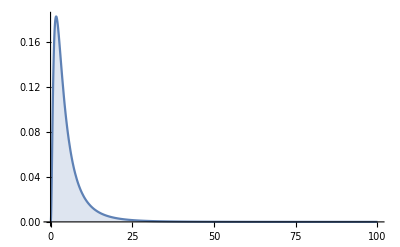
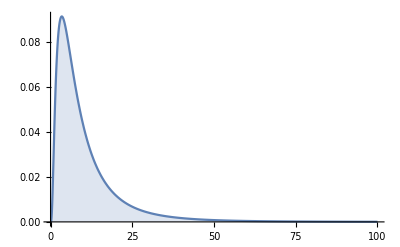
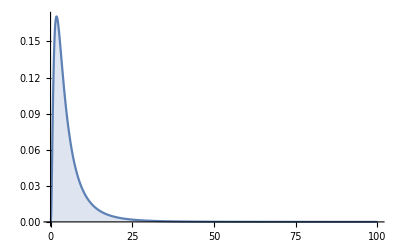
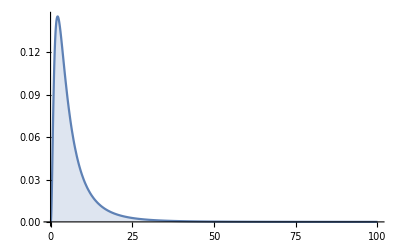
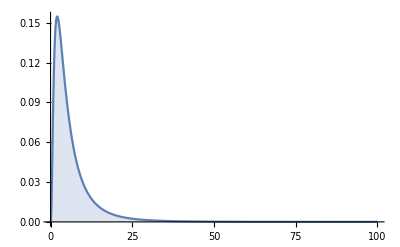
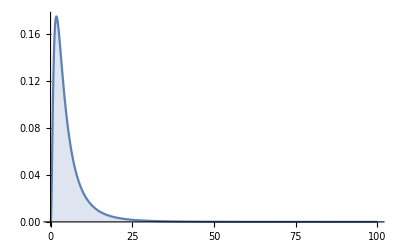
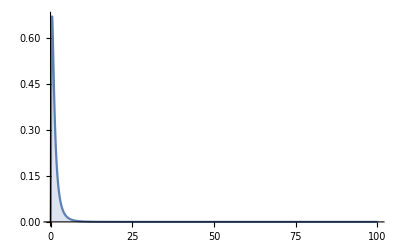
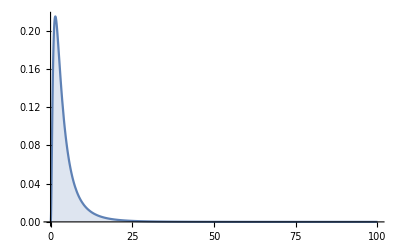

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@timesByBedBP
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,timesByBedBP,Method->"CoarsestGrained"];
```

#### results1

```mathematica
%
```

```mathematica
parametrosDis={{{5.3372759637363485,{5.228958768020561,5.450087128525761},{5.228958768020561,5.4211926033601125}},{5.662048063374679,{5.3306479161360905,6.082939341262235},{5.3306479161360905,5.942618002066503}},{32.097437426177194,{28.415807205806047,37.00215102947583},{28.415807205806047,35.31470871848488}},{3.659862603188328,{3.583161045322602,3.738694236617932},{3.583161045322602,3.718232075227793}},{2.037037422257931,{1.989516763322096,2.0853907407472816},{1.989516763322096,2.0720378722674173}},{6.575275795354329,{6.426330438260508,6.729638219643835},{6.426330438260508,6.68699308408553}},{4.538858600732614,{4.39662237738936,4.683288967942823},{4.39662237738936,4.645376102678026}},{4.278016633024781,{3.268397033166722,6.604758934123988},{3.268397033166722,5.45310907203343}}},{{10.680849546041902,{10.461556124521179,10.904225580839897},{10.461556124521179,10.843748515642016}},{11.335386348993492,{10.671256899045638,12.176009701337009},{10.671256899045638,11.892741844688599}},{128.63806565304722,{113.8757238054291,148.25521224705295},{113.8757238054291,141.4373085844072}},{7.322584919572927,{7.1671786015570795,7.481201506561042},{7.1671786015570795,7.43665236068121}},{4.075150640875958,{3.9808737365698486,4.170023994213417},{3.9808737365698486,4.144382819696775}},{13.153925217718834,{12.84970336523621,13.459081457468667},{12.84970336523621,13.37968223770834}},{9.080006593176181,{8.8003438182837,9.368293140116982},{8.8003438182837,9.290610960244912}},{4.276655351996002,{3.2863437094358323,6.68164660884986},{3.2863437094358323,5.507431333636056}}},{{5.720487144427171,{5.603251118462257,5.838385842462969},{5.603251118462257,5.807416388087363}},{6.06931729266051,{5.71733184775153,6.508424187330838},{5.71733184775153,6.36430211356717}},{36.87899291935141,{32.68788345731392,42.35958540223308},{32.68788345731392,40.50434139275555}},{3.9221121189414916,{3.8394857014836967,4.005244178874843},{3.8394857014836967,3.983584438784099}},{2.1828969258756756,{2.1339823077185005,2.2326182727238915},{2.1339823077185005,2.2195334601545804}},{7.045606563687956,{6.883050135511243,7.209792439486813},{6.883050135511243,7.165634661915712}},{4.863363848251504,{4.712063102873669,5.018195010426786},{4.712063102873669,4.977851776216828}},{4.271615903977465,{3.276167069014414,6.579773334370673},{3.276167069014414,5.3990367684526674}}},{{6.716505439885101,{6.5764074971952216,6.860531704058313},{6.5764074971952216,6.820252416228021}},{7.12555825949187,{6.706751987423905,7.662269724918843},{6.706751987423905,7.483473341765253}},{50.83417585678442,{44.9805222208145,58.71037733740789},{44.9805222208145,56.00237325691119}},{4.606010668599222,{4.506546380180949,4.707052719116538},{4.506546380180949,4.679915919973164}},{2.5630689139125815,{2.502478082828881,2.6249583245663195},{2.502478082828881,2.607863521037407}},{8.274990398797616,{8.084603284190802,8.467810730224665},{8.084603284190802,8.416538242431018}},{5.712703235610069,{5.532979740754026,5.891581261921646},{5.532979740754026,5.846304332938343}},{4.29005399404306,{3.2745020805209815,6.858855154282704},{3.2745020805209815,5.54507465928658}}},{{6.316056576670916,{6.186452127548801,6.449129721469778},{6.186452127548801,6.412496411726732}},{6.703152821274832,{6.309105687075062,7.200738546156662},{6.309105687075062,7.0407995496591305}},{44.98581094199898,{39.80481457068289,51.850635610106366},{39.80481457068289,49.57285829848021}},{4.330482551831177,{4.240679634540884,4.421879678223457},{4.240679634540884,4.39900199470117}},{2.409696347891683,{2.35422017686961,2.4655402760869656},{2.35422017686961,2.450822988361559}},{7.78089995540571,{7.603568651865422,7.961246621416863},{7.603568651865422,7.912081847180621}},{5.371931900624525,{5.2055158212920665,5.537682589613069},{5.2055158212920665,5.496217768558024}},{4.2902876985191725,{3.273949103508615,6.714288457631942},{3.273949103508615,5.522905368956453}}},{{5.579082058451706,{5.465331365914482,5.695750169778183},{5.465331365914482,5.664797887950212}},{5.919184693129738,{5.56459174032129,6.359504651170156},{5.56459174032129,6.214887922580631}},{35.079730881900936,{30.96468123645192,40.44329940825485},{30.96468123645192,38.62483189023858}},{3.8256008114065567,{3.7456970452476144,3.9074799025214375},{3.7456970452476144,3.8857273677150954}},{2.128677350349022,{2.079422277613769,2.177133472157514},{2.079422277613769,2.1648185948175493}},{6.872375715183113,{6.715106396726421,7.035845515062524},{6.715106396726421,6.988899156350873}},{4.744354979253606,{4.595961791837094,4.8978672144992},{4.595961791837094,4.854624301834116}},{4.285824286495371,{3.264630812954291,6.712080206744237},{3.264630812954291,5.537487571822134}}},{{1.4551996677894443,{1.4250070023543762,1.4863206494629027},{1.4250070023543762,1.4776855785299352}},{1.5442193154039692,{1.45474867068263,1.6571640289011205},{1.45474867068263,1.620099305766388}},{2.387377371578841,{2.1162936948528794,2.7461926186837933},{2.1162936948528794,2.624721760544732}},{0.9976780337662146,{0.9765154149674,1.018961815792668},{0.9765154149674,1.013470395844295}},{0.55521945376553,{0.5424767026760653,0.5682650608432889},{0.5424767026760653,0.5646540389922237}},{1.7923998173571847,{1.7510873135236025,1.8348816596378608},{1.7510873135236025,1.823295119012361}},{1.237352565280522,{1.1982755316515494,1.277284323345488},{1.1982755316515494,1.2663936227911183}},{4.277491110713064,{3.278702981801575,6.743458855035166},{3.278702981801575,5.485159237005369}}},{{4.547739919711248,{4.454917893105463,4.64466661280597},{4.454917893105463,4.617738226313772}},{4.82563688092064,{4.542581414441241,5.186814648228194},{4.542581414441241,5.072722570873341}},{23.3154482357968,{20.635045906826985,26.903046195074563},{20.635045906826985,25.732514281047838}},{3.1182366396094867,{3.0534595078709823,3.1851592977249044},{3.0534595078709823,3.167089601307415}},{1.735033564391001,{1.6939731412756396,1.775778178465895},{1.6939731412756396,1.7647858637595384}},{5.602081225218928,{5.471578725060065,5.734019740650164},{5.471578725060065,5.697625995087547}},{3.8675612868339435,{3.7448168203243526,3.9920824429317743},{3.7448168203243526,3.958011976157346}},{4.284244677513918,{3.2677115411472397,6.788802639426506},{3.2677115411472397,5.537644311056796}}},{{6.072171071701372,{5.9523393546415875,6.2023088158983954},{5.9523393546415875,6.164674769071459}},{6.4432864250828015,{6.069825188828648,6.925447731475961},{6.069825188828648,6.760942874086641}},{41.56509776136856,{36.84277782293873,47.961826281405536},{36.84277782293873,45.71034854666293}},{4.163303899236335,{4.074836775006157,4.2511283985350055},{4.074836775006157,4.227996774069393}},{2.317034804023593,{2.2622325914850925,2.372196491570852},{2.2622325914850925,2.356399683596854}},{7.479274980864907,{7.308627990783471,7.657675791944314},{7.308627990783471,7.609924603213754}},{5.162956091202926,{5.001034040092203,5.332538396506533},{5.001034040092203,5.285363330387419}},{4.286537586985349,{3.266394121633811,6.791382519124689},{3.266394121633811,5.490763023716331}}},{{8.348937748344389,{8.17206812882841,8.524386411116593},{8.17206812882841,8.477027457737623}},{8.854816580606213,{8.334912086010535,9.487589987492836},{8.334912086010535,9.292978305930356}},{78.4994948156603,{69.47075948152448,90.01436377077431},{69.47075948152448,86.35944579449223}},{5.725566934074715,{5.603275553187498,5.850965528422284},{5.603275553187498,5.816355982650855}},{3.1851913642073315,{3.111617660391874,3.261053958643319},{3.111617660391874,3.2391859995079706}},{10.286286513632282,{10.046759323492186,10.52722958235166},{10.046759323492186,10.465161666194389}},{7.102067928982707,{6.876915111550103,7.3284483172162265},{6.876915111550103,7.269795357035756}},{4.272803158529434,{3.269172739027978,6.699360017664194},{3.269172739027978,5.44851623773472}}},{{3.1212919881967456,{3.0561262521257557,3.186271416043191},{3.0561262521257557,3.1686020596165103}},{3.310173040975114,{3.1164495700039097,3.5539361464397237},{3.1164495700039097,3.473831288138028}},{10.970240519430034,{9.712257922377553,12.630462132970834},{9.712257922377553,12.067503818446713}},{2.140680085543265,{2.0945732844866747,2.186584395686915},{2.0945732844866747,2.1749068060152394}},{1.1912925958219711,{1.163661443231398,1.2188585695459198},{1.163661443231398,1.211612315245069}},{3.8452067560869114,{3.755324342764366,3.9338094409068414},{3.755324342764366,3.91015430797925}},{2.6542715722620542,{2.569396061916616,2.7384110119414826},{2.569396061916616,2.715781890037044}},{4.268439173582851,{3.2552448598857358,6.726314235802724},{3.2552448598857358,5.450238687600115}}},{{3.0373417947566725,{2.974214105919748,3.1011017559538434},{2.974214105919748,3.084648685721139}},{3.2241813110756934,{3.0331672699465395,3.468227797622525},{3.0331672699465395,3.3831279123320415}},{10.40803074347756,{9.200103687474943,12.028604056201592},{9.200103687474943,11.445554471200158}},{2.082399721231409,{2.0386717344503165,2.1277182454475394},{2.0386717344503165,2.1147386754526343}},{1.1589104980687432,{1.1321823227553887,1.1863689393735095},{1.1321823227553887,1.178878786420152}},{3.741277907815484,{3.6547829125617675,3.8303586490536667},{3.6547829125617675,3.806085761736168}},{2.5827161501136637,{2.5008270161900557,2.6659560079827904},{2.5008270161900557,2.643351192681874}},{4.301312113601866,{3.282761071115018,6.829030376527373},{3.282761071115018,5.48314749622303}}}};
```

#### median

```mathematica
Thread[{"HRD","HRDoutcome","HRDg2","HRDg3","HRDg4","HRDm","HRDw2","HRDw3","HRDw4","HRDw5","HRDvalley","HRDyes"}->parametrosDis[[All,4,{1,3}]]]
```

{HRD→{3.65986,{3.58316,3.71823}},HRDoutcome→{7.32258,{7.16718,7.43665}},HRDg2→{3.92211,{3.83949,3.98358}},HRDg3→{4.60601,{4.50655,4.67992}},HRDg4→{4.33048,{4.24068,4.399}},HRDm→{3.8256,{3.7457,3.88573}},HRDw2→{0.997678,{0.976515,1.01347}},HRDw3→{3.11824,{3.05346,3.16709}},HRDw4→{4.1633,{4.07484,4.228}},HRDw5→{5.72557,{5.60328,5.81636}},HRDvalley→{2.14068,{2.09457,2.17491}},HRDyes→{2.0824,{2.03867,2.11474}}}

#### IQR

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,5]]]
```

{HRD→{2.1621,{2.06933,2.25594},{2.06933,2.23132}},HICU-→{3.4366,{3.32555,3.54914},{3.32555,3.51966}},-ICURD→{5.2344,{5.03473,5.43697},{5.03473,5.38261}},HICURD→{12.1656,{11.9147,12.4269},{11.9147,12.3554}},HICU-→{3.30336,{3.20902,3.39908},{3.20902,3.3724}},-ICUH-→{2.86468,{2.76901,2.96326},{2.76901,2.93703}},-HRD→{2.30134,{2.21979,2.387},{2.21979,2.36371}},HICUHRD→{18.6818,{18.3194,19.048},{18.3194,18.9456}},ICURD→{2.55712,{2.45881,2.65636},{2.45881,2.6285}},ICUH-→{4.40924,{4.2528,4.56523},{4.2528,4.52255}},-HRD→{1.94332,{1.8721,2.01696},{1.8721,1.99716}},ICUHRD→{13.1908,{12.7834,13.6138},{12.7834,13.4994}},ICUH-→{3.12113,{3.03439,3.21026},{3.03439,3.18666}},HICU→{1.45544,{1.41946,1.49033},{1.41946,1.48144}},ICURD→{2.75952,{2.66826,2.85052},{2.66826,2.82728}},ICUHICURD→{13.3769,{13.1186,13.6363},{13.1186,13.5641}}}

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,6]]]
```

{HRD→{19.4482,{18.5965,20.3185},{18.5965,20.0796}},HICU-→{13.2705,{12.989,13.562},{12.989,13.4797}},-ICURD→{24.4551,{23.8588,25.0492},{23.8588,24.8845}},HICURD→{34.7737,{34.0531,35.4919},{34.0531,35.3101}},HICU-→{13.8619,{13.4752,14.2542},{13.4752,14.1532}},-ICUH-→{15.8243,{15.3022,16.3637},{15.3022,16.2216}},-HRD→{14.5844,{14.0716,15.1219},{14.0716,14.9731}},HICUHRD→{49.9067,{48.947,50.892},{48.947,50.6273}},ICURD→{17.5285,{16.8732,18.2159},{16.8732,18.0254}},ICUH-→{25.8983,{25.0151,26.8255},{25.0151,26.5698}},-HRD→{12.4625,{12.0142,12.9224},{12.0142,12.7956}},ICUHRD→{48.4055,{47.3999,49.4275},{47.3999,49.1618}},ICUH-→{13.3959,{13.0087,13.7858},{13.0087,13.6812}},HICU→{4.92271,{4.80648,5.04298},{4.80648,5.01014}},ICURD→{14.7047,{14.2298,15.1936},{14.2298,15.0594}},ICUHICURD→{35.5889,{34.9094,36.2809},{34.9094,36.0991}}}

### Sampling adjusted

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
timesByBedBP={LogNormalDistribution[0.83032,0.93247],LogNormalDistribution[0.83032+0.58260,0.93247],LogNormalDistribution[0.83032+0.21435,0.93247],LogNormalDistribution[0.83032+0.36212,0.93247],LogNormalDistribution[0.83032+0.24247,0.93247],LogNormalDistribution[0.83032+0.07160,0.93247],LogNormalDistribution[0.83032-0.98004,0.93247],LogNormalDistribution[0.83032+0.50721,0.93247],LogNormalDistribution[0.83032+0.77331,0.93247],LogNormalDistribution[0.83032+1.13299,0.93247],LogNormalDistribution[0.83032-0.38565,0.93247],LogNormalDistribution[0.83032-0.51968,0.93247]};
```

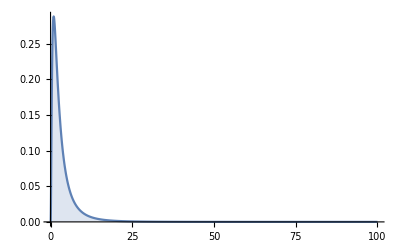
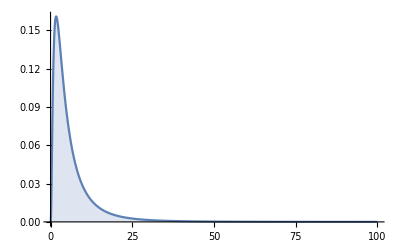
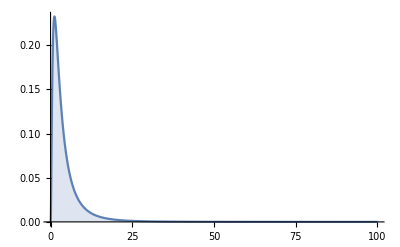
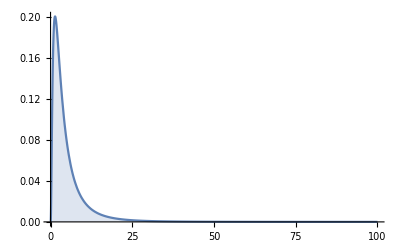
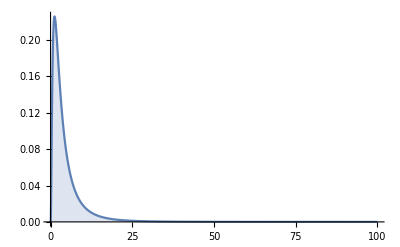
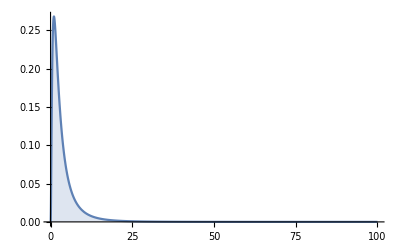
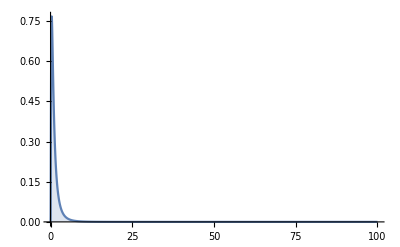
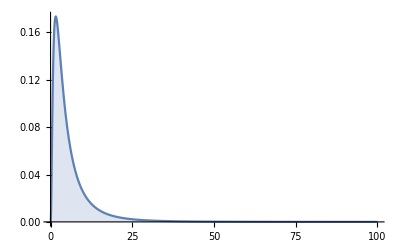

```mathematica
Plot[PDF[#,x],{x,0,100},Filling->Axis,PlotRange->All]&/@timesByBedBP
```

```mathematica
disParameters[dis_,samplingSize_,samplingN_]:=Module[{sample},
sample=Table[RandomVariate[dis,samplingSize],samplingN];
{Mean[#],(*MeanCI[#],*)Quantile[#,{0.025,0.975}],Quantile[#,{0.025,0.925}]}&/@Transpose[{Mean[#], StandardDeviation[#],Variance[#],Median[#],Quantile[#,0.25],Quantile[#,0.75],InterquartileRange[#],Skewness[#]}&/@sample]]
```

```mathematica
ParallelMap[disParameters[#,10^4,10^4]&,timesByBedBP,Method->"CoarsestGrained"];
```

#### results1

```mathematica
%
```

```mathematica
parametrosDis={{{3.5428239070764738,{3.461060790567522,3.6256485804069687},{3.461060790567522,3.6028185321779733}},{4.16698952672273,{3.882262555063196,4.545039621185539},{3.882262555063196,4.414970780781396}},{17.393348040202646,{15.071962546445818,20.657385158146386},{15.071962546445818,19.49196699515349}},{2.294071565570913,{2.2415406448089517,2.3467823394094234},{2.2415406448089517,2.333262432628804}},{1.2229210536560788,{1.1923049600015594,1.253869250188164},{1.1923049600015594,1.245173713685719}},{4.301771540825164,{4.195606739509915,4.4074131861062185},{4.195606739509915,4.38079796534781}},{3.07930182294396,{2.9794758115789453,3.179735320967887},{2.9794758115789453,3.153905877918115}},{4.998948516461602,{3.65007150379877,8.631458095371926},{3.65007150379877,6.689498585255702}}},{{6.344995724067227,{6.203451378132914,6.494202861706942},{6.203451378132914,6.454190245821596}},{7.464067892443742,{6.955732787604881,8.147818352697605},{6.955732787604881,7.902648561118746}},{55.81112845194702,{48.38221861256157,66.3869439085559},{48.38221861256157,62.45185428055219}},{4.109255867640756,{4.016444843994986,4.20300236166935},{4.016444843994986,4.178181494266798}},{2.190109967944742,{2.1364572195490275,2.244320886066501},{2.1364572195490275,2.229848818249264}},{7.703718326988595,{7.519593836911008,7.8959506030941045},{7.519593836911008,7.843351613576034}},{5.514400121991482,{5.339256831381454,5.697266027417049},{5.339256831381454,5.646636167652142}},{5.0063532763240195,{3.64246556426795,8.773393180846297},{3.64246556426795,6.66651758565143}}},{{4.390105498726275,{4.291869257874035,4.494049659707857},{4.291869257874035,4.46477628221771}},{5.161540398650251,{4.817247622317048,5.619098417284209},{4.817247622317048,5.462086883786985}},{26.686319932498822,{23.20587465471925,31.574267023125902},{23.20587465471925,29.834393126037813}},{2.8429828798149543,{2.7782218696768,2.9094248590491034},{2.7782218696768,2.8913665182178545}},{1.5156328134751171,{1.4787539629492779,1.5539785301251217},{1.4787539629492779,1.5434255106820893}},{5.33047270657918,{5.1972904633723385,5.4669980300906325},{5.1972904633723385,5.429588048087401}},{3.815409523488596,{3.6914448412544667,3.9450955133878867},{3.6914448412544667,3.9087793114585336}},{4.974305060821612,{3.6603408030573275,8.407179006269882},{3.6603408030573275,6.592946982708071}}},{{5.089312713976638,{4.97275232064687,5.208853598630239},{4.97275232064687,5.176706663632326}},{5.986340952577907,{5.583635360336413,6.515286860444012},{5.583635360336413,6.331851488519825}},{35.89459986793114,{31.176983837199153,42.448962873874386},{31.176983837199153,40.09234327267072}},{3.294890080696997,{3.220825995436557,3.371766868597396},{3.220825995436557,3.3508681371232685}},{1.756556485242524,{1.7133100612176875,1.7999201389851904},{1.7133100612176875,1.7883351191556012}},{6.179121659913337,{6.02704625087323,6.335474819241368},{6.02704625087323,6.293165663843013}},{4.423227670763041,{4.278420525202843,4.570828788098103},{4.278420525202843,4.530605718609892}},{4.973429629483461,{3.651974527343286,8.325224454675629},{3.651974527343286,6.564353247531841}}},{{4.515697900544034,{4.410857053684106,4.621222301197437},{4.410857053684106,4.5933662593604385}},{5.308733660680592,{4.949800792024325,5.786236731083263},{4.949800792024325,5.620192875136603}},{28.229446533796178,{24.500527880724633,33.48053550813712},{24.500527880724633,31.58656795373623}},{2.9241792917087595,{2.8577078855358167,2.992200796033975},{2.8577078855358167,2.973708358969417}},{1.5588979488698478,{1.5203676815156355,1.598247744908534},{1.5203676815156355,1.5874047853082491}},{5.483438197604586,{5.350238336016463,5.622941403215945},{5.350238336016463,5.584822409762511}},{3.925099794203177,{3.7989050990138495,4.054808218123513},{3.7989050990138495,4.021443156305109}},{4.961365829806997,{3.6351586725785587,8.514286522850345},{3.6351586725785587,6.597584408014566}}},{{3.807029967676613,{3.720939462998361,3.8949637482947366},{3.720939462998361,3.8716659814436323}},{4.477125143155876,{4.174957331405289,4.888100056805786},{4.174957331405289,4.744609355298618}},{20.07908571252665,{17.43026871905477,23.89352216534473},{17.43026871905477,22.51131793438717}},{2.465113584883301,{2.408473253851149,2.5211597035963527},{2.408473253851149,2.5069075773244665}},{1.3141109905189743,{1.2815645817919479,1.3474392521164147},{1.2815645817919479,1.3387208316546995}},{4.622246056112418,{4.510752503300618,4.736733007175084},{4.510752503300618,4.7064167731310365}},{3.308624098518381,{3.202371240594983,3.417550320200889},{3.202371240594983,3.3882406610463884}},{4.984008149828606,{3.639021736652009,8.567063932811257},{3.639021736652009,6.690366858746149}}},{{1.329689176299313,{1.2990629330582368,1.3614328325042082},{1.2990629330582368,1.3522182637393372}},{1.563543679015745,{1.456257355479227,1.7056355313795},{1.456257355479227,1.6581140609520437}},{2.4489696125456617,{2.120685485387352,2.9091925659042293},{2.120685485387352,2.749342239126878}},{0.8609395494002996,{0.8414136268819645,0.8807062619599875},{0.8414136268819645,0.8757466115319618}},{0.45888456197879207,{0.4476115135469396,0.47043070614293553},{0.4476115135469396,0.46721273745628183}},{1.6149043370780114,{1.574659561297979,1.655431869247393},{1.574659561297979,1.6448285926076334}},{1.1561882899580238,{1.118474890402619,1.1939882228927285},{1.118474890402619,1.1841465991582436}},{4.983527167352909,{3.6408448219033116,8.514259694407443},{3.6408448219033116,6.606245046089098}}},{{5.885022507556386,{5.7497883741420255,6.025937110981156},{5.7497883741420255,5.987580213227115}},{6.921841088994464,{6.458644315787692,7.543545343818682},{6.458644315787692,7.321911583608135}},{47.9909670579703,{41.71408639785666,56.905076354248514},{41.71408639785666,53.61038923817499}},{3.810017641304175,{3.723973259432741,3.89859038978531},{3.723973259432741,3.875723818558426}},{2.0309059306897472,{1.9794713692714265,2.0812110272084348},{1.9794713692714265,2.0681870072773294}},{7.144856800811421,{6.967875865628373,7.327259998642699},{6.967875865628373,7.278552198609297}},{5.114708164355862,{4.9483039620885,5.286584909576778},{4.9483039620885,5.240021002596713}},{4.971929647414786,{3.6625448383945245,8.375825016542658},{3.6625448383945245,6.559999525351326}}},{{7.678063565168534,{7.505767553046511,7.857144342019859},{7.505767553046511,7.808973169078366}},{9.033736541823977,{8.42405322615871,9.861690018656795},{8.42405322615871,9.561419551481187}},{81.74405816924218,{70.96467275715497,97.25293002407506},{70.96467275715497,91.42074383944671}},{4.971275764315017,{4.855103089602424,5.086612890824368},{4.855103089602424,5.056511300695822}},{2.6504009384549763,{2.5858770574333243,2.715722946370222},{2.5858770574333243,2.698401110654566}},{9.322854191164529,{9.09129308106825,9.55937557732384},{9.09129308106825,9.4966969676212}},{6.673464349586969,{6.454006789694585,6.894622617093328},{6.454006789694585,6.836776097730008}},{4.9927978195585645,{3.6526520563697082,8.58076163682448},{3.6526520563697082,6.704493854824994}}},{{11.004264574721276,{10.751750500372685,11.258997960142079},{10.751750500372685,11.19139414491245}},{12.94076932217207,{12.064299375530165,14.090106203160438},{12.064299375530165,13.699168402676644}},{167.73932084944892,{145.54731942241753,198.53109281634028},{145.54731942241753,187.66721492489415}},{7.125065296650697,{6.957716977470318,7.288366420618745},{6.957716977470318,7.245322746953544}},{3.798418645520306,{3.7042930924082027,3.891598052490496},{3.7042930924082027,3.8689485260624243}},{13.361377231890124,{13.02756758887509,13.690232050004182},{13.02756758887509,13.602503463133589}},{9.564342654163976,{9.24496430790734,9.874725570792219},{9.24496430790734,9.79335936804435}},{4.966837026780622,{3.637196013343703,8.291165222850353},{3.637196013343703,6.597635403669171}}},{{2.4092159178818764,{2.353920964569382,2.4661228004215556},{2.353920964569382,2.450240318387984}},{2.831358885635067,{2.64099606369571,3.0814832630110143},{2.64099606369571,2.995836117011504}},{8.030139328963955,{6.974860208456234,9.495539100217007},{6.974860208456234,8.975034039990566}},{1.5600306677767763,{1.5237863316512084,1.5962980335964416},{1.5237863316512084,1.5865663057613246}},{0.8317753003864287,{0.8113888446434683,0.8525013661426102},{0.8113888446434683,0.8473534690772858}},{2.9262236776217803,{2.852884388108473,2.9991990925902603},{2.852884388108473,2.9794582813012034}},{2.0947554157185952,{2.026374205941618,2.164192255276232},{2.026374205941618,2.1453786133599184}},{4.962076433222864,{3.634261980246775,8.293365025790708},{3.634261980246775,6.542099326925872}}},{{2.107126282566614,{2.0589439006022316,2.1565506691027347},{2.0589439006022316,2.1433626912272046}},{2.4790237079844806,{2.311680912636007,2.7126372329339374},{2.311680912636007,2.624481429783486}},{6.156321449923399,{5.343868641845643,7.358400757499488},{5.343868641845643,6.88790277527837}},{1.3643150182781032,{1.333055735815524,1.3957191199002676},{1.333055735815524,1.3873337689681207}},{0.72728465955051,{0.7093935583586084,0.7456604464534659},{0.7093935583586084,0.7406457263643869}},{2.5587978225669947,{2.4945623345589483,2.623831555777548},{2.4945623345589483,2.605907731715884}},{1.8317844615995593,{1.7719411200652107,1.893722616366678},{1.7719411200652107,1.8766649830839908}},{5.005008785059948,{3.6431137067546993,8.786688919942476},{3.6431137067546993,6.668576518359817}}}};
```

#### median

```mathematica
Thread[{"HRD","HRDoutcome","HRDg2","HRDg3","HRDg4","HRDm","HRDw2","HRDw3","HRDw4","HRDw5","HRDvalley","HRDyes"}->parametrosDis[[All,4,{1,3}]]]
```

{HRD→{2.29407,{2.24154,2.33326}},HRDoutcome→{4.10926,{4.01644,4.17818}},HRDg2→{2.84298,{2.77822,2.89137}},HRDg3→{3.29489,{3.22083,3.35087}},HRDg4→{2.92418,{2.85771,2.97371}},HRDm→{2.46511,{2.40847,2.50691}},HRDw2→{0.86094,{0.841414,0.875747}},HRDw3→{3.81002,{3.72397,3.87572}},HRDw4→{4.97128,{4.8551,5.05651}},HRDw5→{7.12507,{6.95772,7.24532}},HRDvalley→{1.56003,{1.52379,1.58657}},HRDyes→{1.36432,{1.33306,1.38733}}}

#### IQR

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,5]]]
```

{HRD→{2.1621,{2.06933,2.25594},{2.06933,2.23132}},HICU-→{3.4366,{3.32555,3.54914},{3.32555,3.51966}},-ICURD→{5.2344,{5.03473,5.43697},{5.03473,5.38261}},HICURD→{12.1656,{11.9147,12.4269},{11.9147,12.3554}},HICU-→{3.30336,{3.20902,3.39908},{3.20902,3.3724}},-ICUH-→{2.86468,{2.76901,2.96326},{2.76901,2.93703}},-HRD→{2.30134,{2.21979,2.387},{2.21979,2.36371}},HICUHRD→{18.6818,{18.3194,19.048},{18.3194,18.9456}},ICURD→{2.55712,{2.45881,2.65636},{2.45881,2.6285}},ICUH-→{4.40924,{4.2528,4.56523},{4.2528,4.52255}},-HRD→{1.94332,{1.8721,2.01696},{1.8721,1.99716}},ICUHRD→{13.1908,{12.7834,13.6138},{12.7834,13.4994}},ICUH-→{3.12113,{3.03439,3.21026},{3.03439,3.18666}},HICU→{1.45544,{1.41946,1.49033},{1.41946,1.48144}},ICURD→{2.75952,{2.66826,2.85052},{2.66826,2.82728}},ICUHICURD→{13.3769,{13.1186,13.6363},{13.1186,13.5641}}}

```mathematica
Thread[{"HRD","HICU-","-ICURD","HICURD","HICU-","-ICUH-","-HRD","HICUHRD","ICURD","ICUH-","-HRD","ICUHRD","ICUH-","HICU","ICURD","ICUHICURD"}->parametrosDis[[All,6]]]
```

{HRD→{19.4482,{18.5965,20.3185},{18.5965,20.0796}},HICU-→{13.2705,{12.989,13.562},{12.989,13.4797}},-ICURD→{24.4551,{23.8588,25.0492},{23.8588,24.8845}},HICURD→{34.7737,{34.0531,35.4919},{34.0531,35.3101}},HICU-→{13.8619,{13.4752,14.2542},{13.4752,14.1532}},-ICUH-→{15.8243,{15.3022,16.3637},{15.3022,16.2216}},-HRD→{14.5844,{14.0716,15.1219},{14.0716,14.9731}},HICUHRD→{49.9067,{48.947,50.892},{48.947,50.6273}},ICURD→{17.5285,{16.8732,18.2159},{16.8732,18.0254}},ICUH-→{25.8983,{25.0151,26.8255},{25.0151,26.5698}},-HRD→{12.4625,{12.0142,12.9224},{12.0142,12.7956}},ICUHRD→{48.4055,{47.3999,49.4275},{47.3999,49.1618}},ICUH-→{13.3959,{13.0087,13.7858},{13.0087,13.6812}},HICU→{4.92271,{4.80648,5.04298},{4.80648,5.01014}},ICURD→{14.7047,{14.2298,15.1936},{14.2298,15.0594}},ICUHICURD→{35.5889,{34.9094,36.2809},{34.9094,36.0991}}}